# Análisis sistema LV modificado

## Valores numéricos de simulación

α=1.5318 igual que en el modelo de Chacón
β=0.1
γ=0.3
ϵγ=0.3
Condiciones iniciales:
x_1(0)=35
x_2(0)=5
La población de plaga en equilibrio va a ser la población deseada, para que se linealice en torno a la respuesta deseada. Este valor se fija en el 70% de la población de plaga antes de iniciar la aplicación
x_(1e)=0.7x_1(T)

```mathematica
simValues={α->1.5318,β->1,γ->0.3,ϵ->0.3}
```

{α→1.5318,β→1,γ→0.3,ϵ→0.3}

## Sistema inicial LV

```mathematica
f1=- γ *x1b* x2b + α x1b
```

x1b α-x1b x2b γ

```mathematica
g1=ϵ*γ *x1b* x2b - β*x2b
```

-x2b β+x1b x2b γ ϵ

```mathematica
x1e1=β/(ϵ γ)
```

β/(γ ϵ)

```mathematica
x1e1/.simValues
```

11.1111

```mathematica
x2e1=α/γ
```

α/γ

```mathematica
x2e1/.simValues
```

5.106

### Estabilidad del sistema inicial

### Matriz A (Jacobiano evaluado en puntos de equilibrio)

```mathematica
A1={{D[f1,x1b],D[f1,x2b]},{D[g1,x1b],D[g1,x2b]}}
```

{{α-x2b γ,-x1b γ},{x2b γ ϵ,-β+x1b γ ϵ}}

```mathematica
Dimensions[A1]
```

{2,2}

```mathematica
A1e=A1 /. {x1b -> x1e1, x2b->x2e1}
```

{{0,-β/ϵ},{α ϵ,0}}

```mathematica
A1e//MatrixForm
```

(0 | -β/ϵ
α ϵ | 0)

### Autovalores, valores propios o eigenvalues

```mathematica
λ1= Eigenvalues[A1e]
λ1//MatrixForm
```

{-ⅈ √α √β,ⅈ √α √β}

(-ⅈ √α √β
ⅈ √α √β)

```mathematica
{λ1[[1]],λ1[[2]]}
```

{-ⅈ √α √β,ⅈ √α √β}

```mathematica
B1={{0},{0}}
```

{{0},{0}}

```mathematica
c1=Transpose[{{1},{0}}]
```

{{1,0}}

```mathematica
ssbase = StateSpaceModel[{A1e,B1,c1},SystemsModelLabels->{{"u"},{"y=x1"},{"x1","x2"}}]
```

0-β/ϵ0α ϵ00100uy=x1x1x2StateSpaceModelTrueTrueTrueFalse$CellContext`stname1$CellContext`stname2uy=x1x1x2IdentityAutomatic112111213132TrueTrueFalseAutomaticuy=x1x1x2Automatic

#### Solución a partir de la representación en espacio de estado del modelo linealizado

```mathematica
(*ssbasenum=ssbase/.simValues
stateplot=StateResponse[{ssbasenum,{35,0}},{0},{t,30}]
Plot[stateplot,{t,0,30},PlotTheme->"Scientific",PlotLabel->"Funciones de población X_1[t] y X_2[t] por linealización",Frame->True,FrameLabel->{{"Población",None},{"Tiempo",None}},PlotRange->All,PlotLegends->{"X_1(t)","X_2(t)"}]*)
```

#### Solución por métodos númericos

```mathematica
f1x[t]=- γ *x1[t]* x2[t] + α x1[t]
```

α x1[t]-γ x1[t] x2[t]

```mathematica
g1x[t]=ϵ*γ *x1[t]* x2[t]- β*x2[t]
```

-β x2[t]+γ ϵ x1[t] x2[t]

```mathematica
solNum=NDSolve[{f1x[t]==D[x1[t],t],g1x[t]==D[x2[t],t],x1[0]==35,x2[0]==5,α==1.5318,β==1,γ==0.3,ϵ==0.3},{x1,x2},{t,0,10}]
```

{{x1→InterpolatingFunction[…],x2→InterpolatingFunction[…]}}

```mathematica
x1Sol=x1/. solNum[[1]]
x2Sol=x2/. solNum[[1]]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

#### Método para convertir el objeto de función de interpolación a función por partes

```mathematica
InterpolationToPiecewise[if_,x_]:=Module[{main,default,grid},grid=if["Grid"];
Piecewise[{if@"GetPolynomial"[#,x-#],x<First@#}&/@grid[[2;;-2]],if@"GetPolynomial"[#,x-#]&@grid[[-1]]]]/;if["InterpolationMethod"]=="Hermite"
```

```mathematica
pwx1=InterpolationToPiecewise[x1Sol,t]
pwx2=InterpolationToPiecewise[x2Sol,t]
```

Piecewise[{{34.9982+(-0.000100782+t) (-17.5077+(-0.000100782+t) (-2.37453×10^-7+756114. (0.+t))), t<0.000100782}, {34.9965+(-17.5154+(-3.59035×10^-7+756046. (-0.000100782+t)) (-0.000201564+t)) (-0.000201564+t), t<0.000201564}, {34.9621+(-17.6639+(-38.062+4.14286×10^-7 (-0.000201564+t)) (-0.00215285+t)) (-0.00215285+t), t<0.00215285}, {34.9275+(-17.8122+(-37.993-5.41186×10^-8 (-0.00215285+t)) (-0.00410414+t)) (-0.00410414+t), t<0.00410414}, {34.8926+(-17.9602+(-37.9218+7.4833×10^-7 (-0.00410414+t)) (-0.00605543+t)) (-0.00605543+t), t<0.00605543}, {34.7965+(-18.3604+(-37.7442+14.7906 (-0.00605543+t)) (-0.0113515+t)) (-0.0113515+t), t<0.0113515}, {34.6982+(-18.7583+(-37.5322+13.555 (-0.0113515+t)) (-0.0166475+t)) (-0.0166475+t), t<0.0166475}, {34.5978+(-19.1538+(-37.2981+14.5642 (-0.0166475+t)) (-0.0219436+t)) (-0.0219436+t), t<0.0219436}, {34.4953+(-19.5466+(-37.0478+15.5822 (-0.0219436+t)) (-0.0272396+t)) (-0.0272396+t), t<0.0272396}, {34.2841+(-20.3238+(-36.5921+17.6179 (-0.0272396+t)) (-0.0378317+t)) (-0.0378317+t), t<0.0378317}, {34.0648+(-21.0884+(-35.9883+19.8188 (-0.0378317+t)) (-0.0484238+t)) (-0.0484238+t), t<0.0484238}, {33.8374+(-21.8391+(-35.3222+21.6661 (-0.0484238+t)) (-0.0590159+t)) (-0.0590159+t), t<0.0590159}, {33.6022+(-22.5745+(-34.5917+23.6575 (-0.0590159+t)) (-0.069608+t)) (-0.069608+t), t<0.069608}, {33.3593+(-23.2934+(-33.7987+25.6164 (-0.069608+t)) (-0.0802001+t)) (-0.0802001+t), t<0.0802001}, {32.9+(-24.5496+(-32.4531+28.2993 (-0.0802001+t)) (-0.0993928+t)) (-0.0993928+t), t<0.0993928}, {32.4173+(-25.7395+(-30.6981+31.5655 (-0.0993928+t)) (-0.118586+t)) (-0.118586+t), t<0.118586}, {31.9125+(-26.8563+(-28.7623+34.63 (-0.118586+t)) (-0.137778+t)) (-0.137778+t), t<0.137778}, {31.387+(-27.8935+(-26.6612+37.4064 (-0.137778+t)) (-0.156971+t)) (-0.156971+t), t<0.156971}, {30.8423+(-28.8453+(-24.4126+39.8562 (-0.156971+t)) (-0.176164+t)) (-0.176164+t), t<0.176164}, {30.2803+(-29.7066+(-22.0367+41.9428 (-0.176164+t)) (-0.195357+t)) (-0.195357+t), t<0.195357}, {29.5076+(-30.7066+(-18.9926+43.8681 (-0.195357+t)) (-0.220926+t)) (-0.220926+t), t<0.220926}, {28.7115+(-31.5313+(-15.5475+45.3492 (-0.220926+t)) (-0.246496+t)) (-0.246496+t), t<0.246496}, {27.8966+(-32.1765+(-12.0264+46.0817 (-0.246496+t)) (-0.272065+t)) (-0.272065+t), t<0.272065}, {27.0676+(-32.6407+(-8.48968+46.0304 (-0.272065+t)) (-0.297635+t)) (-0.297635+t), t<0.297635}, {26.2289+(-32.9258+(-4.99605+45.2204 (-0.297635+t)) (-0.323204+t)) (-0.323204+t), t<0.323204}, {25.3853+(-33.0362+(-1.60091+43.7063 (-0.323204+t)) (-0.348774+t)) (-0.348774+t), t<0.348774}, {24.5409+(-32.9793+(1.6454+41.5621 (-0.348774+t)) (-0.374343+t)) (-0.374343+t), t<0.374343}, {23.5063+(-32.6933+(5.1475+38.5304 (-0.374343+t)) (-0.405834+t)) (-0.405834+t), t<0.405834}, {22.4842+(-32.1895+(8.54291+34.594 (-0.405834+t)) (-0.437324+t)) (-0.437324+t), t<0.437324}, {21.481+(-31.4929+(11.5363+30.2071 (-0.437324+t)) (-0.468814+t)) (-0.468814+t), t<0.468814}, {20.5025+(-30.6303+(14.0991+25.5795 (-0.468814+t)) (-0.500304+t)) (-0.500304+t), t<0.500304}, {19.5533+(-29.6295+(16.2205+20.9015 (-0.500304+t)) (-0.531795+t)) (-0.531795+t), t<0.531795}, {18.6375+(-28.5179+(17.9063+16.3359 (-0.531795+t)) (-0.563285+t)) (-0.563285+t), t<0.563285}, {17.7581+(-27.3222+(19.1754+12.0137 (-0.563285+t)) (-0.594775+t)) (-0.594775+t), t<0.594775}, {16.9174+(-26.0669+(20.0573+8.03517 (-0.594775+t)) (-0.626266+t)) (-0.626266+t), t<0.626266}, {15.899+(-24.4073+(20.6475+4.0088 (-0.626266+t)) (-0.666612+t)) (-0.666612+t), t<0.666612}, {14.9482+(-22.7278+(20.8176+0.177423 (-0.666612+t)) (-0.706958+t)) (-0.706958+t), t<0.706958}, {14.0649+(-21.062+(20.5848-2.9013 (-0.706958+t)) (-0.747304+t)) (-0.747304+t), t<0.747304}, {13.2481+(-19.4366+(20.0377-5.26413 (-0.747304+t)) (-0.787651+t)) (-0.787651+t), t<0.787651}, {12.4957+(-17.8713+(19.2575-6.98021 (-0.787651+t)) (-0.827997+t)) (-0.827997+t), t<0.827997}, {11.805+(-16.3801+(18.3154-8.13695 (-0.827997+t)) (-0.868343+t)) (-0.868343+t), t<0.868343}, {11.1728+(-14.9721+(17.2716-8.82792 (-0.868343+t)) (-0.908689+t)) (-0.908689+t), t<0.908689}, {10.5957+(-13.652+(16.175-9.1446 (-0.908689+t)) (-0.949035+t)) (-0.949035+t), t<0.949035}, {10.07+(-12.4215+(15.0641-9.17093 (-0.949035+t)) (-0.989382+t)) (-0.989382+t), t<0.989382}, {9.59217+(-11.2798+(13.968-8.98043 (-0.989382+t)) (-1.02973+t)) (-1.02973+t), t<1.02973}, {9.15865+(-10.2241+(12.9079-8.63512 (-1.02973+t)) (-1.07007+t)) (-1.07007+t), t<1.07007}, {8.69427+(-9.07078+(11.7725-8.13739 (-1.07007+t)) (-1.11826+t)) (-1.11826+t), t<1.11826}, {8.28279+(-8.02649+(10.6557-7.51442 (-1.11826+t)) (-1.16644+t)) (-1.16644+t), t<1.16644}, {7.91918+(-7.08229+(9.63286-6.85449 (-1.16644+t)) (-1.21462+t)) (-1.21462+t), t<1.21462}, {7.59884+(-6.22897+(8.7059-6.19243 (-1.21462+t)) (-1.26281+t)) (-1.26281+t), t<1.26281}, {7.3176+(-5.45741+(7.87276-5.55165 (-1.26281+t)) (-1.31099+t)) (-1.31099+t), t<1.31099}, {7.07175+(-4.75894+(7.12891-4.94663 (-1.31099+t)) (-1.35917+t)) (-1.35917+t), t<1.35917}, {6.85796+(-4.12543+(6.46836-4.3855 (-1.35917+t)) (-1.40736+t)) (-1.40736+t), t<1.40736}, {6.67328+(-3.54939+(5.88436-3.87185 (-1.40736+t)) (-1.45554+t)) (-1.45554+t), t<1.45554}, {6.51511+(-3.024+(5.36999-3.4062 (-1.45554+t)) (-1.50372+t)) (-1.50372+t), t<1.50372}, {6.38115+(-2.54309+(4.91843-2.98709 (-1.50372+t)) (-1.5519+t)) (-1.5519+t), t<1.5519}, {6.26941+(-2.10115+(4.5232-2.61182 (-1.5519+t)) (-1.60009+t)) (-1.60009+t), t<1.60009}, {6.16528+(-1.63062+(4.14457-2.252 (-1.60009+t)) (-1.656+t)) (-1.656+t), t<1.656}, {6.08634+(-1.1991+(3.80525-1.91268 (-1.656+t)) (-1.71192+t)) (-1.71192+t), t<1.71192}, {6.03057+(-0.800632+(3.51794-1.61675 (-1.71192+t)) (-1.76783+t)) (-1.76783+t), t<1.76783}, {5.99628+(-0.430032+(3.27597-1.35885 (-1.76783+t)) (-1.82375+t)) (-1.82375+t), t<1.82375}, {5.98204+(-0.0827753+(3.07352-1.13389 (-1.82375+t)) (-1.87966+t)) (-1.87966+t), t<1.87966}, {5.98666+(0.245087+(2.90559-0.937362 (-1.87966+t)) (-1.93558+t)) (-1.93558+t), t<1.93558}, {6.00916+(0.557008+(2.76785-0.765228 (-1.93558+t)) (-1.99149+t)) (-1.99149+t), t<1.99149}, {6.04871+(0.856017+(2.65662-0.613984 (-1.99149+t)) (-2.04741+t)) (-2.04741+t), t<2.04741}, {6.13662+(1.278+(2.54614-0.451894 (-2.04741+t)) (-2.12967+t)) (-2.12967+t), t<2.12967}, {6.25858+(1.68505+(2.46219-0.287154 (-2.12967+t)) (-2.21194+t)) (-2.21194+t), t<2.21194}, {6.41362+(2.08334+(2.41467-0.147532 (-2.21194+t)) (-2.2942+t)) (-2.2942+t), t<2.2942}, {6.60125+(2.47812+(2.39827-0.0277519 (-2.2942+t)) (-2.37647+t)) (-2.37647+t), t<2.37647}, {6.82138+(2.87392+(2.40878+0.0763274 (-2.37647+t)) (-2.45874+t)) (-2.45874+t), t<2.45874}, {7.07424+(3.27472+(2.44289+0.167935 (-2.45874+t)) (-2.541+t)) (-2.541+t), t<2.541}, {7.36041+(3.68401+(2.49791+0.24955 (-2.541+t)) (-2.62327+t)) (-2.62327+t), t<2.62327}, {7.6807+(4.10495+(2.57172+0.323045 (-2.62327+t)) (-2.70553+t)) (-2.70553+t), t<2.70553}, {8.0362+(4.54039+(2.66253+0.389779 (-2.70553+t)) (-2.7878+t)) (-2.7878+t), t<2.7878}, {8.4282+(4.9929+(2.76884+0.450669 (-2.7878+t)) (-2.87006+t)) (-2.87006+t), t<2.87006}, {8.85822+(5.46485+(2.88929+0.50623 (-2.87006+t)) (-2.95233+t)) (-2.95233+t), t<2.95233}, {9.4137+(6.04646+(3.03893+0.560666 (-2.95233+t)) (-3.04888+t)) (-3.04888+t), t<3.04888}, {10.0269+(6.66091+(3.21144+0.612211 (-3.04888+t)) (-3.14544+t)) (-3.14544+t), t<3.14544}, {10.7011+(7.31083+(3.39722+0.654998 (-3.14544+t)) (-3.24199+t)) (-3.24199+t), t<3.24199}, {11.4399+(7.99833+(3.59335+0.68694 (-3.24199+t)) (-3.33854+t)) (-3.33854+t), t<3.33854}, {12.2469+(8.72481+(3.79609+0.704857 (-3.33854+t)) (-3.4351+t)) (-3.4351+t), t<3.4351}, {13.126+(9.49078+(4.00053+0.704177 (-3.4351+t)) (-3.53165+t)) (-3.53165+t), t<3.53165}, {14.0809+(10.2955+(4.2001+0.678553 (-3.53165+t)) (-3.62821+t)) (-3.62821+t), t<3.62821}, {15.1153+(11.1367+(4.38593+0.619298 (-3.62821+t)) (-3.72476+t)) (-3.72476+t), t<3.72476}, {16.2325+(12.0098+(4.5461+0.514638 (-3.72476+t)) (-3.82131+t)) (-3.82131+t), t<3.82131}, {17.4353+(12.9073+(4.66445+0.348718 (-3.82131+t)) (-3.91787+t)) (-3.91787+t), t<3.91787}, {18.7254+(13.8177+(4.71928+0.10029 (-3.91787+t)) (-4.01442+t)) (-4.01442+t), t<4.01442}, {20.1034+(14.7241+(4.68136-0.258944 (-4.01442+t)) (-4.11097+t)) (-4.11097+t), t<4.11097}, {21.5678+(15.6025+(4.51158-0.766345 (-4.11097+t)) (-4.20753+t)) (-4.20753+t), t<4.20753}, {23.1144+(16.4191+(4.15787-1.47055 (-4.20753+t)) (-4.30408+t)) (-4.30408+t), t<4.30408}, {24.735+(17.1276+(3.55157-2.43346 (-4.30408+t)) (-4.40063+t)) (-4.40063+t), t<4.40063}, {26.4164+(17.6651+(2.60339-3.73085 (-4.40063+t)) (-4.49719+t)) (-4.49719+t), t<4.49719}, {27.7642+(17.9133+(1.44111-5.23568 (-4.49719+t)) (-4.57289+t)) (-4.57289+t), t<4.57289}, {29.1233+(17.9538+(0.00700777-6.88754 (-4.57289+t)) (-4.64859+t)) (-4.64859+t), t<4.64859}, {30.1974+(17.7973+(-1.56334-8.65364 (-4.64859+t)) (-4.70863+t)) (-4.70863+t), t<4.70863}, {31.2562+(17.4345+(-3.33553-10.4565 (-4.70863+t)) (-4.76867+t)) (-4.76867+t), t<4.76867}, {32.0393+(16.9975+(-5.08433-12.2103 (-4.76867+t)) (-4.81412+t)) (-4.81412+t), t<4.81412}, {32.7989+(16.3992+(-6.89677-13.8433 (-4.81412+t)) (-4.85957+t)) (-4.85957+t), t<4.85957}, {33.5273+(15.6187+(-8.93868-15.5494 (-4.85957+t)) (-4.90503+t)) (-4.90503+t), t<4.90503}, {34.2157+(14.6348+(-11.2167-17.2885 (-4.90503+t)) (-4.95048+t)) (-4.95048+t), t<4.95048}, {34.8543+(13.4259+(-13.7295-18.9949 (-4.95048+t)) (-4.99593+t)) (-4.99593+t), t<4.99593}, {35.4324+(11.9717+(-16.4645-20.5779 (-4.99593+t)) (-5.04138+t)) (-5.04138+t), t<5.04138}, {35.9386+(10.2539+(-19.3946-21.9193 (-5.04138+t)) (-5.08684+t)) (-5.08684+t), t<5.08684}, {36.3604+(8.25817+(-22.4736-22.8699 (-5.08684+t)) (-5.13229+t)) (-5.13229+t), t<5.13229}, {36.685+(5.97609+(-25.6322-23.2518 (-5.13229+t)) (-5.17774+t)) (-5.17774+t), t<5.17774}, {36.8993+(3.40752+(-28.7749-22.8645 (-5.17774+t)) (-5.2232+t)) (-5.2232+t), t<5.2232}, {36.9905+(0.563113+(-31.7781-21.4986 (-5.2232+t)) (-5.26865+t)) (-5.26865+t), t<5.26865}, {36.9467+(-2.5331+(-34.4903-18.9579 (-5.26865+t)) (-5.3141+t)) (-5.3141+t), t<5.3141}, {36.8115+(-5.10178+(-36.4523-15.6024 (-5.3141+t)) (-5.34961+t)) (-5.34961+t), t<5.34961}, {36.5832+(-7.77429+(-37.8457-11.7298 (-5.34961+t)) (-5.38511+t)) (-5.38511+t), t<5.38511}, {36.2586+(-10.5182+(-38.7672-7.01937 (-5.38511+t)) (-5.42061+t)) (-5.42061+t), t<5.42061}, {35.8359+(-13.2948+(-39.1312-1.53038 (-5.42061+t)) (-5.45612+t)) (-5.45612+t), t<5.45612}, {35.3147+(-16.0602+(-38.8634+4.60877 (-5.45612+t)) (-5.49162+t)) (-5.49162+t), t<5.49162}, {34.6962+(-18.766+(-37.9078+11.2042 (-5.49162+t)) (-5.52712+t)) (-5.52712+t), t<5.52712}, {33.9835+(-21.3615+(-36.2332+18.0031 (-5.52712+t)) (-5.56262+t)) (-5.56262+t), t<5.56262}, {33.1813+(-23.7954+(-33.8391+24.703 (-5.56262+t)) (-5.59813+t)) (-5.59813+t), t<5.59813}, {32.2964+(-26.0185+(-30.759+30.9749 (-5.59813+t)) (-5.63363+t)) (-5.63363+t), t<5.63363}, {31.3369+(-27.9861+(-27.0619+36.489 (-5.63363+t)) (-5.66913+t)) (-5.66913+t), t<5.66913}, {30.3127+(-29.6602+(-22.8501+40.9464 (-5.66913+t)) (-5.70464+t)) (-5.70464+t), t<5.70464}, {29.2346+(-31.0119+(-18.2535+44.1083 (-5.70464+t)) (-5.74014+t)) (-5.74014+t), t<5.74014}, {28.3118+(-31.872+(-13.9894+45.7581 (-5.74014+t)) (-5.76947+t)) (-5.76947+t), t<5.76947}, {27.3672+(-32.4945+(-9.93406+46.1368 (-5.76947+t)) (-5.79881+t)) (-5.79881+t), t<5.79881}, {26.4078+(-32.88+(-5.90382+45.5185 (-5.79881+t)) (-5.82814+t)) (-5.82814+t), t<5.82814}, {25.4406+(-33.0342+(-1.98452+43.948 (-5.82814+t)) (-5.85747+t)) (-5.85747+t), t<5.85747}, {24.4721+(-32.9675+(1.74643+41.5354 (-5.85747+t)) (-5.8868+t)) (-5.8868+t), t<5.8868}, {23.5086+(-32.6942+(5.22251+38.414 (-5.8868+t)) (-5.91613+t)) (-5.91613+t), t<5.91613}, {22.5559+(-32.2318+(8.39037+34.7397 (-5.91613+t)) (-5.94547+t)) (-5.94547+t), t<5.94547}, {21.6194+(-31.6005+(11.211+30.6768 (-5.94547+t)) (-5.9748+t)) (-5.9748+t), t<5.9748}, {20.7036+(-30.8219+(13.6597+26.389 (-5.9748+t)) (-6.00413+t)) (-6.00413+t), t<6.00413}, {19.8125+(-29.9183+(15.726+22.0296 (-6.00413+t)) (-6.03346+t)) (-6.03346+t), t<6.03346}, {18.8068+(-28.7338+(17.5742+17.3838 (-6.03346+t)) (-6.06774+t)) (-6.06774+t), t<6.06774}, {17.8436+(-27.4437+(19.0326+12.6224 (-6.06774+t)) (-6.10203+t)) (-6.10203+t), t<6.10203}, {16.926+(-26.0803+(20.0273+8.25254 (-6.10203+t)) (-6.13631+t)) (-6.13631+t), t<6.13631}, {16.0559+(-24.6726+(20.6051+4.3643 (-6.13631+t)) (-6.17059+t)) (-6.17059+t), t<6.17059}, {15.2346+(-23.2464+(20.8193+1.00746 (-6.17059+t)) (-6.20487+t)) (-6.20487+t), t<6.20487}, {14.4621+(-21.8232+(20.7258-1.80435 (-6.20487+t)) (-6.23915+t)) (-6.23915+t), t<6.23915}, {13.738+(-20.4211+(20.3798-4.08533 (-6.23915+t)) (-6.27343+t)) (-6.27343+t), t<6.27343}, {13.0615+(-19.0544+(19.8336-5.8702 (-6.27343+t)) (-6.30772+t)) (-6.30772+t), t<6.30772}, {12.4311+(-17.7339+(19.1351-7.20693 (-6.30772+t)) (-6.342+t)) (-6.342+t), t<6.342}, {11.845+(-16.4678+(18.3265-8.15072 (-6.342+t)) (-6.37628+t)) (-6.37628+t), t<6.37628}, {11.3013+(-15.2615+(17.4444-8.75915 (-6.37628+t)) (-6.41056+t)) (-6.41056+t), t<6.41056}, {10.7979+(-14.1182+(16.5193-9.08861 (-6.41056+t)) (-6.44484+t)) (-6.44484+t), t<6.44484}, {10.3326+(-13.0395+(15.5761-9.19183 (-6.44484+t)) (-6.47912+t)) (-6.47912+t), t<6.47912}, {9.82774+(-11.8454+(14.5205-9.10161 (-6.47912+t)) (-6.51972+t)) (-6.51972+t), t<6.51972}, {9.36956+(-10.7401+(13.4333-8.82608 (-6.51972+t)) (-6.56032+t)) (-6.56032+t), t<6.56032}, {8.95451+(-9.72017+(12.3906-8.42069 (-6.56032+t)) (-6.60092+t)) (-6.60092+t), t<6.60092}, {8.57922+(-8.78108+(11.4045-7.93115 (-6.60092+t)) (-6.64152+t)) (-6.64152+t), t<6.64152}, {8.24049+(-7.91778+(10.4821-7.39365 (-6.64152+t)) (-6.68212+t)) (-6.68212+t), t<6.68212}, {7.93536+(-7.12483+(9.627-6.83542 (-6.68212+t)) (-6.72272+t)) (-6.72272+t), t<6.72272}, {7.66109+(-6.39669+(8.84007-6.27656 (-6.72272+t)) (-6.76331+t)) (-6.76331+t), t<6.76331}, {7.41516+(-5.72791+(8.12017-5.73125 (-6.76331+t)) (-6.80391+t)) (-6.80391+t), t<6.80391}, {7.19527+(-5.1132+(7.46484-5.20911 (-6.80391+t)) (-6.84451+t)) (-6.84451+t), t<6.84451}, {6.99932+(-4.54754+(6.87075-4.71619 (-6.84451+t)) (-6.88511+t)) (-6.88511+t), t<6.88511}, {6.82542+(-4.02621+(6.33405-4.25588 (-6.88511+t)) (-6.92571+t)) (-6.92571+t), t<6.92571}, {6.67186+(-3.54485+(5.85063-3.82964 (-6.92571+t)) (-6.96631+t)) (-6.96631+t), t<6.96631}, {6.53711+(-3.09939+(5.41634-3.43751 (-6.96631+t)) (-7.00691+t)) (-7.00691+t), t<7.00691}, {6.40026+(-2.61436+(4.98334-3.04817 (-7.00691+t)) (-7.05487+t)) (-7.05487+t), t<7.05487}, {6.2857+(-2.16874+(4.58168-2.66787 (-7.05487+t)) (-7.10283+t)) (-7.10283+t), t<7.10283}, {6.19167+(-1.75756+(4.23078-2.3284 (-7.10283+t)) (-7.15079+t)) (-7.15079+t), t<7.15079}, {6.11663+(-1.37639+(3.92511-2.02601 (-7.15079+t)) (-7.19875+t)) (-7.19875+t), t<7.19875}, {6.05923+(-1.0213+(3.65971-1.7571 (-7.19875+t)) (-7.24671+t)) (-7.24671+t), t<7.24671}, {6.01831+(-0.688788+(3.43008-1.5181 (-7.24671+t)) (-7.29467+t)) (-7.29467+t), t<7.29467}, {5.99285+(-0.375738+(3.23226-1.30568 (-7.29467+t)) (-7.34263+t)) (-7.34263+t), t<7.34263}, {5.98147+(0.00509603+(3.03295-1.09097 (-7.34263+t)) (-7.40472+t)) (-7.40472+t), t<7.40472}, {5.99301+(0.363179+(2.85628-0.880169 (-7.40472+t)) (-7.46681+t)) (-7.46681+t), t<7.46681}, {6.0262+(0.703046+(2.71525-0.698046 (-7.46681+t)) (-7.5289+t)) (-7.5289+t), t<7.5289}, {6.08002+(1.02863+(2.6051-0.540031 (-7.5289+t)) (-7.59099+t)) (-7.59099+t), t<7.59099}, {6.15371+(1.34333+(2.52182-0.402224 (-7.59099+t)) (-7.65308+t)) (-7.65308+t), t<7.65308}, {6.24667+(1.65016+(2.46209-0.281341 (-7.65308+t)) (-7.71517+t)) (-7.71517+t), t<7.71517}, {6.35851+(1.95173+(2.42308-0.174616 (-7.71517+t)) (-7.77726+t)) (-7.77726+t), t<7.77726}, {6.50516+(2.2846+(2.40168-0.0746885 (-7.77726+t)) (-7.84649+t)) (-7.84649+t), t<7.84649}, {6.6748+(2.61669+(2.39927+0.018804 (-7.84649+t)) (-7.91571+t)) (-7.91571+t), t<7.91571}, {6.86748+(2.95054+(2.41489+0.102384 (-7.91571+t)) (-7.98494+t)) (-7.98494+t), t<7.98494}, {7.0834+(3.28844+(2.4467+0.177708 (-7.98494+t)) (-8.05416+t)) (-8.05416+t), t<8.05416}, {7.32291+(3.63244+(2.49316+0.246111 (-8.05416+t)) (-8.12339+t)) (-8.12339+t), t<8.12339}, {7.5865+(3.98443+(2.55302+0.30871 (-8.12339+t)) (-8.19261+t)) (-8.19261+t), t<8.19261}, {7.87478+(4.34613+(2.62517+0.366365 (-8.19261+t)) (-8.26184+t)) (-8.26184+t), t<8.26184}, {8.18849+(4.71914+(2.7087+0.419688 (-8.26184+t)) (-8.33107+t)) (-8.33107+t), t<8.33107}, {8.65351+(5.24292+(2.82629+0.477248 (-8.33107+t)) (-8.42446+t)) (-8.42446+t), t<8.42446}, {9.16866+(5.79326+(2.97134+0.537181 (-8.42446+t)) (-8.51786+t)) (-8.51786+t), t<8.51786}, {9.73658+(6.37314+(3.1319+0.590276 (-8.51786+t)) (-8.61126+t)) (-8.61126+t), t<8.61126}, {10.3601+(6.98512+(3.30594+0.635772 (-8.61126+t)) (-8.70465+t)) (-8.70465+t), t<8.70465}, {11.0424+(7.63137+(3.49107+0.672177 (-8.70465+t)) (-8.79805+t)) (-8.79805+t), t<8.79805}, {11.7868+(8.3135+(3.6843+0.697128 (-8.79805+t)) (-8.89145+t)) (-8.89145+t), t<8.89145}, {12.5965+(9.03244+(3.88182+0.70719 (-8.89145+t)) (-8.98485+t)) (-8.98485+t), t<8.98485}, {13.4751+(9.78821+(4.07859+0.697576 (-8.98485+t)) (-9.07824+t)) (-9.07824+t), t<9.07824}, {14.5788+(10.7043+(4.2864+0.657446 (-9.07824+t)) (-9.186+t)) (-9.186+t), t<9.186}, {15.7836+(11.6634+(4.48084+0.568076 (-9.186+t)) (-9.29376+t)) (-9.29376+t), t<9.29376}, {17.0936+(12.657+(4.63245+0.411906 (-9.29376+t)) (-9.40151+t)) (-9.40151+t), t<9.40151}, {18.512+(13.6711+(4.71413+0.162487 (-9.40151+t)) (-9.50927+t)) (-9.50927+t), t<9.50927}, {19.7615+(14.506+(4.69964-0.175762 (-9.50927+t)) (-9.59795+t)) (-9.59795+t), t<9.59795}, {21.0844+(15.3229+(4.57921-0.60432 (-9.59795+t)) (-9.68663+t)) (-9.68663+t), t<9.68663}, {22.478+(16.0981+(4.31817-1.18663 (-9.68663+t)) (-9.77531+t)) (-9.77531+t), t<9.77531}, {23.9374+(16.7997+(3.86809-1.96633 (-9.77531+t)) (-9.864+t)) (-9.864+t), t<9.864}, {25.096+(17.2615+(3.2989-2.85995 (-9.864+t)) (-9.932+t)) (-9.932+t), t<9.932}, {26.283+(17.631+(2.58616-3.83022 (-9.932+t)) (-10.+t)) (-10.+t), True}}]

Piecewise[{{5.00082+(-0.000100782+t) (8.09153+(-0.000100782+t) (-6.29413×10^-8-51735. (0.+t))), t<0.000100782}, {5.00163+(8.09205+(6.57967×10^-8-51683.6 (-0.000100782+t)) (-0.000201564+t)) (-0.000201564+t), t<0.000201564}, {5.01743+(8.10211+(2.5786+2.11809×10^-7 (-0.000201564+t)) (-0.00215285+t)) (-0.00215285+t), t<0.00215285}, {5.03325+(8.11198+(2.528+1.39962×10^-8 (-0.00215285+t)) (-0.00410414+t)) (-0.00410414+t), t<0.00410414}, {5.04909+(8.12165+(2.47695-1.93613×10^-7 (-0.00410414+t)) (-0.00605543+t)) (-0.00605543+t), t<0.00605543}, {5.09217+(8.14686+(2.35324-10.4115 (-0.00605543+t)) (-0.0113515+t)) (-0.0113515+t), t<0.0113515}, {5.13538+(8.17056+(2.21377-9.01195 (-0.0113515+t)) (-0.0166475+t)) (-0.0166475+t), t<0.0166475}, {5.17871+(8.19271+(2.06673-9.22001 (-0.0166475+t)) (-0.0219436+t)) (-0.0219436+t), t<0.0219436}, {5.22215+(8.21328+(1.91643-9.42568 (-0.0219436+t)) (-0.0272396+t)) (-0.0272396+t), t<0.0272396}, {5.30935+(8.24951+(1.65827-9.83119 (-0.0272396+t)) (-0.0378317+t)) (-0.0378317+t), t<0.0378317}, {5.39689+(8.279+(1.33758-10.2534 (-0.0378317+t)) (-0.0484238+t)) (-0.0484238+t), t<0.0484238}, {5.48471+(8.30148+(1.00532-10.5895 (-0.0484238+t)) (-0.0590159+t)) (-0.0590159+t), t<0.0590159}, {5.57272+(8.31672+(0.661534-10.9404 (-0.0590159+t)) (-0.069608+t)) (-0.069608+t), t<0.069608}, {5.66086+(8.32449+(0.307081-11.2695 (-0.069608+t)) (-0.0802001+t)) (-0.0802001+t), t<0.0802001}, {5.82062+(8.31886+(-0.259029-11.6918 (-0.0802001+t)) (-0.0993928+t)) (-0.0993928+t), t<0.0993928}, {5.98002+(8.28688+(-0.949627-12.1389 (-0.0993928+t)) (-0.118586+t)) (-0.118586+t), t<0.118586}, {6.13854+(8.22764+(-1.66332-12.5096 (-0.118586+t)) (-0.137778+t)) (-0.137778+t), t<0.137778}, {6.29566+(8.14046+(-2.39367-12.7635 (-0.137778+t)) (-0.156971+t)) (-0.156971+t), t<0.156971}, {6.45083+(8.0249+(-3.1341-12.8984 (-0.156971+t)) (-0.176164+t)) (-0.176164+t), t<0.176164}, {6.60352+(7.88081+(-3.87758-12.909 (-0.176164+t)) (-0.195357+t)) (-0.195357+t), t<0.195357}, {6.80212+(7.64477+(-4.77894-12.7573 (-0.195357+t)) (-0.220926+t)) (-0.220926+t), t<0.220926}, {6.99404+(7.35937+(-5.73894-12.369 (-0.220926+t)) (-0.246496+t)) (-0.246496+t), t<0.246496}, {7.17806+(7.02657+(-6.65811-11.7634 (-0.246496+t)) (-0.272065+t)) (-0.272065+t), t<0.272065}, {7.35299+(6.64917+(-7.51993-10.9482 (-0.272065+t)) (-0.297635+t)) (-0.297635+t), t<0.297635}, {7.51774+(6.23073+(-8.30944-9.94496 (-0.297635+t)) (-0.323204+t)) (-0.323204+t), t<0.323204}, {7.67131+(5.77552+(-9.01366-8.78203 (-0.323204+t)) (-0.348774+t)) (-0.348774+t), t<0.348774}, {7.81283+(5.28836+(-9.62199-7.49228 (-0.348774+t)) (-0.374343+t)) (-0.374343+t), t<0.374343}, {7.96944+(4.65228+(-10.1932-5.9467 (-0.374343+t)) (-0.405834+t)) (-0.405834+t), t<0.405834}, {8.10551+(3.98608+(-10.6436-4.17507 (-0.405834+t)) (-0.437324+t)) (-0.437324+t), t<0.437324}, {8.22028+(3.30036+(-10.9256-2.39433 (-0.437324+t)) (-0.468814+t)) (-0.468814+t), t<0.468814}, {8.31328+(2.60556+(-11.0425-0.669119 (-0.468814+t)) (-0.500304+t)) (-0.500304+t), t<0.500304}, {8.38439+(1.91164+(-11.0031+0.946495 (-0.500304+t)) (-0.531795+t)) (-0.531795+t), t<0.531795}, {8.43378+(1.22777+(-10.8204+2.41032 (-0.531795+t)) (-0.563285+t)) (-0.563285+t), t<0.563285}, {8.4619+(0.562145+(-10.5107+3.69266 (-0.563285+t)) (-0.594775+t)) (-0.594775+t), t<0.594775}, {8.46945+(-0.0782117+(-10.0923+4.77557 (-0.594775+t)) (-0.626266+t)) (-0.626266+t), t<0.626266}, {8.45048+(-0.852539+(-9.47992+5.75602 (-0.626266+t)) (-0.666612+t)) (-0.666612+t), t<0.666612}, {8.40147+(-1.56658+(-8.71677+6.5481 (-0.666612+t)) (-0.706958+t)) (-0.706958+t), t<0.706958}, {8.32497+(-2.21411+(-7.88281+7.03334 (-0.706958+t)) (-0.747304+t)) (-0.747304+t), t<0.747304}, {8.22375+(-2.79174+(-7.01218+7.24943 (-0.747304+t)) (-0.787651+t)) (-0.787651+t), t<0.787651}, {8.10065+(-3.29848+(-6.1339+7.24075 (-0.787651+t)) (-0.827997+t)) (-0.827997+t), t<0.827997}, {7.95852+(-3.73533+(-5.27144+7.05325 (-0.827997+t)) (-0.868343+t)) (-0.868343+t), t<0.868343}, {7.80014+(-4.10479+(-4.44288+6.73092 (-0.868343+t)) (-0.908689+t)) (-0.908689+t), t<0.908689}, {7.62816+(-4.41051+(-3.66129+6.31334 (-0.908689+t)) (-0.949035+t)) (-0.949035+t), t<0.949035}, {7.44505+(-4.65687+(-2.93542+5.83452 (-0.949035+t)) (-0.989382+t)) (-0.989382+t), t<0.989382}, {7.25311+(-4.84874+(-2.27038+5.32246 (-0.989382+t)) (-1.02973+t)) (-1.02973+t), t<1.02973}, {7.05446+(-4.99118+(-1.66835+4.79935 (-1.02973+t)) (-1.07007+t)) (-1.07007+t), t<1.07007}, {6.81102+(-5.10361+(-1.06473+4.23272 (-1.07007+t)) (-1.11826+t)) (-1.11826+t), t<1.11826}, {6.56352+(-5.16122+(-0.510103+3.64227 (-1.11826+t)) (-1.16644+t)) (-1.16644+t), t<1.16644}, {6.31441+(-5.17197+(-0.0370276+3.09216 (-1.16644+t)) (-1.21462+t)) (-1.21462+t), t<1.21462}, {6.06575+(-5.14318+(0.361092+2.58989 (-1.21462+t)) (-1.26281+t)) (-1.26281+t), t<1.26281}, {5.81931+(-5.08151+(0.691506+2.13862 (-1.26281+t)) (-1.31099+t)) (-1.31099+t), t<1.31099}, {5.5765+(-4.99288+(0.961625+1.73853 (-1.31099+t)) (-1.35917+t)) (-1.35917+t), t<1.35917}, {5.33851+(-4.88252+(1.17868+1.38772 (-1.35917+t)) (-1.40736+t)) (-1.40736+t), t<1.40736}, {5.10627+(-4.75498+(1.34951+1.0831 (-1.40736+t)) (-1.45554+t)) (-1.45554+t), t<1.45554}, {4.88051+(-4.61423+(1.48042+0.820843 (-1.45554+t)) (-1.50372+t)) (-1.50372+t), t<1.50372}, {4.66177+(-4.46363+(1.57715+0.59686 (-1.50372+t)) (-1.5519+t)) (-1.5519+t), t<1.5519}, {4.45047+(-4.30607+(1.64482+0.407014 (-1.5519+t)) (-1.60009+t)) (-1.60009+t), t<1.60009}, {4.21495+(-4.11769+(1.69114+0.235879 (-1.60009+t)) (-1.656+t)) (-1.656+t), t<1.656}, {3.99005+(-3.92633+(1.71356+0.085684 (-1.656+t)) (-1.71192+t)) (-1.71192+t), t<1.71192}, {3.77587+(-3.73452+(1.71417-0.0346358 (-1.71192+t)) (-1.76783+t)) (-1.76783+t), t<1.76783}, {3.57239+(-3.54429+(1.69747-0.129708 (-1.76783+t)) (-1.82375+t)) (-1.82375+t), t<1.82375}, {3.37946+(-3.35721+(1.66723-0.203646 (-1.82375+t)) (-1.87966+t)) (-1.87966+t), t<1.87966}, {3.19687+(-3.17449+(1.62659-0.259973 (-1.87966+t)) (-1.93558+t)) (-1.93558+t), t<1.93558}, {3.02436+(-2.99706+(1.57816-0.301712 (-1.93558+t)) (-1.99149+t)) (-1.99149+t), t<1.99149}, {2.8616+(-2.82559+(1.52411-0.331435 (-1.99149+t)) (-2.04741+t)) (-2.04741+t), t<2.04741}, {2.63914+(-2.58505+(1.44736-0.354509 (-2.04741+t)) (-2.12967+t)) (-2.12967+t), t<2.12967}, {2.43587+(-2.35921+(1.35751-0.367355 (-2.12967+t)) (-2.21194+t)) (-2.21194+t), t<2.21194}, {2.25057+(-2.14833+(1.26655-0.368111 (-2.21194+t)) (-2.2942+t)) (-2.2942+t), t<2.2942}, {2.082+(-1.95226+(1.17687-0.360207 (-2.2942+t)) (-2.37647+t)) (-2.37647+t), t<2.37647}, {1.92896+(-1.77055+(1.09018-0.34624 (-2.37647+t)) (-2.45874+t)) (-2.45874+t), t<2.45874}, {1.79031+(-1.60254+(1.00765-0.328158 (-2.45874+t)) (-2.541+t)) (-2.541+t), t<2.541}, {1.66494+(-1.44744+(0.930032-0.307405 (-2.541+t)) (-2.62327+t)) (-2.62327+t), t<2.62327}, {1.55183+(-1.30437+(0.857822-0.285032 (-2.62327+t)) (-2.70553+t)) (-2.70553+t), t<2.70553}, {1.45003+(-1.17241+(0.79129-0.261784 (-2.70553+t)) (-2.7878+t)) (-2.7878+t), t<2.7878}, {1.35865+(-1.0506+(0.730563-0.238166 (-2.7878+t)) (-2.87006+t)) (-2.87006+t), t<2.87006}, {1.27692+(-0.937974+(0.675678-0.214495 (-2.87006+t)) (-2.95233+t)) (-2.95233+t), t<2.95233}, {1.19232+(-0.816221+(0.621373-0.18889 (-2.95233+t)) (-3.04888+t)) (-3.04888+t), t<3.04888}, {1.11899+(-0.704267+(0.571959-0.161446 (-3.04888+t)) (-3.14544+t)) (-3.14544+t), t<3.14544}, {1.05605+(-0.600577+(0.530482-0.13405 (-3.14544+t)) (-3.24199+t)) (-3.24199+t), t<3.24199}, {1.00279+(-0.503614+(0.496985-0.106383 (-3.24199+t)) (-3.33854+t)) (-3.33854+t), t<3.33854}, {0.958634+(-0.411809+(0.471645-0.0779182 (-3.33854+t)) (-3.4351+t)) (-3.4351+t), t<3.4351}, {0.923156+(-0.323531+(0.45483-0.0479254 (-3.4351+t)) (-3.53165+t)) (-3.53165+t), t<3.53165}, {0.8961+(-0.237036+(0.447166-0.01542 (-3.53165+t)) (-3.62821+t)) (-3.62821+t), t<3.62821}, {0.877387+(-0.150405+(0.449627+0.0208987 (-3.62821+t)) (-3.72476+t)) (-3.72476+t), t<3.72476}, {0.86713+(-0.0614579+(0.463638+0.0627414 (-3.72476+t)) (-3.82131+t)) (-3.82131+t), t<3.82131}, {0.865675+(0.0323532+(0.491222+0.112356 (-3.82131+t)) (-3.91787+t)) (-3.91787+t), t<3.91787}, {0.873632+(0.134091+(0.535184+0.172691 (-3.91787+t)) (-4.01442+t)) (-4.01442+t), t<4.01442}, {0.891944+(0.247523+(0.599354+0.247599 (-4.01442+t)) (-4.11097+t)) (-4.11097+t), t<4.11097}, {0.921958+(0.377363+(0.688888+0.342052 (-4.11097+t)) (-4.20753+t)) (-4.20753+t), t<4.20753}, {0.965534+(0.529593+(0.810635+0.462339 (-4.20753+t)) (-4.30408+t)) (-4.30408+t), t<4.30408}, {1.02519+(0.711843+(0.973523+0.616094 (-4.30408+t)) (-4.40063+t)) (-4.40063+t), t<4.40063}, {1.10427+(0.933857+(1.18889+0.811912 (-4.40063+t)) (-4.49719+t)) (-4.49719+t), t<4.49719}, {1.18269+(1.14363+(1.42444+1.02806 (-4.49719+t)) (-4.57289+t)) (-4.57289+t), t<4.57289}, {1.27841+(1.39257+(1.69169+1.25471 (-4.57289+t)) (-4.64859+t)) (-4.64859+t), t<4.64859}, {1.36878+(1.62333+(1.96644+1.48516 (-4.64859+t)) (-4.70863+t)) (-4.70863+t), t<4.70863}, {1.47402+(1.8886+(2.26043+1.7077 (-4.70863+t)) (-4.76867+t)) (-4.76867+t), t<4.76867}, {1.56493+(2.11537+(2.53792+1.90918 (-4.76867+t)) (-4.81412+t)) (-4.81412+t), t<4.81412}, {1.6667+(2.36688+(2.81405+2.08261 (-4.81412+t)) (-4.85957+t)) (-4.85957+t), t<4.85957}, {1.7805+(2.64521+(3.11272+2.24332 (-4.85957+t)) (-4.90503+t)) (-4.90503+t), t<4.90503}, {1.9076+(2.95221+(3.43127+2.38013 (-4.90503+t)) (-4.95048+t)) (-4.95048+t), t<4.95048}, {2.04933+(3.28935+(3.76483+2.47519 (-4.95048+t)) (-4.99593+t)) (-4.99593+t), t<4.99593}, {2.20709+(3.65741+(4.10575+2.50625 (-4.99593+t)) (-5.04138+t)) (-5.04138+t), t<5.04138}, {2.38228+(4.05623+(4.44284+2.44556 (-5.04138+t)) (-5.08684+t)) (-5.08684+t), t<5.08684}, {2.57627+(4.48433+(4.76063+2.26019 (-5.08684+t)) (-5.13229+t)) (-5.13229+t), t<5.13229}, {2.79032+(4.93844+(5.03883+1.91322 (-5.13229+t)) (-5.17774+t)) (-5.17774+t), t<5.17774}, {3.02551+(5.41305+(5.25193+1.36617 (-5.17774+t)) (-5.2232+t)) (-5.2232+t), t<5.2232}, {3.28259+(5.89995+(5.36939+0.583364 (-5.2232+t)) (-5.26865+t)) (-5.26865+t), t<5.26865}, {3.56187+(6.38785+(5.35656-0.461917 (-5.26865+t)) (-5.3141+t)) (-5.3141+t), t<5.3141}, {3.79531+(6.76032+(5.21691-1.61626 (-5.3141+t)) (-5.34961+t)) (-5.34961+t), t<5.34961}, {4.0417+(7.11616+(4.96149-2.80594 (-5.34961+t)) (-5.38511+t)) (-5.38511+t), t<5.38511}, {4.30029+(7.44584+(4.56967-4.13098 (-5.38511+t)) (-5.42061+t)) (-5.42061+t), t<5.42061}, {4.56997+(7.73893+(4.02897-5.56095 (-5.42061+t)) (-5.45612+t)) (-5.45612+t), t<5.45612}, {4.84924+(7.98439+(3.33182-7.04402 (-5.45612+t)) (-5.49162+t)) (-5.49162+t), t<5.49162}, {5.13622+(8.17101+(2.477-8.51551 (-5.49162+t)) (-5.52712+t)) (-5.52712+t), t<5.52712}, {5.42861+(8.28795+(1.47114-9.89834 (-5.52712+t)) (-5.56262+t)) (-5.56262+t), t<5.56262}, {5.72377+(8.32535+(0.329559-11.1085 (-5.56262+t)) (-5.59813+t)) (-5.59813+t), t<5.59813}, {6.01873+(8.27499+(-0.923359-12.0616 (-5.59813+t)) (-5.63363+t)) (-5.63363+t), t<5.63363}, {6.31024+(8.13087+(-2.25476-12.6813 (-5.63363+t)) (-5.66913+t)) (-5.66913+t), t<5.66913}, {6.59492+(7.88976+(-3.62471-12.9074 (-5.66913+t)) (-5.70464+t)) (-5.70464+t), t<5.70464}, {6.86932+(7.55156+(-4.98851-12.7033 (-5.70464+t)) (-5.74014+t)) (-5.74014+t), t<5.74014}, {7.08583+(7.20106+(-6.1527-12.143 (-5.74014+t)) (-5.76947+t)) (-5.76947+t), t<5.76947}, {7.29117+(6.78989+(-7.17487-11.3223 (-5.76947+t)) (-5.79881+t)) (-5.79881+t), t<5.79881}, {7.48361+(6.32295+(-8.10984-10.2479 (-5.79881+t)) (-5.82814+t)) (-5.82814+t), t<5.82814}, {7.66161+(5.80638+(-8.93682-8.95016 (-5.82814+t)) (-5.85747+t)) (-5.85747+t), t<5.85747}, {7.82382+(5.24734+(-9.63918-7.48011 (-5.85747+t)) (-5.8868+t)) (-5.8868+t), t<5.8868}, {7.96911+(4.65375+(-10.2048-5.89072 (-5.8868+t)) (-5.91613+t)) (-5.91613+t), t<5.91613}, {8.09658+(4.034+(-10.6265-4.23852 (-5.91613+t)) (-5.94547+t)) (-5.94547+t), t<5.94547}, {8.20559+(3.39666+(-10.902-2.57852 (-5.94547+t)) (-5.9748+t)) (-5.9748+t), t<5.9748}, {8.29575+(2.75021+(-11.0336-0.961714 (-5.9748+t)) (-6.00413+t)) (-6.00413+t), t<6.00413}, {8.36692+(2.10278+(-11.0278+0.567576 (-6.00413+t)) (-6.03346+t)) (-6.03346+t), t<6.03346}, {8.42615+(1.355+(-10.8708+2.08239 (-6.03346+t)) (-6.06774+t)) (-6.06774+t), t<6.06774}, {8.46005+(0.62708+(-10.5565+3.5171 (-6.06774+t)) (-6.10203+t)) (-6.10203+t), t<6.10203}, {8.46947+(-0.0716711+(-10.1105+4.71763 (-6.10203+t)) (-6.13631+t)) (-6.13631+t), t<6.13631}, {8.45556+(-0.733648+(-9.55773+5.67465 (-6.13631+t)) (-6.17059+t)) (-6.17059+t), t<6.17059}, {8.41966+(-1.35296+(-8.92314+6.39102 (-6.17059+t)) (-6.20487+t)) (-6.20487+t), t<6.20487}, {8.36333+(-1.92536+(-8.23061+6.88059 (-6.20487+t)) (-6.23915+t)) (-6.23915+t), t<6.23915}, {8.28822+(-2.44814+(-7.50204+7.16453 (-6.23915+t)) (-6.27343+t)) (-6.27343+t), t<6.27343}, {8.19606+(-2.91996+(-6.75683+7.26871 (-6.27343+t)) (-6.30772+t)) (-6.30772+t), t<6.30772}, {8.0886+(-3.34062+(-6.01156+7.22107 (-6.30772+t)) (-6.342+t)) (-6.342+t), t<6.342}, {7.96759+(-3.71091+(-5.2799+7.04974 (-6.342+t)) (-6.37628+t)) (-6.37628+t), t<6.37628}, {7.83473+(-4.0324+(-4.5727+6.78153 (-6.37628+t)) (-6.41056+t)) (-6.41056+t), t<6.41056}, {7.69165+(-4.30724+(-3.89823+6.44093 (-6.41056+t)) (-6.44484+t)) (-6.44484+t), t<6.44484}, {7.53992+(-4.53803+(-3.26241+6.04959 (-6.44484+t)) (-6.47912+t)) (-6.47912+t), t<6.47912}, {7.35102+(-4.75834+(-2.59984+5.58643 (-6.47912+t)) (-6.51972+t)) (-6.51972+t), t<6.51972}, {7.15426+(-4.92599+(-1.96197+5.0631 (-6.51972+t)) (-6.56032+t)) (-6.56032+t), t<6.56032}, {6.95168+(-5.04618+(-1.38812+4.5379 (-6.56032+t)) (-6.60092+t)) (-6.60092+t), t<6.60092}, {6.7451+(-5.12405+(-0.877313+4.02521 (-6.60092+t)) (-6.64152+t)) (-6.64152+t), t<6.64152}, {6.53613+(-5.16456+(-0.427124+3.53564 (-6.64152+t)) (-6.68212+t)) (-6.68212+t), t<6.68212}, {6.32619+(-5.1724+(-0.0341523+3.07609 (-6.68212+t)) (-6.72272+t)) (-6.72272+t), t<6.72272}, {6.11653+(-5.15196+(0.305613+2.6507 (-6.72272+t)) (-6.76331+t)) (-6.76331+t), t<6.76331}, {5.90819+(-5.10725+(0.596508+2.26145 (-6.76331+t)) (-6.80391+t)) (-6.80391+t), t<6.80391}, {5.70211+(-5.04195+(0.842973+1.90873 (-6.80391+t)) (-6.84451+t)) (-6.84451+t), t<6.84451}, {5.49904+(-4.95937+(1.0494+1.59178 (-6.84451+t)) (-6.88511+t)) (-6.88511+t), t<6.88511}, {5.29962+(-4.86246+(1.22003+1.30906 (-6.88511+t)) (-6.92571+t)) (-6.92571+t), t<6.92571}, {5.10437+(-4.75387+(1.35886+1.05852 (-6.92571+t)) (-6.96631+t)) (-6.96631+t), t<6.96631}, {4.91374+(-4.63592+(1.46963+0.837843 (-6.96631+t)) (-7.00691+t)) (-7.00691+t), t<7.00691}, {4.69493+(-4.4873+(1.56443+0.628584 (-7.00691+t)) (-7.05487+t)) (-7.05487+t), t<7.05487}, {4.48342+(-4.33138+(1.63595+0.434574 (-7.05487+t)) (-7.10283+t)) (-7.10283+t), t<7.10283}, {4.27953+(-4.17061+(1.68252+0.271088 (-7.10283+t)) (-7.15079+t)) (-7.15079+t), t<7.15079}, {4.08341+(-4.00707+(1.70818+0.134346 (-7.15079+t)) (-7.19875+t)) (-7.19875+t), t<7.19875}, {3.89518+(-3.84247+(1.71642+0.0209234 (-7.19875+t)) (-7.24671+t)) (-7.24671+t), t<7.24671}, {3.71483+(-3.67825+(1.71032-0.0723006 (-7.24671+t)) (-7.29467+t)) (-7.29467+t), t<7.29467}, {3.54233+(-3.51556+(1.6925-0.148118 (-7.29467+t)) (-7.34263+t)) (-7.34263+t), t<7.34263}, {3.33049+(-3.30874+(1.65879-0.216746 (-7.34263+t)) (-7.40472+t)) (-7.40472+t), t<7.40472}, {3.13133+(-3.10762+(1.611-0.274753 (-7.40472+t)) (-7.46681+t)) (-7.46681+t), t<7.46681}, {2.94445+(-2.91336+(1.55456-0.315852 (-7.46681+t)) (-7.5289+t)) (-7.5289+t), t<7.5289}, {2.7694+(-2.72674+(1.49219-0.343308 (-7.5289+t)) (-7.59099+t)) (-7.59099+t), t<7.59099}, {2.60568+(-2.54826+(1.42608-0.35988 (-7.59099+t)) (-7.65308+t)) (-7.65308+t), t<7.65308}, {2.45278+(-2.37821+(1.35798-0.367822 (-7.65308+t)) (-7.71517+t)) (-7.71517+t), t<7.71517}, {2.31018+(-2.21669+(1.28926-0.368981 (-7.71517+t)) (-7.77726+t)) (-7.77726+t), t<7.77726}, {2.16267+(-2.04661+(1.21582-0.364447 (-7.77726+t)) (-7.84649+t)) (-7.84649+t), t<7.84649}, {2.02658+(-1.88689+(1.14141-0.354818 (-7.84649+t)) (-7.91571+t)) (-7.91571+t), t<7.91571}, {1.9012+(-1.73718+(1.06948-0.34167 (-7.91571+t)) (-7.98494+t)) (-7.98494+t), t<7.98494}, {1.78585+(-1.59707+(1.00067-0.325941 (-7.98494+t)) (-8.05416+t)) (-8.05416+t), t<8.05416}, {1.67987+(-1.46609+(0.935381-0.308411 (-8.05416+t)) (-8.12339+t)) (-8.12339+t), t<8.12339}, {1.58267+(-1.34371+(0.873908-0.289701 (-8.12339+t)) (-8.19261+t)) (-8.19261+t), t<8.19261}, {1.49365+(-1.22938+(0.816424-0.270284 (-8.19261+t)) (-8.26184+t)) (-8.26184+t), t<8.26184}, {1.41228+(-1.12254+(0.763028-0.250498 (-8.26184+t)) (-8.33107+t)) (-8.33107+t), t<8.33107}, {1.31376+(-0.989241+(0.702982-0.227086 (-8.33107+t)) (-8.42446+t)) (-8.42446+t), t<8.42446}, {1.22715+(-0.86713+(0.644363-0.200271 (-8.42446+t)) (-8.51786+t)) (-8.51786+t), t<8.51786}, {1.15148+(-0.754804+(0.593224-0.173642 (-8.51786+t)) (-8.61126+t)) (-8.61126+t), t<8.61126}, {1.0859+(-0.650873+(0.549519-0.147149 (-8.61126+t)) (-8.70465+t)) (-8.70465+t), t<8.70465}, {1.02968+(-0.55395+(0.513248-0.120569 (-8.70465+t)) (-8.79805+t)) (-8.79805+t), t<8.79805}, {0.982247+(-0.462631+(0.484505-0.093518 (-8.79805+t)) (-8.89145+t)) (-8.89145+t), t<8.89145}, {0.943135+(-0.375477+(0.463522-0.0654363 (-8.89145+t)) (-8.98485+t)) (-8.98485+t), t<8.98485}, {0.912027+(-0.290973+(0.450726-0.0355674 (-8.98485+t)) (-9.07824+t)) (-9.07824+t), t<9.07824}, {0.885864+(-0.194632+(0.447024-0.000224812 (-9.07824+t)) (-9.186+t)) (-9.186+t), t<9.186}, {0.870134+(-0.0968273+(0.456146+0.0430986 (-9.186+t)) (-9.29376+t)) (-9.29376+t), t<9.29376}, {0.865167+(0.00573456+(0.481005+0.0947609 (-9.29376+t)) (-9.40151+t)) (-9.40151+t), t<9.40151}, {0.871683+(0.117053+(0.52507+0.158464 (-9.40151+t)) (-9.50927+t)) (-9.50927+t), t<9.50927}, {0.886492+(0.218729+(0.583506+0.231078 (-9.50927+t)) (-9.59795+t)) (-9.59795+t), t<9.59795}, {0.910855+(0.333183+(0.659184+0.312888 (-9.59795+t)) (-9.68663+t)) (-9.68663+t), t<9.68663}, {0.946091+(0.464739+(0.760129+0.414938 (-9.68663+t)) (-9.77531+t)) (-9.77531+t), t<9.77531}, {0.993946+(0.618798+(0.892668+0.542679 (-9.77531+t)) (-9.864+t)) (-9.864+t), t<9.864}, {1.0406+(0.756345+(1.03452+0.681706 (-9.864+t)) (-9.932+t)) (-9.932+t), t<9.932}, {1.09729+(0.914772+(1.19297+0.826602 (-9.932+t)) (-10.+t)) (-10.+t), True}}]

```mathematica
(*Export["dir\\fpw1.txt",ToString[pwx1,InputForm]]
Export["dir\\fpw2.txt",ToString[pwx2,InputForm]]*)
```

```mathematica
pw1FromText=ToExpression[Import["C:\\Users\\Jennis\\Downloads\\funciones_correctas\\fpw1_last_7En26.txt"]]
pw2FromText=ToExpression[Import["C:\\Users\\Jennis\\Downloads\\funciones_correctas\\fpw2_last_7En26.txt"]]
```

Piecewise[{{35.0001+(-0.0000641343+t) (1.10576+(-0.0000641343+t) (2.01925×10^-7+1.75968×10^6 (0.+t))), t<0.0000641343}, {35.0001+(1.09852+(7.27429×10^-7+1.75994×10^6 (-0.0000641343+t)) (-0.000128269+t)) (-0.000128269+t), t<0.000128269}, {35.0003+(1.08404+(-56.4447+0.00529972 (-0.000128269+t)) (-0.000256537+t)) (-0.000256537+t), t<0.000256537}, {35.0004+(1.06956+(-56.4613-0.000205272 (-0.000256537+t)) (-0.000384806+t)) (-0.000384806+t), t<0.000384806}, {35.0006+(1.05507+(-56.4778+0.00375122 (-0.000384806+t)) (-0.000513074+t)) (-0.000513074+t), t<0.000513074}, {35.0018+(0.90995+(-56.5977-45.1545 (-0.000513074+t)) (-0.00179576+t)) (-0.00179576+t), t<0.00179576}, {35.0029+(0.764408+(-56.7609-42.8037 (-0.00179576+t)) (-0.00307845+t)) (-0.00307845+t), t<0.00307845}, {35.0038+(0.618445+(-56.9246-42.5753 (-0.00307845+t)) (-0.00436113+t)) (-0.00436113+t), t<0.00436113}, {35.0045+(0.472064+(-57.0874-42.3434 (-0.00436113+t)) (-0.00564382+t)) (-0.00564382+t), t<0.00564382}, {35.0027+(-0.800233+(-58.051-41.1308 (-0.00564382+t)) (-0.0166451+t)) (-0.0166451+t), t<0.0166451}, {34.9868+(-2.10152+(-59.3556-38.7824 (-0.0166451+t)) (-0.0276465+t)) (-0.0276465+t), t<0.0276465}, {34.9564+(-3.43003+(-60.5791-36.2729 (-0.0276465+t)) (-0.0386478+t)) (-0.0386478+t), t<0.0386478}, {34.9112+(-4.7838+(-61.7116-33.4368 (-0.0386478+t)) (-0.0496491+t)) (-0.0496491+t), t<0.0496491}, {34.851+(-6.16067+(-62.7445-30.3264 (-0.0496491+t)) (-0.0606504+t)) (-0.0606504+t), t<0.0606504}, {34.6839+(-8.98529+(-64.2146-25.1511 (-0.0606504+t)) (-0.0827396+t)) (-0.0827396+t), t<0.0827396}, {34.4536+(-11.8719+(-65.5278-17.0315 (-0.0827396+t)) (-0.104829+t)) (-0.104829+t), t<0.104829}, {34.2355+(-14.0944+(-66.2082-9.50478 (-0.104829+t)) (-0.121633+t)) (-0.121633+t), t<0.121633}, {33.9799+(-16.3267+(-66.4393-2.10766 (-0.121633+t)) (-0.138438+t)) (-0.138438+t), t<0.138438}, {33.6867+(-18.5562+(-66.2896+5.58991 (-0.138438+t)) (-0.155242+t)) (-0.155242+t), t<0.155242}, {33.3563+(-20.7694+(-65.7373+13.6973 (-0.155242+t)) (-0.172046+t)) (-0.172046+t), t<0.172046}, {32.9889+(-22.9524+(-64.767+22.0732 (-0.172046+t)) (-0.188851+t)) (-0.188851+t), t<0.188851}, {32.5851+(-25.0908+(-63.369+30.6068 (-0.188851+t)) (-0.205655+t)) (-0.205655+t), t<0.205655}, {32.0095+(-27.7714+(-61.12+40.433 (-0.205655+t)) (-0.227427+t)) (-0.227427+t), t<0.227427}, {31.3768+(-30.3216+(-58.0067+51.25 (-0.227427+t)) (-0.2492+t)) (-0.2492+t), t<0.2492}, {30.6903+(-32.7111+(-54.2037+61.6165 (-0.2492+t)) (-0.270972+t)) (-0.270972+t), t<0.270972}, {29.9538+(-34.9116+(-49.7598+71.1412 (-0.270972+t)) (-0.292745+t)) (-0.292745+t), t<0.292745}, {29.1716+(-36.8976+(-44.7422+79.5268 (-0.292745+t)) (-0.314517+t)) (-0.314517+t), t<0.314517}, {28.3488+(-38.6471+(-39.2364+86.5193 (-0.314517+t)) (-0.336289+t)) (-0.336289+t), t<0.336289}, {27.4906+(-40.1426+(-33.3428+91.9048 (-0.336289+t)) (-0.358062+t)) (-0.358062+t), t<0.358062}, {26.4889+(-41.5067+(-26.6448+95.6757 (-0.358062+t)) (-0.38258+t)) (-0.38258+t), t<0.38258}, {25.4581+(-42.5219+(-19.509+97.4149 (-0.38258+t)) (-0.407099+t)) (-0.407099+t), t<0.407099}, {24.4066+(-43.1863+(-12.3606+96.8067 (-0.407099+t)) (-0.431617+t)) (-0.431617+t), t<0.431617}, {23.3432+(-43.5059+(-5.36709+93.9695 (-0.431617+t)) (-0.456136+t)) (-0.456136+t), t<0.456136}, {22.2759+(-43.4949+(1.31757+89.1184 (-0.456136+t)) (-0.480655+t)) (-0.480655+t), t<0.480655}, {21.2128+(-43.1738+(7.55951+82.5537 (-0.480655+t)) (-0.505173+t)) (-0.505173+t), t<0.505173}, {20.1611+(-42.569+(13.2499+74.6329 (-0.505173+t)) (-0.529692+t)) (-0.529692+t), t<0.529692}, {19.1274+(-41.7107+(18.3079+65.7437 (-0.529692+t)) (-0.554211+t)) (-0.554211+t), t<0.554211}, {18.1175+(-40.6323+(22.6815+56.2764 (-0.554211+t)) (-0.578729+t)) (-0.578729+t), t<0.578729}, {17.1364+(-39.3684+(26.3465+46.6009 (-0.578729+t)) (-0.603248+t)) (-0.603248+t), t<0.603248}, {15.9992+(-37.6496+(29.6442+36.1033 (-0.603248+t)) (-0.632769+t)) (-0.632769+t), t<0.632769}, {14.9151+(-35.7709+(32.1929+25.2231 (-0.632769+t)) (-0.662289+t)) (-0.662289+t), t<0.662289}, {14.0739+(-34.1596+(33.6841+16.1477 (-0.662289+t)) (-0.686346+t)) (-0.686346+t), t<0.686346}, {13.272+(-32.5051+(34.4951+8.87624 (-0.686346+t)) (-0.710402+t)) (-0.710402+t), t<0.710402}, {12.5101+(-30.8312+(34.821+2.44195 (-0.710402+t)) (-0.734458+t)) (-0.734458+t), t<0.734458}, {11.7886+(-29.1586+(34.7264-3.08795 (-0.734458+t)) (-0.758514+t)) (-0.758514+t), t<0.758514}, {11.1071+(-27.505+(34.2752-7.7357 (-0.758514+t)) (-0.782571+t)) (-0.782571+t), t<0.782571}, {10.465+(-25.8852+(33.5298-11.5356 (-0.782571+t)) (-0.806627+t)) (-0.806627+t), t<0.806627}, {9.86133+(-24.3108+(32.5485-14.5473 (-0.806627+t)) (-0.830683+t)) (-0.830683+t), t<0.830683}, {9.2949+(-22.791+(31.3847-16.8432 (-0.830683+t)) (-0.854739+t)) (-0.854739+t), t<0.854739}, {8.7643+(-21.3328+(30.0863-18.504 (-0.854739+t)) (-0.878796+t)) (-0.878796+t), t<0.878796}, {8.268+(-19.9408+(28.6951-19.6126 (-0.878796+t)) (-0.902852+t)) (-0.902852+t), t<0.902852}, {7.66497+(-18.2167+(26.9384-20.3065 (-0.902852+t)) (-0.934476+t)) (-0.934476+t), t<0.934476}, {7.11453+(-16.6152+(24.9966-20.4924 (-0.934476+t)) (-0.9661+t)) (-0.9661+t), t<0.9661}, {6.61279+(-15.1359+(23.07-20.1757 (-0.9661+t)) (-0.997724+t)) (-0.997724+t), t<0.997724}, {6.15595+(-13.7757+(21.1975-19.4925 (-0.997724+t)) (-1.02935+t)) (-1.02935+t), t<1.02935}, {5.7403+(-12.5297+(19.4065-18.5559 (-1.02935+t)) (-1.06097+t)) (-1.06097+t), t<1.06097}, {5.36232+(-11.3918+(17.7152-17.4572 (-1.06097+t)) (-1.0926+t)) (-1.0926+t), t<1.0926}, {5.01872+(-10.3551+(16.1341-16.2684 (-1.0926+t)) (-1.12422+t)) (-1.12422+t), t<1.12422}, {4.70639+(-9.41231+(14.6683-15.044 (-1.12422+t)) (-1.15584+t)) (-1.15584+t), t<1.15584}, {4.42249+(-8.55611+(13.3185-13.8247 (-1.15584+t)) (-1.18747+t)) (-1.18747+t), t<1.18747}, {4.1644+(-7.77928+(12.0824-12.6393 (-1.18747+t)) (-1.21909+t)) (-1.21909+t), t<1.21909}, {3.9297+(-7.07486+(10.9554-11.5073 (-1.21909+t)) (-1.25072+t)) (-1.25072+t), t<1.25072}, {3.71623+(-6.43625+(9.93171-10.4412 (-1.25072+t)) (-1.28234+t)) (-1.28234+t), t<1.28234}, {3.52199+(-5.85728+(9.00452-9.44794 (-1.28234+t)) (-1.31397+t)) (-1.31397+t), t<1.31397}, {3.3452+(-5.33222+(8.16676-8.53041 (-1.31397+t)) (-1.34559+t)) (-1.34559+t), t<1.34559}, {3.18423+(-4.85578+(7.41123-7.6886 (-1.34559+t)) (-1.37721+t)) (-1.37721+t), t<1.37721}, {3.03762+(-4.42315+(6.73087-6.92045 (-1.37721+t)) (-1.40884+t)) (-1.40884+t), t<1.40884}, {2.88505+(-3.97401+(6.06169-6.17414 (-1.40884+t)) (-1.44521+t)) (-1.44521+t), t<1.44521}, {2.74796+(-3.571+(5.44074-5.45881 (-1.44521+t)) (-1.48158+t)) (-1.48158+t), t<1.48158}, {2.62478+(-3.20874+(4.89206-4.82297 (-1.48158+t)) (-1.51796+t)) (-1.51796+t), t<1.51796}, {2.5141+(-2.88248+(4.40747-4.25919 (-1.51796+t)) (-1.55433+t)) (-1.55433+t), t<1.55433}, {2.41471+(-2.588+(3.97963-3.76034 (-1.55433+t)) (-1.5907+t)) (-1.5907+t), t<1.5907}, {2.3255+(-2.32158+(3.60194-3.31949 (-1.5907+t)) (-1.62708+t)) (-1.62708+t), t<1.62708}, {2.24486+(-2.07793+(3.26679-2.92704 (-1.62708+t)) (-1.66377+t)) (-1.66377+t), t<1.66377}, {2.17275+(-1.85649+(2.97033-2.58013 (-1.66377+t)) (-1.70046+t)) (-1.70046+t), t<1.70046}, {2.10839+(-1.65465+(2.70892-2.27524 (-1.70046+t)) (-1.73714+t)) (-1.73714+t), t<1.73714}, {2.05112+(-1.47009+(2.47845-2.00616 (-1.73714+t)) (-1.77383+t)) (-1.77383+t), t<1.77383}, {2.00034+(-1.30075+(2.2753-1.76825 (-1.77383+t)) (-1.81052+t)) (-1.81052+t), t<1.81052}, {1.95551+(-1.14483+(2.09629-1.55789 (-1.81052+t)) (-1.84721+t)) (-1.84721+t), t<1.84721}, {1.91618+(-1.00073+(1.93864-1.37164 (-1.84721+t)) (-1.8839+t)) (-1.8839+t), t<1.8839}, {1.86752+(-0.807417+(1.76054-1.17079 (-1.8839+t)) (-1.93784+t)) (-1.93784+t), t<1.93784}, {1.82876+(-0.632718+(1.59349-0.966616 (-1.93784+t)) (-1.99177+t)) (-1.99177+t), t<1.99177}, {1.79899+(-0.473346+(1.45607-0.793766 (-1.99177+t)) (-2.0457+t)) (-2.0457+t), t<2.0457}, {1.77747+(-0.326513+(1.34378-0.646635 (-2.0457+t)) (-2.09964+t)) (-2.09964+t), t<2.09964}, {1.76359+(-0.189845+(1.25295-0.520746 (-2.09964+t)) (-2.15357+t)) (-2.15357+t), t<2.15357}, {1.75685+(-0.0613004+(1.18057-0.412195 (-2.15357+t)) (-2.20751+t)) (-2.20751+t), t<2.20751}, {1.75686+(0.0608898+(1.12421-0.31776 (-2.20751+t)) (-2.26144+t)) (-2.26144+t), t<2.26144}, {1.76333+(0.17827+(1.08185-0.234826 (-2.26144+t)) (-2.31537+t)) (-2.31537+t), t<2.31537}, {1.78023+(0.320727+(1.04812-0.152597 (-2.31537+t)) (-2.383+t)) (-2.383+t), t<2.383}, {1.80664+(0.460125+(1.02824-0.0717685 (-2.383+t)) (-2.45063+t)) (-2.45063+t), t<2.45063}, {1.84244+(0.598557+(1.02353+0.000319885 (-2.45063+t)) (-2.51825+t)) (-2.51825+t), t<2.51825}, {1.88762+(0.73791+(1.03255+0.0659541 (-2.51825+t)) (-2.58588+t)) (-2.58588+t), t<2.58588}, {1.9423+(0.879916+(1.05424+0.126965 (-2.58588+t)) (-2.6535+t)) (-2.6535+t), t<2.6535}, {2.00672+(1.02621+(1.08787+0.184863 (-2.6535+t)) (-2.72113+t)) (-2.72113+t), t<2.72113}, {2.08123+(1.17834+(1.13297+0.240896 (-2.72113+t)) (-2.78875+t)) (-2.78875+t), t<2.78875}, {2.16626+(1.33784+(1.18932+0.296115 (-2.78875+t)) (-2.85638+t)) (-2.85638+t), t<2.85638}, {2.29091+(1.55443+(1.27071+0.35909 (-2.85638+t)) (-2.94265+t)) (-2.94265+t), t<2.94265}, {2.43498+(1.78866+(1.37606+0.431233 (-2.94265+t)) (-3.02893+t)) (-3.02893+t), t<3.02893}, {2.60014+(2.04381+(1.50057+0.506276 (-3.02893+t)) (-3.1152+t)) (-3.1152+t), t<3.1152}, {2.78834+(2.32332+(1.64518+0.585391 (-3.1152+t)) (-3.20148+t)) (-3.20148+t), t<3.20148}, {3.00183+(2.63085+(1.81112+0.669582 (-3.20148+t)) (-3.28775+t)) (-3.28775+t), t<3.28775}, {3.24321+(2.97027+(1.99987+0.759705 (-3.28775+t)) (-3.37402+t)) (-3.37402+t), t<3.37402}, {3.51539+(3.34576+(2.21307+0.856459 (-3.37402+t)) (-3.4603+t)) (-3.4603+t), t<3.4603}, {3.82168+(3.76179+(2.45254+0.960354 (-3.4603+t)) (-3.54657+t)) (-3.54657+t), t<3.54657}, {4.32239+(4.43148+(2.8012+1.09617 (-3.54657+t)) (-3.66904+t)) (-3.66904+t), t<3.66904}, {4.91147+(5.2075+(3.24587+1.2688 (-3.66904+t)) (-3.79152+t)) (-3.79152+t), t<3.79152}, {5.60292+(6.10596+(3.75709+1.45386 (-3.79152+t)) (-3.91399+t)) (-3.91399+t), t<3.91399}, {6.24756+(6.93334+(4.25929+1.6273 (-3.91399+t)) (-4.01298+t)) (-4.01298+t), t<4.01298}, {6.979+(7.86095+(4.77323+1.7817 (-4.01298+t)) (-4.11198+t)) (-4.11198+t), t<4.11198}, {7.8076+(8.89763+(5.3312+1.92587 (-4.11198+t)) (-4.21098+t)) (-4.21098+t), t<4.21098}, {8.74455+(10.0512+(5.92765+2.04657 (-4.21098+t)) (-4.30998+t)) (-4.30998+t), t<4.30998}, {9.80175+(11.3276+(6.55167+2.1231 (-4.30998+t)) (-4.40897+t)) (-4.40897+t), t<4.40897}, {10.7456+(12.4427+(7.10157+2.12922 (-4.40897+t)) (-4.48843+t)) (-4.48843+t), t<4.48843}, {11.7812+(13.6373+(7.59913+2.05777 (-4.48843+t)) (-4.56789+t)) (-4.56789+t), t<4.56789}, {12.9147+(14.9068+(8.0632+1.8794 (-4.56789+t)) (-4.64734+t)) (-4.64734+t), t<4.64734}, {14.1518+(16.2417+(8.46183+1.5517 (-4.64734+t)) (-4.7268+t)) (-4.7268+t), t<4.7268}, {15.497+(17.6258+(8.75025+1.01552 (-4.7268+t)) (-4.80626+t)) (-4.80626+t), t<4.80626}, {16.9534+(19.0336+(8.86661+0.191952 (-4.80626+t)) (-4.88571+t)) (-4.88571+t), t<4.88571}, {18.5213+(20.4268+(8.72633-1.02288 (-4.88571+t)) (-4.96517+t)) (-4.96517+t), t<4.96517}, {20.1976+(21.7498+(8.21523-2.76416 (-4.96517+t)) (-5.04463+t)) (-5.04463+t), t<5.04463}, {21.9738+(22.9238+(7.18147-5.20146 (-5.04463+t)) (-5.12408+t)) (-5.12408+t), t<5.12408}, {23.518+(23.7107+(5.67373-8.21032 (-5.12408+t)) (-5.19026+t)) (-5.19026+t), t<5.19026}, {25.1062+(24.2369+(3.58695-11.7454 (-5.19026+t)) (-5.25644+t)) (-5.25644+t), t<5.25644}, {25.1088+(24.2375+(4.02367×10^-9-52611.2 (-5.25644+t)) (-5.25654+t)) (-5.25654+t), t<5.25654}, {25.1113+(24.2381+(-5.11825×10^-8-52503.4 (-5.25654+t)) (-5.25665+t)) (-5.25665+t), t<5.25665}, {25.1138+(24.2386+(-1.94057×10^-7-52420.5 (-5.25665+t)) (-5.25675+t)) (-5.25675+t), t<5.25675}, {25.1163+(24.2392+(1.42533×10^-7-52337.4 (-5.25675+t)) (-5.25685+t)) (-5.25685+t), t<5.25685}, {25.1189+(24.2398+(2.1496×10^-7-52254.4 (-5.25685+t)) (-5.25696+t)) (-5.25696+t), t<5.25696}, {25.1239+(24.2409+(2.71692+0.000137622 (-5.25696+t)) (-5.25717+t)) (-5.25717+t), t<5.25717}, {25.129+(24.242+(2.70826+0.00020005 (-5.25717+t)) (-5.25738+t)) (-5.25738+t), t<5.25738}, {25.134+(24.2431+(2.69958+0.000562187 (-5.25738+t)) (-5.25758+t)) (-5.25758+t), t<5.25758}, {25.1845+(24.2542+(2.63648-14.5981 (-5.25758+t)) (-5.25967+t)) (-5.25967+t), t<5.25967}, {25.2351+(24.2649+(2.54938-14.0282 (-5.25967+t)) (-5.26175+t)) (-5.26175+t), t<5.26175}, {25.2857+(24.2752+(2.46066-14.1685 (-5.26175+t)) (-5.26384+t)) (-5.26384+t), t<5.26384}, {25.3363+(24.2851+(2.37106-14.3101 (-5.26384+t)) (-5.26592+t)) (-5.26592+t), t<5.26592}, {25.7369+(24.3502+(1.85088-14.9921 (-5.26592+t)) (-5.28239+t)) (-5.28239+t), t<5.28239}, {26.1384+(24.3898+(1.06887-16.2296 (-5.28239+t)) (-5.29887+t)) (-5.29887+t), t<5.29887}, {26.5403+(24.402+(0.226792-17.4455 (-5.29887+t)) (-5.31534+t)) (-5.31534+t), t<5.31534}, {26.9422+(24.3847+(-0.679222-18.7534 (-5.31534+t)) (-5.33181+t)) (-5.33181+t), t<5.33181}, {27.3436+(24.3358+(-1.65186-20.1214 (-5.33181+t)) (-5.34829+t)) (-5.34829+t), t<5.34829}, {28.0225+(24.1736+(-3.20756-22.063 (-5.34829+t)) (-5.37627+t)) (-5.37627+t), t<5.37627}, {28.6953+(23.9016+(-5.20544-24.6923 (-5.37627+t)) (-5.40425+t)) (-5.40425+t), t<5.40425}, {29.3588+(23.5074+(-7.42804-27.4094 (-5.40425+t)) (-5.43223+t)) (-5.43223+t), t<5.43223}, {30.0095+(22.9778+(-9.88781-30.2722 (-5.43223+t)) (-5.46021+t)) (-5.46021+t), t<5.46021}, {30.6432+(22.2991+(-12.5935-33.2326 (-5.46021+t)) (-5.48819+t)) (-5.48819+t), t<5.48819}, {31.2558+(21.4573+(-15.5504-36.2416 (-5.48819+t)) (-5.51616+t)) (-5.51616+t), t<5.51616}, {31.8423+(20.4382+(-18.7593-39.2382 (-5.51616+t)) (-5.54414+t)) (-5.54414+t), t<5.54414}, {32.3977+(19.2281+(-22.2148-42.1431 (-5.54414+t)) (-5.57212+t)) (-5.57212+t), t<5.57212}, {32.8301+(18.072+(-25.4675-44.6198 (-5.57212+t)) (-5.59529+t)) (-5.59529+t), t<5.59529}, {33.2339+(16.7689+(-28.6641-46.6716 (-5.59529+t)) (-5.61846+t)) (-5.61846+t), t<5.61846}, {33.6059+(15.3126+(-31.9896-48.4268 (-5.61846+t)) (-5.64163+t)) (-5.64163+t), t<5.64163}, {33.9423+(13.698+(-35.4202-49.8105 (-5.64163+t)) (-5.6648+t)) (-5.6648+t), t<5.6648}, {34.2394+(11.9216+(-38.9254-50.7209 (-5.6648+t)) (-5.68796+t)) (-5.68796+t), t<5.68796}, {34.4934+(9.98119+(-42.4674-51.0508 (-5.68796+t)) (-5.71113+t)) (-5.71113+t), t<5.71113}, {34.7384+(7.40611+(-46.4993-50.5882 (-5.71113+t)) (-5.73925+t)) (-5.73925+t), t<5.73925}, {34.9077+(4.59464+(-50.6789-48.8913 (-5.73925+t)) (-5.76737+t)) (-5.76737+t), t<5.76737}, {34.9947+(1.55789+(-54.6418-45.8456 (-5.76737+t)) (-5.79549+t)) (-5.79549+t), t<5.79549}, {34.9934+(-1.68595+(-58.2588-41.215 (-5.79549+t)) (-5.82361+t)) (-5.82361+t), t<5.82361}, {34.8982+(-5.11084+(-61.3892-34.8675 (-5.82361+t)) (-5.85173+t)) (-5.85173+t), t<5.85173}, {34.7046+(-8.68251+(-63.8848-26.7474 (-5.85173+t)) (-5.87985+t)) (-5.87985+t), t<5.87985}, {34.4089+(-12.3583+(-65.5969-16.8789 (-5.87985+t)) (-5.90797+t)) (-5.90797+t), t<5.90797}, {34.009+(-16.0874+(-66.385-5.39577 (-5.90797+t)) (-5.93609+t)) (-5.93609+t), t<5.93609}, {33.5042+(-19.8122+(-66.1265+7.44479 (-5.93609+t)) (-5.96421+t)) (-5.96421+t), t<5.96421}, {32.8955+(-23.4692+(-64.7276+21.2572 (-5.96421+t)) (-5.99233+t)) (-5.99233+t), t<5.99233}, {32.1045+(-27.3549+(-61.8975+36.287 (-5.99233+t)) (-6.02343+t)) (-6.02343+t), t<6.02343}, {31.1964+(-30.9846+(-57.5397+51.8357 (-6.02343+t)) (-6.05454+t)) (-6.05454+t), t<6.05454}, {30.1805+(-34.2706+(-51.7904+66.3137 (-6.05454+t)) (-6.08564+t)) (-6.08564+t), t<6.08564}, {29.0688+(-37.1343+(-44.8087+78.8031 (-6.08564+t)) (-6.11675+t)) (-6.11675+t), t<6.11675}, {27.8755+(-39.5112+(-36.8312+88.501 (-6.11675+t)) (-6.14785+t)) (-6.14785+t), t<6.14785}, {26.6164+(-41.3545+(-28.1568+94.8091 (-6.14785+t)) (-6.17896+t)) (-6.17896+t), t<6.17896}, {25.3086+(-42.6385+(-19.1244+97.3942 (-6.17896+t)) (-6.21006+t)) (-6.21006+t), t<6.21006}, {23.9697+(-43.359+(-10.0858+96.2194 (-6.21006+t)) (-6.24117+t)) (-6.24117+t), t<6.24117}, {22.617+(-43.5333+(-1.37753+91.5448 (-6.24117+t)) (-6.27227+t)) (-6.27227+t), t<6.27227}, {21.2669+(-43.1973+(6.70438+83.8836 (-6.27227+t)) (-6.30337+t)) (-6.30337+t), t<6.30337}, {19.9345+(-42.4027+(13.9236+73.9291 (-6.30337+t)) (-6.33448+t)) (-6.33448+t), t<6.33448}, {18.6331+(-41.2118+(20.1149+62.4663 (-6.33448+t)) (-6.36558+t)) (-6.36558+t), t<6.36558}, {17.3741+(-39.6936+(25.187+50.2838 (-6.36558+t)) (-6.39669+t)) (-6.39669+t), t<6.39669}, {16.1665+(-37.919+(29.1182+38.0993 (-6.39669+t)) (-6.42779+t)) (-6.42779+t), t<6.42779}, {15.0172+(-35.9573+(31.9463+26.5069 (-6.42779+t)) (-6.4589+t)) (-6.4589+t), t<6.4589}, {13.9309+(-33.8729+(33.7551+15.9497 (-6.4589+t)) (-6.49+t)) (-6.49+t), t<6.49}, {12.9106+(-31.7232+(34.66+6.71454 (-6.49+t)) (-6.52111+t)) (-6.52111+t), t<6.52111}, {11.9576+(-29.5577+(34.794-1.05537 (-6.52111+t)) (-6.55221+t)) (-6.55221+t), t<6.55221}, {11.0716+(-27.417+(34.2959-7.33624 (-6.55221+t)) (-6.58332+t)) (-6.58332+t), t<6.58332}, {10.2514+(-25.3336+(33.301-12.1948 (-6.58332+t)) (-6.61442+t)) (-6.61442+t), t<6.61442}, {9.49477+(-23.3318+(31.9341-15.7593 (-6.61442+t)) (-6.64552+t)) (-6.64552+t), t<6.64552}, {8.79892+(-21.4289+(30.306-18.1932 (-6.64552+t)) (-6.67663+t)) (-6.67663+t), t<6.67663}, {8.16056+(-19.6362+(28.5111-19.6743 (-6.67663+t)) (-6.70773+t)) (-6.70773+t), t<6.70773}, {7.57616+(-17.96+(26.6272-20.3792 (-6.70773+t)) (-6.73884+t)) (-6.73884+t), t<6.73884}, {7.04205+(-16.4026+(24.7166-20.4729 (-6.73884+t)) (-6.76994+t)) (-6.76994+t), t<6.76994}, {6.55454+(-14.9631+(22.8268-20.1021 (-6.76994+t)) (-6.80105+t)) (-6.80105+t), t<6.80105}, {6.11001+(-13.6384+(20.9934-19.3931 (-6.80105+t)) (-6.83215+t)) (-6.83215+t), t<6.83215}, {5.70497+(-12.4235+(19.2413-18.4506 (-6.83215+t)) (-6.86326+t)) (-6.86326+t), t<6.86326}, {5.33608+(-11.3127+(17.5868-17.3593 (-6.86326+t)) (-6.89436+t)) (-6.89436+t), t<6.89436}, {4.85127+(-9.84961+(15.5761-15.8992 (-6.89436+t)) (-6.94025+t)) (-6.94025+t), t<6.94025}, {4.42917+(-8.57622+(13.5501-14.1237 (-6.94025+t)) (-6.98614+t)) (-6.98614+t), t<6.98614}, {4.13055+(-7.67755+(11.9846-12.5735 (-6.98614+t)) (-7.02293+t)) (-7.02293+t), t<7.02293}, {3.86317+(-6.87559+(10.694-11.2636 (-7.02293+t)) (-7.05971+t)) (-7.05971+t), t<7.05971}, {3.62367+(-6.1601+(9.54085-10.0516 (-7.05971+t)) (-7.09649+t)) (-7.09649+t), t<7.09649}, {3.40905+(-5.52163+(8.51442-8.93644 (-7.09649+t)) (-7.13328+t)) (-7.13328+t), t<7.13328}, {3.21663+(-4.95156+(7.60337-7.9253 (-7.13328+t)) (-7.17006+t)) (-7.17006+t), t<7.17006}, {3.04404+(-4.44207+(6.79653-7.01432 (-7.17006+t)) (-7.20684+t)) (-7.20684+t), t<7.20684}, {2.88918+(-3.98617+(6.08313-6.19905 (-7.20684+t)) (-7.24363+t)) (-7.24363+t), t<7.24363}, {2.75021+(-3.5776+(5.4531-5.47281 (-7.24363+t)) (-7.28041+t)) (-7.28041+t), t<7.28041}, {2.60889+(-3.16196+(4.84876-4.78591 (-7.28041+t)) (-7.3224+t)) (-7.3224+t), t<7.3224}, {2.48401+(-2.79351+(4.30038-4.14579 (-7.3224+t)) (-7.36439+t)) (-7.36439+t), t<7.36439}, {2.37372+(-2.46592+(3.82546-3.59014 (-7.36439+t)) (-7.40638+t)) (-7.40638+t), t<7.40638}, {2.27643+(-2.17372+(3.41422-3.10866 (-7.40638+t)) (-7.44837+t)) (-7.44837+t), t<7.44837}, {2.19075+(-1.91215+(3.05814-2.69165 (-7.44837+t)) (-7.49036+t)) (-7.49036+t), t<7.49036}, {2.11548+(-1.67712+(2.74984-2.33052 (-7.49036+t)) (-7.53235+t)) (-7.53235+t), t<7.53235}, {2.04958+(-1.46505+(2.48292-2.01759 (-7.53235+t)) (-7.57434+t)) (-7.57434+t), t<7.57434}, {1.99217+(-1.27286+(2.25189-1.74616 (-7.57434+t)) (-7.61632+t)) (-7.61632+t), t<7.61632}, {1.91092+(-0.980749+(1.96698-1.4344 (-7.61632+t)) (-7.68867+t)) (-7.68867+t), t<7.68867}, {1.8493+(-0.728483+(1.70323-1.11334 (-7.68867+t)) (-7.76101+t)) (-7.76101+t), t<7.76101}, {1.80477+(-0.507048+(1.49937-0.858279 (-7.76101+t)) (-7.83336+t)) (-7.83336+t), t<7.83336}, {1.77537+(-0.309256+(1.34337-0.653701 (-7.83336+t)) (-7.9057+t)) (-7.9057+t), t<7.9057}, {1.7596+(-0.12931+(1.22603-0.487703 (-7.9057+t)) (-7.97805+t)) (-7.97805+t), t<7.97805}, {1.75635+(0.0375221+(1.14034-0.351136 (-7.97805+t)) (-8.05039+t)) (-8.05039+t), t<8.05039}, {1.76481+(0.195164+(1.08095-0.236955 (-8.05039+t)) (-8.12274+t)) (-8.12274+t), t<8.12274}, {1.78444+(0.346925+(1.04382-0.139713 (-8.12274+t)) (-8.19508+t)) (-8.19508+t), t<8.19508}, {1.81493+(0.49565+(1.0259-0.0551722 (-8.19508+t)) (-8.26743+t)) (-8.26743+t), t<8.26743}, {1.85614+(0.643842+(1.02493+0.019993 (-8.26743+t)) (-8.33977+t)) (-8.33977+t), t<8.33977}, {1.90813+(0.793748+(1.03925+0.0884159 (-8.33977+t)) (-8.41211+t)) (-8.41211+t), t<8.41211}, {1.97108+(0.94744+(1.06773+0.152206 (-8.41211+t)) (-8.48446+t)) (-8.48446+t), t<8.48446}, {2.04535+(1.10687+(1.10961+0.213076 (-8.48446+t)) (-8.5568+t)) (-8.5568+t), t<8.5568}, {2.13142+(1.27393+(1.16446+0.272435 (-8.5568+t)) (-8.62915+t)) (-8.62915+t), t<8.62915}, {2.24753+(1.48087+(1.24054+0.336379 (-8.62915+t)) (-8.71352+t)) (-8.71352+t), t<8.71352}, {2.38175+(1.70366+(1.33745+0.406272 (-8.71352+t)) (-8.79789+t)) (-8.79789+t), t<8.79789}, {2.53554+(1.94534+(1.45243+0.47851 (-8.79789+t)) (-8.88226+t)) (-8.88226+t), t<8.88226}, {2.71063+(2.20906+(1.58626+0.554258 (-8.88226+t)) (-8.96663+t)) (-8.96663+t), t<8.96663}, {2.90901+(2.49816+(1.74001+0.634508 (-8.96663+t)) (-9.051+t)) (-9.051+t), t<9.051}, {3.13298+(2.81617+(1.91496+0.720113 (-9.051+t)) (-9.13537+t)) (-9.13537+t), t<9.13537}, {3.38514+(3.16687+(2.11259+0.811792 (-9.13537+t)) (-9.21974+t)) (-9.21974+t), t<9.21974}, {3.6684+(3.55433+(2.33454+0.910106 (-9.21974+t)) (-9.30411+t)) (-9.30411+t), t<9.30411}, {4.15226+(4.20514+(2.66888+1.04206 (-9.30411+t)) (-9.42909+t)) (-9.42909+t), t<9.42909}, {4.72388+(4.96156+(3.10205+1.21355 (-9.42909+t)) (-9.55407+t)) (-9.55407+t), t<9.55407}, {5.39751+(5.8403+(3.60305+1.39897 (-9.55407+t)) (-9.67904+t)) (-9.67904+t), t<9.67904}, {6.02599+(6.65002+(4.09719+1.57449 (-9.67904+t)) (-9.77981+t)) (-9.77981+t), t<9.77981}, {6.74107+(7.56048+(4.60509+1.73283 (-9.77981+t)) (-9.88057+t)) (-9.88057+t), t<9.88057}, {7.20998+(8.15145+(5.00372+1.85392 (-9.88057+t)) (-9.94029+t)) (-9.94029+t), t<9.94029}, {7.71538+(8.783+(5.34608+1.93896 (-9.94029+t)) (-10.+t)) (-10.+t), True}}]

Piecewise[{{5.00069+(-0.0000641343+t) (10.7515+(-0.0000641343+t) (-5.49517×10^-8-368187. (0.+t))), t<0.0000641343}, {5.00138+(10.753+(-1.43113×10^-7-368189. (-0.0000641343+t)) (-0.000128269+t)) (-0.000128269+t), t<0.000128269}, {5.00276+(10.7561+(11.8069-0.000213126 (-0.000128269+t)) (-0.000256537+t)) (-0.000256537+t), t<0.000256537}, {5.00414+(10.7591+(11.807-0.0000159791 (-0.000256537+t)) (-0.000384806+t)) (-0.000384806+t), t<0.000384806}, {5.00552+(10.7621+(11.8071+0.000191425 (-0.000384806+t)) (-0.000513074+t)) (-0.000513074+t), t<0.000513074}, {5.01934+(10.7924+(11.808+0.325835 (-0.000513074+t)) (-0.00179576+t)) (-0.00179576+t), t<0.00179576}, {5.03321+(10.8227+(11.8088+0.227109 (-0.00179576+t)) (-0.00307845+t)) (-0.00307845+t), t<0.00307845}, {5.04711+(10.853+(11.8092+0.133299 (-0.00307845+t)) (-0.00436113+t)) (-0.00436113+t), t<0.00436113}, {5.06105+(10.8833+(11.8093+0.0385857 (-0.00436113+t)) (-0.00564382+t)) (-0.00564382+t), t<0.00564382}, {5.18221+(11.143+(11.8012-0.450974 (-0.00564382+t)) (-0.0166451+t)) (-0.0166451+t), t<0.0166451}, {5.30622+(11.4021+(11.7661-1.36185 (-0.0166451+t)) (-0.0276465+t)) (-0.0276465+t), t<0.0276465}, {5.43308+(11.6598+(11.7008-2.27905 (-0.0276465+t)) (-0.0386478+t)) (-0.0386478+t), t<0.0386478}, {5.56276+(11.9155+(11.6032-3.2758 (-0.0386478+t)) (-0.0496491+t)) (-0.0496491+t), t<0.0496491}, {5.69524+(12.1684+(11.4714-4.32841 (-0.0496491+t)) (-0.0606504+t)) (-0.0606504+t), t<0.0606504}, {5.96954+(12.6647+(11.1671-6.00894 (-0.0606504+t)) (-0.0827396+t)) (-0.0827396+t), t<0.0827396}, {6.25459+(13.1398+(10.6609-8.47858 (-0.0827396+t)) (-0.104829+t)) (-0.104829+t), t<0.104829}, {6.4783+(13.4826+(10.1095-10.6858 (-0.104829+t)) (-0.121633+t)) (-0.121633+t), t<0.121633}, {6.70761+(13.8055+(9.5016-12.7467 (-0.121633+t)) (-0.138438+t)) (-0.138438+t), t<0.138438}, {6.94215+(14.1051+(8.79011-14.8125 (-0.138438+t)) (-0.155242+t)) (-0.155242+t), t<0.155242}, {7.18151+(14.3779+(7.97335-16.9042 (-0.155242+t)) (-0.172046+t)) (-0.172046+t), t<0.172046}, {7.42521+(14.6202+(7.05173-18.9772 (-0.172046+t)) (-0.188851+t)) (-0.188851+t), t<0.188851}, {7.67269+(14.8287+(6.02727-20.998 (-0.188851+t)) (-0.205655+t)) (-0.205655+t), t<0.205655}, {7.998+(15.0431+(4.66947-23.2028 (-0.205655+t)) (-0.227427+t)) (-0.227427+t), t<0.227427}, {8.32724+(15.1881+(3.05461-25.4576 (-0.227427+t)) (-0.2492+t)) (-0.2492+t), t<0.2492}, {8.65882+(15.2579+(1.30415-27.4264 (-0.2492+t)) (-0.270972+t)) (-0.270972+t), t<0.270972}, {8.99105+(15.2474+(-0.557944-29.0035 (-0.270972+t)) (-0.292745+t)) (-0.292745+t), t<0.292745}, {9.32215+(15.1527+(-2.50322-30.12 (-0.292745+t)) (-0.314517+t)) (-0.314517+t), t<0.314517}, {9.65024+(14.9713+(-4.49928-30.7225 (-0.314517+t)) (-0.336289+t)) (-0.336289+t), t<0.336289}, {9.97343+(14.7024+(-6.51085-30.7737 (-0.336289+t)) (-0.358062+t)) (-0.358062+t), t<0.358062}, {10.3292+(14.2956+(-8.66581-30.198 (-0.358062+t)) (-0.38258+t)) (-0.38258+t), t<0.38258}, {10.6736+(13.782+(-10.8275-28.904 (-0.38258+t)) (-0.407099+t)) (-0.407099+t), t<0.407099}, {11.0042+(13.1675+(-12.8607-26.9392 (-0.407099+t)) (-0.431617+t)) (-0.431617+t), t<0.431617}, {11.3185+(12.4604+(-14.7199-24.381 (-0.431617+t)) (-0.456136+t)) (-0.456136+t), t<0.456136}, {11.6145+(11.6706+(-16.3662-21.3312 (-0.456136+t)) (-0.480655+t)) (-0.480655+t), t<0.480655}, {11.8902+(10.8101+(-17.7693-17.9115 (-0.480655+t)) (-0.505173+t)) (-0.505173+t), t<0.505173}, {12.1441+(9.89141+(-18.9085-14.2539 (-0.505173+t)) (-0.529692+t)) (-0.529692+t), t<0.529692}, {12.3749+(8.92812+(-19.7727-10.4922 (-0.529692+t)) (-0.554211+t)) (-0.554211+t), t<0.554211}, {12.5817+(7.93375+(-20.3606-6.75295 (-0.554211+t)) (-0.578729+t)) (-0.578729+t), t<0.578729}, {12.7638+(6.92157+(-20.6796-3.14966 (-0.578729+t)) (-0.603248+t)) (-0.603248+t), t<0.603248}, {12.9501+(5.69706+(-20.7317+0.543261 (-0.603248+t)) (-0.632769+t)) (-0.632769+t), t<0.632769}, {13.1003+(4.48504+(-20.4669+4.15239 (-0.632769+t)) (-0.662289+t)) (-0.662289+t), t<0.662289}, {13.1965+(3.51885+(-19.998+6.98277 (-0.662289+t)) (-0.686346+t)) (-0.686346+t), t<0.686346}, {13.2698+(2.58069+(-19.3899+9.10546 (-0.686346+t)) (-0.710402+t)) (-0.710402+t), t<0.710402}, {13.321+(1.67728+(-18.6464+10.8576 (-0.710402+t)) (-0.734458+t)) (-0.734458+t), t<0.734458}, {13.3509+(0.814054+(-17.7947+12.2334 (-0.734458+t)) (-0.758514+t)) (-0.758514+t), t<0.758514}, {13.3605+(-0.0048284+(-16.8607+13.2598 (-0.758514+t)) (-0.782571+t)) (-0.782571+t), t<0.782571}, {13.351+(-0.776371+(-15.8683+13.9645 (-0.782571+t)) (-0.806627+t)) (-0.806627+t), t<0.806627}, {13.3235+(-1.49864+(-14.839+14.3816 (-0.806627+t)) (-0.830683+t)) (-0.830683+t), t<0.830683}, {13.2793+(-2.17062+(-13.792+14.5478 (-0.830683+t)) (-0.854739+t)) (-0.854739+t), t<0.854739}, {13.2195+(-2.79213+(-12.7434+14.5004 (-0.854739+t)) (-0.878796+t)) (-0.878796+t), t<0.878796}, {13.1454+(-3.36364+(-11.707+14.2753 (-0.878796+t)) (-0.902852+t)) (-0.902852+t), t<0.902852}, {13.0281+(-4.0407+(-10.4859+13.8366 (-0.902852+t)) (-0.934476+t)) (-0.934476+t), t<0.934476}, {12.8907+(-4.63668+(-9.21466+13.1677 (-0.934476+t)) (-0.9661+t)) (-0.9661+t), t<0.9661}, {12.7356+(-5.156+(-8.01522+12.3726 (-0.9661+t)) (-0.997724+t)) (-0.997724+t), t<0.997724}, {12.5653+(-5.60368+(-6.89634+11.5013 (-0.997724+t)) (-1.02935+t)) (-1.02935+t), t<1.02935}, {12.3819+(-5.98508+(-5.8626+10.5942 (-1.02935+t)) (-1.06097+t)) (-1.06097+t), t<1.06097}, {12.1874+(-6.30565+(-4.91538+9.6822 (-1.06097+t)) (-1.0926+t)) (-1.0926+t), t<1.0926}, {11.9837+(-6.57082+(-4.05365+8.78843 (-1.0926+t)) (-1.12422+t)) (-1.12422+t), t<1.12422}, {11.7723+(-6.78587+(-3.27457+7.92935 (-1.12422+t)) (-1.15584+t)) (-1.15584+t), t<1.15584}, {11.5549+(-6.95579+(-2.57414+7.11605 (-1.15584+t)) (-1.18747+t)) (-1.18747+t), t<1.18747}, {11.3328+(-7.08533+(-1.94756+6.35531 (-1.18747+t)) (-1.21909+t)) (-1.21909+t), t<1.21909}, {11.1072+(-7.17887+(-1.3896+5.65065 (-1.21909+t)) (-1.25072+t)) (-1.25072+t), t<1.25072}, {10.8791+(-7.24047+(-0.894872+5.00312 (-1.25072+t)) (-1.28234+t)) (-1.28234+t), t<1.28234}, {10.6495+(-7.27385+(-0.457985+4.41198 (-1.28234+t)) (-1.31397+t)) (-1.31397+t), t<1.31397}, {10.4193+(-7.28239+(-0.073713+3.87528 (-1.31397+t)) (-1.34559+t)) (-1.34559+t), t<1.34559}, {10.1892+(-7.26915+(0.262934+3.39023 (-1.34559+t)) (-1.37721+t)) (-1.37721+t), t<1.37721}, {9.95975+(-7.2369+(0.556649+2.95353 (-1.37721+t)) (-1.40884+t)) (-1.40884+t), t<1.40884}, {9.6975+(-7.1795+(0.835069+2.53451 (-1.40884+t)) (-1.44521+t)) (-1.44521+t), t<1.44521}, {9.43769+(-7.10359+(1.08239+2.13852 (-1.44521+t)) (-1.48158+t)) (-1.48158+t), t<1.48158}, {9.18093+(-7.01212+(1.29+1.79089 (-1.48158+t)) (-1.51796+t)) (-1.51796+t), t<1.51796}, {8.92774+(-6.90767+(1.46285+1.48648 (-1.51796+t)) (-1.55433+t)) (-1.55433+t), t<1.55433}, {8.67855+(-6.7925+(1.60534+1.22076 (-1.55433+t)) (-1.5907+t)) (-1.5907+t), t<1.5907}, {8.43372+(-6.66859+(1.72137+0.989316 (-1.5907+t)) (-1.62708+t)) (-1.62708+t), t<1.62708}, {8.19146+(-6.53648+(1.81482+0.786314 (-1.62708+t)) (-1.66377+t)) (-1.66377+t), t<1.66377}, {7.95415+(-6.39874+(1.88829+0.610079 (-1.66377+t)) (-1.70046+t)) (-1.70046+t), t<1.70046}, {7.72198+(-6.25669+(1.94419+0.458339 (-1.70046+t)) (-1.73714+t)) (-1.73714+t), t<1.73714}, {7.49508+(-6.11148+(1.98491+0.327314 (-1.73714+t)) (-1.77383+t)) (-1.77383+t), t<1.77383}, {7.27355+(-5.96409+(2.01252+0.214287 (-1.77383+t)) (-1.81052+t)) (-1.81052+t), t<1.81052}, {7.05746+(-5.81537+(2.02888+0.117143 (-1.81052+t)) (-1.84721+t)) (-1.84721+t), t<1.84721}, {6.84683+(-5.66605+(2.03557+0.0338714 (-1.84721+t)) (-1.8839+t)) (-1.8839+t), t<1.8839}, {6.54716+(-5.44674+(2.03178-0.0522195 (-1.8839+t)) (-1.93784+t)) (-1.93784+t), t<1.93784}, {6.25928+(-5.22907+(2.01423-0.134644 (-1.93784+t)) (-1.99177+t)) (-1.99177+t), t<1.99177}, {5.98306+(-5.01435+(1.98529-0.199169 (-1.99177+t)) (-2.0457+t)) (-2.0457+t), t<2.0457}, {5.71832+(-4.80354+(1.94753-0.24899 (-2.0457+t)) (-2.09964+t)) (-2.09964+t), t<2.09964}, {5.46482+(-4.59743+(1.90306-0.286695 (-2.09964+t)) (-2.15357+t)) (-2.15357+t), t<2.15357}, {5.22231+(-4.39658+(1.85357-0.31454 (-2.15357+t)) (-2.20751+t)) (-2.20751+t), t<2.20751}, {4.99047+(-4.20139+(1.80046-0.334357 (-2.20751+t)) (-2.26144+t)) (-2.26144+t), t<2.26144}, {4.769+(-4.01217+(1.74486-0.347646 (-2.26144+t)) (-2.31537+t)) (-2.31537+t), t<2.31537}, {4.50546+(-3.7836+(1.67791-0.356236 (-2.31537+t)) (-2.383+t)) (-2.383+t), t<2.383}, {4.25705+(-3.56486+(1.60509-0.359709 (-2.383+t)) (-2.45063+t)) (-2.45063+t), t<2.45063}, {4.02309+(-3.35598+(1.53226-0.358126 (-2.45063+t)) (-2.51825+t)) (-2.51825+t), t<2.51825}, {3.80293+(-3.15687+(1.46029-0.35272 (-2.51825+t)) (-2.58588+t)) (-2.58588+t), t<2.58588}, {3.59591+(-2.96732+(1.38982-0.344429 (-2.58588+t)) (-2.6535+t)) (-2.6535+t), t<2.6535}, {3.40139+(-2.78708+(1.32133-0.333996 (-2.6535+t)) (-2.72113+t)) (-2.72113+t), t<2.72113}, {3.21875+(-2.61584+(1.25517-0.321999 (-2.72113+t)) (-2.78875+t)) (-2.78875+t), t<2.78875}, {3.0474+(-2.45327+(1.1916-0.308883 (-2.78875+t)) (-2.85638+t)) (-2.85638+t), t<2.85638}, {2.84427+(-2.25783+(1.12-0.293012 (-2.85638+t)) (-2.94265+t)) (-2.94265+t), t<2.94265}, {2.65744+(-2.07507+(1.04734-0.274511 (-2.94265+t)) (-3.02893+t)) (-3.02893+t), t<3.02893}, {2.48587+(-1.90415+(0.979546-0.255581 (-3.02893+t)) (-3.1152+t)) (-3.1152+t), t<3.1152}, {2.32857+(-1.74421+(0.916691-0.236465 (-3.1152+t)) (-3.20148+t)) (-3.20148+t), t<3.20148}, {2.18462+(-1.59441+(0.858795-0.217289 (-3.20148+t)) (-3.28775+t)) (-3.28775+t), t<3.28775}, {2.05319+(-1.45389+(0.805867-0.198095 (-3.28775+t)) (-3.37402+t)) (-3.37402+t), t<3.37402}, {1.93351+(-1.32178+(0.757915-0.178845 (-3.37402+t)) (-3.4603+t)) (-3.4603+t), t<3.4603}, {1.8249+(-1.19722+(0.714971-0.159429 (-3.4603+t)) (-3.54657+t)) (-3.54657+t), t<3.54657}, {1.68854+(-1.03167+(0.667595-0.135426 (-3.54657+t)) (-3.66904+t)) (-3.66904+t), t<3.66904}, {1.57176+(-0.876989+(0.625016-0.105932 (-3.66904+t)) (-3.79152+t)) (-3.79152+t), t<3.79152}, {1.47339+(-0.730416+(0.593878-0.0738398 (-3.79152+t)) (-3.91399+t)) (-3.91399+t), t<3.91399}, {1.40678+(-0.615774+(0.576974-0.041165 (-3.91399+t)) (-4.01298+t)) (-4.01298+t), t<4.01298}, {1.35143+(-0.502582+(0.571325-0.00744726 (-4.01298+t)) (-4.11198+t)) (-4.11198+t), t<4.11198}, {1.30729+(-0.38868+(0.576885+0.0325072 (-4.11198+t)) (-4.21098+t)) (-4.21098+t), t<4.21098}, {1.27458+(-0.271473+(0.595988+0.0812288 (-4.21098+t)) (-4.30998+t)) (-4.30998+t), t<4.30998}, {1.25376+(-0.147746+(0.631945+0.142397 (-4.30998+t)) (-4.40897+t)) (-4.40897+t), t<4.40897}, {1.24621+(-0.040999+(0.680167+0.212264 (-4.40897+t)) (-4.48843+t)) (-4.48843+t), t<4.48843}, {1.24749+(0.0752297+(0.742945+0.290642 (-4.48843+t)) (-4.56789+t)) (-4.56789+t), t<4.56789}, {1.2585+(0.204283+(0.827577+0.38951 (-4.56789+t)) (-4.64734+t)) (-4.64734+t), t<4.64734}, {1.28041+(0.350397+(0.939927+0.515244 (-4.64734+t)) (-4.7268+t)) (-4.7268+t), t<4.7268}, {1.31478+(0.518985+(1.08776+0.676658 (-4.7268+t)) (-4.80626+t)) (-4.80626+t), t<4.80626}, {1.36366+(0.71702+(1.28134+0.885073 (-4.80626+t)) (-4.88571+t)) (-4.88571+t), t<4.88571}, {1.42974+(0.953522+(1.53414+1.15516 (-4.88571+t)) (-4.96517+t)) (-4.96517+t), t<4.96517}, {1.51651+(1.24018+(1.86369+1.50514 (-4.96517+t)) (-5.04463+t)) (-5.04463+t), t<5.04463}, {1.62854+(1.59213+(2.29241+1.95654 (-5.04463+t)) (-5.12408+t)) (-5.12408+t), t<5.12408}, {1.74535+(1.9489+(2.77755+2.47735 (-5.12408+t)) (-5.19026+t)) (-5.19026+t), t<5.19026}, {1.88808+(2.37816+(3.34434+3.05436 (-5.19026+t)) (-5.25644+t)) (-5.25644+t), t<5.25644}, {1.88833+(2.3789+(-1.16149×10^-8-68296.6 (-5.25644+t)) (-5.25654+t)) (-5.25654+t), t<5.25654}, {1.88858+(2.37964+(9.54769×10^-10-68315. (-5.25654+t)) (-5.25665+t)) (-5.25665+t), t<5.25665}, {1.88883+(2.38038+(3.00497×10^-9-68335.3 (-5.25665+t)) (-5.25675+t)) (-5.25675+t), t<5.25675}, {1.88908+(2.38112+(8.25194×10^-9-68355.6 (-5.25675+t)) (-5.25685+t)) (-5.25685+t), t<5.25685}, {1.88932+(2.38187+(1.017×10^-8-68375.9 (-5.25685+t)) (-5.25696+t)) (-5.25696+t), t<5.25696}, {1.88982+(2.38335+(3.56332+0.0000181027 (-5.25696+t)) (-5.25717+t)) (-5.25717+t), t<5.25717}, {1.89032+(2.38484+(3.56544+0.0000177243 (-5.25717+t)) (-5.25738+t)) (-5.25738+t), t<5.25738}, {1.89082+(2.38632+(3.56755+0.000038026 (-5.25738+t)) (-5.25758+t)) (-5.25758+t), t<5.25758}, {1.8958+(2.40124+(3.58294+3.56165 (-5.25758+t)) (-5.25967+t)) (-5.25967+t), t<5.25967}, {1.90082+(2.41625+(3.60411+3.41121 (-5.25967+t)) (-5.26175+t)) (-5.26175+t), t<5.26175}, {1.90587+(2.43134+(3.62559+3.43276 (-5.26175+t)) (-5.26384+t)) (-5.26384+t), t<5.26384}, {1.91096+(2.44653+(3.64721+3.45443 (-5.26384+t)) (-5.26592+t)) (-5.26592+t), t<5.26592}, {1.95227+(2.56981+(3.77109+3.55843 (-5.26592+t)) (-5.28239+t)) (-5.28239+t), t<5.28239}, {1.99566+(2.69904+(3.95312+3.74481 (-5.28239+t)) (-5.29887+t)) (-5.29887+t), t<5.29887}, {2.04123+(2.83451+(4.14405+3.92388 (-5.29887+t)) (-5.31534+t)) (-5.31534+t), t<5.31534}, {2.08909+(2.97653+(4.34427+4.11315 (-5.31534+t)) (-5.33181+t)) (-5.33181+t), t<5.33181}, {2.13934+(3.12541+(4.554+4.30705 (-5.33181+t)) (-5.34829+t)) (-5.34829+t), t<5.34829}, {2.2305+(3.39488+(4.87948+4.57502 (-5.34829+t)) (-5.37627+t)) (-5.37627+t), t<5.37627}, {2.32952+(3.68664+(5.28277+4.92157 (-5.37627+t)) (-5.40425+t)) (-5.40425+t), t<5.40425}, {2.43703+(4.00231+(5.71486+5.26398 (-5.40425+t)) (-5.43223+t)) (-5.43223+t), t<5.43223}, {2.55372+(4.3435+(6.17546+5.60075 (-5.43223+t)) (-5.46021+t)) (-5.46021+t), t<5.46021}, {2.68033+(4.71174+(6.66335+5.91938 (-5.46021+t)) (-5.48819+t)) (-5.48819+t), t<5.48819}, {2.81765+(5.10845+(7.17621+6.20579 (-5.48819+t)) (-5.51616+t)) (-5.51616+t), t<5.51616}, {2.96647+(5.53487+(7.71037+6.44237 (-5.51616+t)) (-5.54414+t)) (-5.54414+t), t<5.54414}, {3.12766+(5.99194+(8.26046+6.60775 (-5.54414+t)) (-5.57212+t)) (-5.57212+t), t<5.57212}, {3.2711+(6.39403+(8.75484+6.67145 (-5.57212+t)) (-5.59529+t)) (-5.59529+t), t<5.59529}, {3.4241+(6.81757+(9.21759+6.64606 (-5.59529+t)) (-5.61846+t)) (-5.61846+t), t<5.61846}, {3.58716+(7.26232+(9.6736+6.51345 (-5.61846+t)) (-5.64163+t)) (-5.64163+t), t<5.64163}, {3.76077+(7.72764+(10.1148+6.25707 (-5.64163+t)) (-5.6648+t)) (-5.6648+t), t<5.6648}, {3.94539+(8.21249+(10.5314+5.85393 (-5.6648+t)) (-5.68796+t)) (-5.68796+t), t<5.68796}, {4.14145+(8.71529+(10.9122+5.28124 (-5.68796+t)) (-5.71113+t)) (-5.71113+t), t<5.71113}, {4.39534+(9.34652+(11.2861+4.41839 (-5.71113+t)) (-5.73925+t)) (-5.73925+t), t<5.73925}, {4.66726+(9.99583+(11.5901+3.16118 (-5.73925+t)) (-5.76737+t)) (-5.76737+t), t<5.76737}, {4.95761+(10.6565+(11.7694+1.56512 (-5.76737+t)) (-5.79549+t)) (-5.79549+t), t<5.79549}, {5.2666+(11.32+(11.7929-0.406511 (-5.79549+t)) (-5.82361+t)) (-5.82361+t), t<5.82361}, {5.59417+(11.9762+(11.6286-2.7604 (-5.82361+t)) (-5.85173+t)) (-5.85173+t), t<5.85173}, {5.93995+(12.6129+(11.2449-5.4815 (-5.85173+t)) (-5.87985+t)) (-5.87985+t), t<5.87985}, {6.3032+(13.2166+(10.6132-8.52945 (-5.87985+t)) (-5.90797+t)) (-5.90797+t), t<5.90797}, {6.68278+(13.772+(9.70939-11.8341 (-5.90797+t)) (-5.93609+t)) (-5.93609+t), t<5.93609}, {7.07712+(14.2631+(8.51753-15.2931 (-5.93609+t)) (-5.96421+t)) (-5.96421+t), t<5.96421}, {7.48416+(14.6734+(7.03186-18.7731 (-5.96421+t)) (-5.99233+t)) (-5.99233+t), t<5.99233}, {7.9462+(15.0136+(5.12193-22.2811 (-5.99233+t)) (-6.02343+t)) (-6.02343+t), t<6.02343}, {8.4167+(15.2147+(2.83473-25.571 (-6.02343+t)) (-6.05454+t)) (-6.05454+t), t<6.05454}, {8.89107+(15.2593+(0.277974-28.2292 (-6.05454+t)) (-6.08564+t)) (-6.08564+t), t<6.08564}, {9.36421+(15.1344+(-2.47448-30.0268 (-6.08564+t)) (-6.11675+t)) (-6.11675+t), t<6.11675}, {9.83073+(14.8325+(-5.33098-30.788 (-6.11675+t)) (-6.14785+t)) (-6.14785+t), t<6.14785}, {10.2851+(14.3526+(-8.18801-30.4111 (-6.14785+t)) (-6.17896+t)) (-6.17896+t), t<6.17896}, {10.7218+(13.7001+(-10.938-28.8834 (-6.17896+t)) (-6.21006+t)) (-6.21006+t), t<6.21006}, {11.1357+(12.8871+(-13.4777-26.2823 (-6.21006+t)) (-6.24117+t)) (-6.24117+t), t<6.24117}, {11.522+(11.9314+(-15.7166-22.7691 (-6.24117+t)) (-6.27227+t)) (-6.27227+t), t<6.27227}, {11.8767+(10.8555+(-17.5833-18.5695 (-6.27227+t)) (-6.30337+t)) (-6.30337+t), t<6.30337}, {12.1963+(9.68516+(-19.03-13.9465 (-6.30337+t)) (-6.33448+t)) (-6.33448+t), t<6.33448}, {12.4785+(8.44772+(-20.0341-9.17197 (-6.33448+t)) (-6.36558+t)) (-6.36558+t), t<6.36558}, {12.7215+(7.17072+(-20.5976-4.49893 (-6.36558+t)) (-6.39669+t)) (-6.39669+t), t<6.39669}, {12.9244+(5.88042+(-20.7435-0.141172 (-6.39669+t)) (-6.42779+t)) (-6.42779+t), t<6.42779}, {13.0874+(4.60079+(-20.5117+3.7399 (-6.42779+t)) (-6.4589+t)) (-6.4589+t), t<6.4589}, {13.211+(3.35269+(-19.9535+7.0398 (-6.4589+t)) (-6.49+t)) (-6.49+t), t<6.49}, {13.2965+(2.15344+(-19.1266+9.70851 (-6.49+t)) (-6.52111+t)) (-6.52111+t), t<6.52111}, {13.3456+(1.0167+(-18.0903+11.7429 (-6.52111+t)) (-6.55221+t)) (-6.55221+t), t<6.55221}, {13.3605+(-0.0475048+(-16.9019+13.1764 (-6.55221+t)) (-6.58332+t)) (-6.58332+t), t<6.58332}, {13.3435+(-1.03244+(-15.6139+14.0677 (-6.58332+t)) (-6.61442+t)) (-6.61442+t), t<6.61442}, {13.2971+(-1.93434+(-14.2724+14.4906 (-6.61442+t)) (-6.64552+t)) (-6.64552+t), t<6.64552}, {13.224+(-2.75188+(-12.916+14.5247 (-6.64552+t)) (-6.67663+t)) (-6.67663+t), t<6.67663}, {13.1268+(-3.48581+(-11.5762+14.2492 (-6.67663+t)) (-6.70773+t)) (-6.70773+t), t<6.70773}, {13.008+(-4.13844+(-10.2772+13.7378 (-6.70773+t)) (-6.73884+t)) (-6.73884+t), t<6.73884}, {12.8701+(-4.71325+(-9.03683+13.0562 (-6.73884+t)) (-6.76994+t)) (-6.76994+t), t<6.76994}, {12.7155+(-5.21454+(-7.86747+12.2605 (-6.76994+t)) (-6.80105+t)) (-6.80105+t), t<6.80105}, {12.5465+(-5.64714+(-6.77681+11.3972 (-6.80105+t)) (-6.83215+t)) (-6.83215+t), t<6.83215}, {12.3649+(-6.01618+(-5.76882+10.5031 (-6.83215+t)) (-6.86326+t)) (-6.86326+t), t<6.86326}, {12.1728+(-6.32685+(-4.84454+9.60694 (-6.86326+t)) (-6.89436+t)) (-6.89436+t), t<6.89436}, {11.8737+(-6.68948+(-3.75545+8.52663 (-6.89436+t)) (-6.94025+t)) (-6.94025+t), t<6.94025}, {11.5604+(-6.95211+(-2.6936+7.31424 (-6.94025+t)) (-6.98614+t)) (-6.98614+t), t<6.98614}, {11.3018+(-7.10034+(-1.89872+6.31438 (-6.98614+t)) (-7.02293+t)) (-7.02293+t), t<7.02293}, {11.0386+(-7.20064+(-1.26224+5.50213 (-7.02293+t)) (-7.05971+t)) (-7.05971+t), t<7.05971}, {10.7725+(-7.25928+(-0.709428+4.77039 (-7.05971+t)) (-7.09649+t)) (-7.09649+t), t<7.09649}, {10.505+(-7.28191+(-0.231982+4.1121 (-7.09649+t)) (-7.13328+t)) (-7.13328+t), t<7.13328}, {10.2372+(-7.27357+(0.178197+3.52618 (-7.13328+t)) (-7.17006+t)) (-7.17006+t), t<7.17006}, {9.97023+(-7.23875+(0.528644+3.00683 (-7.17006+t)) (-7.20684+t)) (-7.20684+t), t<7.20684}, {9.70496+(-7.18141+(0.826321+2.54867 (-7.20684+t)) (-7.24363+t)) (-7.24363+t), t<7.24363}, {9.44215+(-7.10504+(1.07757+2.14611 (-7.24363+t)) (-7.28041+t)) (-7.28041+t), t<7.28041}, {9.14598+(-6.99851+(1.30576+1.77055 (-7.28041+t)) (-7.3224+t)) (-7.3224+t), t<7.3224}, {8.85466+(-6.8751+(1.49938+1.42557 (-7.3224+t)) (-7.36439+t)) (-7.36439+t), t<7.36439}, {8.56881+(-6.73821+(1.65382+1.13086 (-7.36439+t)) (-7.40638+t)) (-7.40638+t), t<7.40638}, {8.28894+(-6.59071+(1.77485+0.879824 (-7.40638+t)) (-7.44837+t)) (-7.44837+t), t<7.44837}, {8.01544+(-6.43506+(1.86747+0.666516 (-7.44837+t)) (-7.49036+t)) (-7.49036+t), t<7.49036}, {7.74861+(-6.27333+(1.936+0.485719 (-7.49036+t)) (-7.53235+t)) (-7.53235+t), t<7.53235}, {7.48867+(-6.10729+(1.98413+0.332869 (-7.53235+t)) (-7.57434+t)) (-7.57434+t), t<7.57434}, {7.23577+(-5.93843+(2.01505+0.203995 (-7.57434+t)) (-7.61632+t)) (-7.61632+t), t<7.61632}, {6.81678+(-5.64441+(2.03433+0.0618625 (-7.61632+t)) (-7.68867+t)) (-7.68867+t), t<7.68867}, {6.41908+(-5.3507+(2.02719-0.0757951 (-7.68867+t)) (-7.76101+t)) (-7.76101+t), t<7.76101}, {6.04249+(-5.06101+(1.99579-0.175633 (-7.76101+t)) (-7.83336+t)) (-7.83336+t), t<7.83336}, {5.68664+(-4.77801+(1.94702-0.246592 (-7.83336+t)) (-7.9057+t)) (-7.9057+t), t<7.9057}, {5.35096+(-4.50356+(1.88612-0.295547 (-7.9057+t)) (-7.97805+t)) (-7.97805+t), t<7.97805}, {5.03479+(-4.23893+(1.81709-0.327756 (-7.97805+t)) (-8.05039+t)) (-8.05039+t), t<8.05039}, {4.73738+(-3.98493+(1.74297-0.347249 (-8.05039+t)) (-8.12274+t)) (-8.12274+t), t<8.12274}, {4.45794+(-3.742+(1.66605-0.357114 (-8.12274+t)) (-8.19508+t)) (-8.19508+t), t<8.19508}, {4.19568+(-3.51034+(1.58807-0.359718 (-8.19508+t)) (-8.26743+t)) (-8.26743+t), t<8.26743}, {3.94977+(-3.28995+(1.51033-0.356881 (-8.26743+t)) (-8.33977+t)) (-8.33977+t), t<8.33977}, {3.71939+(-3.08066+(1.43382-0.35 (-8.33977+t)) (-8.41211+t)) (-8.41211+t), t<8.41211}, {3.50377+(-2.88221+(1.35924-0.340148 (-8.41211+t)) (-8.48446+t)) (-8.48446+t), t<8.48446}, {3.30212+(-2.69426+(1.28713-0.328146 (-8.48446+t)) (-8.5568+t)) (-8.5568+t), t<8.5568}, {3.11369+(-2.5164+(1.21785-0.314623 (-8.5568+t)) (-8.62915+t)) (-8.62915+t), t<8.62915}, {2.90971+(-2.32114+(1.14455-0.298793 (-8.62915+t)) (-8.71352+t)) (-8.71352+t), t<8.71352}, {2.72167+(-2.13826+(1.07193-0.280912 (-8.71352+t)) (-8.79789+t)) (-8.79789+t), t<8.79789}, {2.54857+(-1.96699+(1.00392-0.262512 (-8.79789+t)) (-8.88226+t)) (-8.88226+t), t<8.88226}, {2.38946+(-1.80653+(0.94062-0.243866 (-8.88226+t)) (-8.96663+t)) (-8.96663+t), t<8.96663}, {2.24345+(-1.65609+(0.882055-0.225126 (-8.96663+t)) (-9.051+t)) (-9.051+t), t<9.051}, {2.10974+(-1.51486+(0.828238-0.206363 (-9.051+t)) (-9.13537+t)) (-9.13537+t), t<9.13537}, {1.98759+(-1.38205+(0.779174-0.187572 (-9.13537+t)) (-9.21974+t)) (-9.21974+t), t<9.21974}, {1.87632+(-1.25684+(0.734882-0.168678 (-9.21974+t)) (-9.30411+t)) (-9.30411+t), t<9.30411}, {1.73021+(-1.08363+(0.683947-0.14486 (-9.30411+t)) (-9.42909+t)) (-9.42909+t), t<9.42909}, {1.60496+(-0.922611+(0.636975-0.115331 (-9.42909+t)) (-9.55407+t)) (-9.55407+t), t<9.55407}, {1.49921+(-0.770932+(0.60161-0.0835362 (-9.55407+t)) (-9.67904+t)) (-9.67904+t), t<9.67904}, {1.42748+(-0.653303+(0.581086-0.0515301 (-9.67904+t)) (-9.77981+t)) (-9.77981+t), t<9.77981}, {1.36748+(-0.537835+(0.572005-0.0188348 (-9.77981+t)) (-9.88057+t)) (-9.88057+t), t<9.88057}, {1.3374+(-0.469564+(0.571989+0.0111817 (-9.88057+t)) (-9.94029+t)) (-9.94029+t), t<9.94029}, {1.31141+(-0.400788+(0.576972+0.0364349 (-9.94029+t)) (-10.+t)) (-10.+t), True}}]

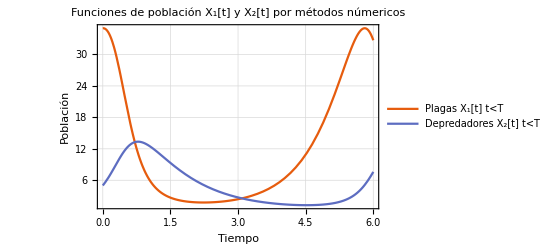

```mathematica
trueplot1=Plot[{pw1FromText,pw2FromText},{t,0,6},PlotTheme->"Scientific",PlotLegends->{"Plagas X_1[t] t<T","Depredadores X_2[t] t<T"},Frame->True,FrameLabel->{{"Población",None},{"Tiempo",None}},PlotLabel->"Funciones de población X_1[t] y X_2[t] por métodos númericos",GridLines->Automatic,PlotRange->All]
```

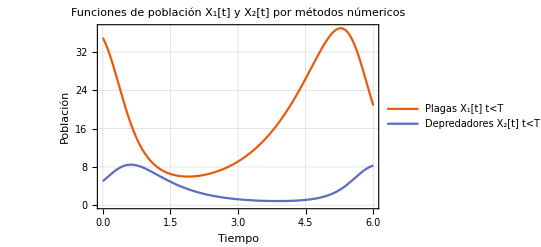

```mathematica
plotbasemetdnum=Plot[{x1Sol[t],x2Sol[t]},{t,0,6},PlotTheme->"Scientific",PlotLegends->{"Plagas X_1[t] t<T","Depredadores X_2[t] t<T"},Frame->True,FrameLabel->{{"Población",None},{"Tiempo",None}},PlotLabel->"Funciones de población X_1[t] y X_2[t] por métodos númericos",GridLines->Automatic]
```

### Análisis de Observabilidad y Controlabilidad del modelo base

### Observabilidad

```mathematica
obs1 = ObservabilityMatrix[ssbase]
obs1//MatrixForm
```

{{1,0},{0,-β/ϵ}}

(1 | 0
0 | -β/ϵ)

```mathematica
ObservableModelQ[ssbase]
```

True

### Controlabilidad

```mathematica
ctrl1 = ControllabilityMatrix[ssbase]
ctrl1//MatrixForm
```

{{0,0},{0,0}}

(0 | 0
0 | 0)

```mathematica
ControllableModelQ[ssbase]
```

False

### Valores númericos

Se va a asignar el tiempo de aplicación T=6.

```mathematica
(*x1T=x1Sol[6]*)
```

```mathematica
x1T=pw1FromText/.t->6
```

32.7116

```mathematica
(*x2T=x2Sol[6]*)
```

```mathematica
x2T=pw2FromText/.t->6
```

7.59711

```mathematica
simT=Join[simValues,{x1e->0.7*x1T}]
```

{α→1.5318,β→1,γ→0.3,ϵ→0.3,x1e→22.8982}

## Ecuaciones del modelo ampliado

```mathematica
f=- γ *x1* x2 - n *u *x1 + α x1
```

-n u x1+x1 α-x1 x2 γ

```mathematica
g=ϵ*γ *x1* x2 - β*x2- m *u *x2
```

-m u x2-x2 β+x1 x2 γ ϵ

### Puntos de Equilibrio

```mathematica
ue = (ϵ*γ*x1e-β) /m
```

(-β+x1e γ ϵ)/m

```mathematica
ue/.simT
```

1.06083/m

```mathematica
x2e = (α- n ue)/γ
```

(α-(n (-β+x1e γ ϵ))/m)/γ

```mathematica
x2e//Simplify
```

(m α+n β-n x1e γ ϵ)/(m γ)

```mathematica
x2e/.simT
```

3.33333 (1.5318-(1.06083 n)/m)

## Estabilidad

### Matriz A (Jacobiano evaluado en puntos de equilibrio)

```mathematica
A={{D[f,x1],D[f,x2]},{D[g,x1],D[g,x2]}}
```

{{-n u+α-x2 γ,-x1 γ},{x2 γ ϵ,-m u-β+x1 γ ϵ}}

```mathematica
Dimensions[A]
```

{2,2}

```mathematica
Ae=A /. {x1 -> x1e, x2->x2e,u->ue}
```

{{0,-x1e γ},{ϵ (α-(n (-β+x1e γ ϵ))/m),0}}

```mathematica
{{0,-x1e γ},{ϵ (α-(n (-β+x1e γ ϵ))/m),0}}
```

{{0,-x1e γ},{ϵ (α-(n (-β+x1e γ ϵ))/m),0}}

```mathematica
Ae//MatrixForm
```

(0 | -x1e γ
ϵ (α-(n (-β+x1e γ ϵ))/m) | 0)

### Autovalores, valores propios o eigenvalues

```mathematica
λ= Eigenvalues[Ae]
λ//MatrixForm
```

{-(ⅈ √x1e √γ √ϵ √(m α+n β-n x1e γ ϵ))/(√m),(ⅈ √x1e √γ √ϵ √(m α+n β-n x1e γ ϵ))/(√m)}

(-(ⅈ √x1e √γ √ϵ √(m α+n β-n x1e γ ϵ))/(√m)
(ⅈ √x1e √γ √ϵ √(m α+n β-n x1e γ ϵ))/(√m))

```mathematica
Expand[λ]
```

{-(ⅈ √x1e √γ √ϵ √(m α+n β-n x1e γ ϵ))/(√m),(ⅈ √x1e √γ √ϵ √(m α+n β-n x1e γ ϵ))/(√m)}

```mathematica
{λ[[1]],λ[[2]]}
```

{-(ⅈ √x1e √γ √ϵ √(m α+n β-n x1e γ ϵ))/(√m),(ⅈ √x1e √γ √ϵ √(m α+n β-n x1e γ ϵ))/(√m)}

## Representación en Espacio de Estados (State-space model)

### Matriz B

```mathematica
B={{D[f,u]},{D[g,u]}}
```

{{-n x1},{-m x2}}

```mathematica
Be = B /. {x1->x1e,x2->x2e}
```

{{-n x1e},{-(m (α-(n (-β+x1e γ ϵ))/m))/γ}}

```mathematica
Be//Simplify//MatrixForm
```

(-n x1e
-(m α+n β-n x1e γ ϵ)/γ)

### Matriz C

```mathematica
c=Transpose[{{1},{0}}]
```

{{1,0}}

```mathematica
{{1,0}}
```

{{1,0}}

### Verificación de dimensiones

```mathematica
Dimensions[Ae]
```

{2,2}

```mathematica
Dimensions[Be//MatrixForm]
```

{1}

```mathematica
Dimensions[c]
```

{1,2}

### Modelo en espacio de estados

```mathematica
ss = StateSpaceModel[{Ae,Be,c},SystemsModelLabels->{{"u"},{"y=x1"},{"x1","x2"}}]
```

0-x1e γ-n x1eϵ (α-(n (-β+x1e γ ϵ))/m)0-(m (α-(n (-β+x1e γ ϵ))/m))/γ100uy=x1x1x2StateSpaceModelTrueTrueTrueFalse$CellContext`stname1$CellContext`stname2uy=x1x1x2IdentityAutomatic112111213132TrueTrueFalseAutomaticuy=x1x1x2Automatic

## Análisis de Observabilidad y Controlabilidad

### Observabilidad

```mathematica
obs = ObservabilityMatrix[ss]
obs//MatrixForm
```

{{1,0},{0,-x1e γ}}

(1 | 0
0 | -x1e γ)

```mathematica
ObservableModelQ[ss]
```

True

### Controlabilidad

```mathematica
ctrl = ControllabilityMatrix[ss]
ctrl//Simplify//MatrixForm
```

{{-n x1e,m x1e α+n x1e β-n x1e^2 γ ϵ},{-(m (α-(n (-β+x1e γ ϵ))/m))/γ,-n x1e α ϵ-(n^2 x1e β ϵ)/m+(n^2 x1e^2 γ ϵ^2)/m}}

(-n x1e | x1e (m α+n (β-x1e γ ϵ))
-(m α+n β-n x1e γ ϵ)/γ | -(n x1e ϵ (m α+n (β-x1e γ ϵ)))/m)

```mathematica
ControllableModelQ[ss]
```

True

## Control por realimentación de estados

Control de la forma u= k*x
Condiciones dinámicas:
1. Overshoot < 10%
2. Tiempo de asentamiento t_s=2.6[t], dado q para el modelo de chacón se uso un pulso de 2.6,  se compara con el mismo tiempo.

```mathematica
ov = 0.1
```

0.1

```mathematica
ζ=(-Log[ov])/Sqrt[(Pi^2+Log[ov]^2)]
```

0.591155

```mathematica
ts=2.6
```

2.6

```mathematica
wn=4/(ζ*ts)
```

2.60247

```mathematica
λn1=-ζ*wn+I*wn*(Sqrt[1-(ζ^2)])
```

-1.53846+2.09904 ⅈ

```mathematica
λn2=-ζ*wn-I*wn*(Sqrt[1-(ζ^2)])
```

-1.53846-2.09904 ⅈ

```mathematica
λn={{λn1},{λn2}}
```

{{-1.53846+2.09904 ⅈ},{-1.53846-2.09904 ⅈ}}

### Ganancia de re-alimentación por Formula de Ackermann

```mathematica
poly=Expand[(s-λn1) (s-λn2)]
a1=Coefficient[poly,s,1]   (* =-(λn1+λn2)->real*)
a0=Coefficient[poly,s,0](* =λn1 λn2->real*)
```

(6.77284+0. ⅈ)+(3.07692+0. ⅈ) s+s^2

3.07692+0. ⅈ

6.77284+0. ⅈ

```mathematica
ϕA=MatrixPower[Ae,2]+(a1 Ae)+(a0 IdentityMatrix[2])
```

{{(6.77284+0. ⅈ)-x1e γ ϵ (α-(n (-β+x1e γ ϵ))/m),(0.+0. ⅈ)-(3.07692+0. ⅈ) x1e γ},{(0.+0. ⅈ)+(3.07692+0. ⅈ) ϵ (α-(n (-β+x1e γ ϵ))/m),(6.77284+0. ⅈ)-x1e γ ϵ (α-(n (-β+x1e γ ϵ))/m)}}

```mathematica
ϕA//MatrixForm
```

((6.77284+0. ⅈ)-x1e γ ϵ (α-(n (-β+x1e γ ϵ))/m) | (0.+0. ⅈ)-(3.07692+0. ⅈ) x1e γ
(0.+0. ⅈ)+(3.07692+0. ⅈ) ϵ (α-(n (-β+x1e γ ϵ))/m) | (6.77284+0. ⅈ)-x1e γ ϵ (α-(n (-β+x1e γ ϵ))/m))

```mathematica
Dimensions[ϕA]
```

{2,2}

```mathematica
K=Transpose[{{0},{1}}].Inverse[ctrl].ϕA
```

{{-(n x1e ((0.+0. ⅈ)+(3.07692+0. ⅈ) ϵ (α-(n (-β+x1e γ ϵ))/m)))/((m^2 x1e α^2)/γ+(2 m n x1e α β)/γ+(n^2 x1e β^2)/γ-2 m n x1e^2 α ϵ+n^2 x1e^2 α ϵ-2 n^2 x1e^2 β ϵ+(n^3 x1e^2 β ϵ)/m+n^2 x1e^3 γ ϵ^2-(n^3 x1e^3 γ ϵ^2)/m)+(m (α-(n (-β+x1e γ ϵ))/m) ((6.77284+0. ⅈ)-x1e γ ϵ (α-(n (-β+x1e γ ϵ))/m)))/(γ ((m^2 x1e α^2)/γ+(2 m n x1e α β)/γ+(n^2 x1e β^2)/γ-2 m n x1e^2 α ϵ+n^2 x1e^2 α ϵ-2 n^2 x1e^2 β ϵ+(n^3 x1e^2 β ϵ)/m+n^2 x1e^3 γ ϵ^2-(n^3 x1e^3 γ ϵ^2)/m)),(m ((0.+0. ⅈ)-(3.07692+0. ⅈ) x1e γ) (α-(n (-β+x1e γ ϵ))/m))/(γ ((m^2 x1e α^2)/γ+(2 m n x1e α β)/γ+(n^2 x1e β^2)/γ-2 m n x1e^2 α ϵ+n^2 x1e^2 α ϵ-2 n^2 x1e^2 β ϵ+(n^3 x1e^2 β ϵ)/m+n^2 x1e^3 γ ϵ^2-(n^3 x1e^3 γ ϵ^2)/m))-(n x1e ((6.77284+0. ⅈ)-x1e γ ϵ (α-(n (-β+x1e γ ϵ))/m)))/((m^2 x1e α^2)/γ+(2 m n x1e α β)/γ+(n^2 x1e β^2)/γ-2 m n x1e^2 α ϵ+n^2 x1e^2 α ϵ-2 n^2 x1e^2 β ϵ+(n^3 x1e^2 β ϵ)/m+n^2 x1e^3 γ ϵ^2-(n^3 x1e^3 γ ϵ^2)/m)}}

```mathematica
K//MatrixForm
```

(-(n x1e ((0.+0. ⅈ)+(3.07692+0. ⅈ) ϵ (α-(n (-β+x1e γ ϵ))/m)))/((m^2 x1e α^2)/γ+(2 m n x1e α β)/γ+(n^2 x1e β^2)/γ-2 m n x1e^2 α ϵ+n^2 x1e^2 α ϵ-2 n^2 x1e^2 β ϵ+(n^3 x1e^2 β ϵ)/m+n^2 x1e^3 γ ϵ^2-(n^3 x1e^3 γ ϵ^2)/m)+(m (α-(n (-β+x1e γ ϵ))/m) ((6.77284+0. ⅈ)-x1e γ ϵ (α-(n (-β+x1e γ ϵ))/m)))/(γ ((m^2 x1e α^2)/γ+(2 m n x1e α β)/γ+(n^2 x1e β^2)/γ-2 m n x1e^2 α ϵ+n^2 x1e^2 α ϵ-2 n^2 x1e^2 β ϵ+(n^3 x1e^2 β ϵ)/m+n^2 x1e^3 γ ϵ^2-(n^3 x1e^3 γ ϵ^2)/m)) | (m ((0.+0. ⅈ)-(3.07692+0. ⅈ) x1e γ) (α-(n (-β+x1e γ ϵ))/m))/(γ ((m^2 x1e α^2)/γ+(2 m n x1e α β)/γ+(n^2 x1e β^2)/γ-2 m n x1e^2 α ϵ+n^2 x1e^2 α ϵ-2 n^2 x1e^2 β ϵ+(n^3 x1e^2 β ϵ)/m+n^2 x1e^3 γ ϵ^2-(n^3 x1e^3 γ ϵ^2)/m))-(n x1e ((6.77284+0. ⅈ)-x1e γ ϵ (α-(n (-β+x1e γ ϵ))/m)))/((m^2 x1e α^2)/γ+(2 m n x1e α β)/γ+(n^2 x1e β^2)/γ-2 m n x1e^2 α ϵ+n^2 x1e^2 α ϵ-2 n^2 x1e^2 β ϵ+(n^3 x1e^2 β ϵ)/m+n^2 x1e^3 γ ϵ^2-(n^3 x1e^3 γ ϵ^2)/m))

```mathematica
Dimensions[K]
```

{1,2}

## Valores numéricos de simulación

Se simula que n sea mayor a m.
n=1
m=n/2

```mathematica
x1T
0.7x1T
x2T
```

32.7116

22.8982

7.59711

### Caso : n=1 y m=n/2

```mathematica
sim2=Join[simT,{n->1},{m->1/2}]
```

{α→1.5318,β→1,γ→0.3,ϵ→0.3,x1e→22.8982,n→1,m→1/2}

```mathematica
ssnumCaso1=ss/.sim2
```

0-6.86945-22.8982-0.1769600.983112100uy=x1x1x2StateSpaceModelTrueTrueTrueFalse$CellContext`stname1$CellContext`stname2uy=x1x1x2IdentityAutomatic112111213132TrueTrueFalseAutomaticuy=x1x1x2Automatic

```mathematica
λ/.sim2
```

{1.10255+0. ⅈ,-1.10255+0. ⅈ}

```mathematica
KnumCaso1=Chop[K/.sim2]
```

{{-0.0535645,1.88218}}

#### Evaluando KnumCaso1 en el sistema:

```mathematica
f1caso1[t]=- γ *x1c1[t]* x2c1[t] - n *((Part[KnumCaso1,1][[1]])*x1c1[t])*x1c1[t] + α*x1c1[t]
```

α x1c1[t]+0.0535645 n x1c1[t]^2-γ x1c1[t] x2c1[t]

```mathematica
g1caso1[t]=ϵ*γ *x1c1[t]* x2c1[t] - β*x2c1[t]- m *((Part[KnumCaso1,1][[2]])*x2c1[t]) *x2c1[t]
```

-β x2c1[t]+γ ϵ x1c1[t] x2c1[t]-1.88218 m x2c1[t]^2

```mathematica
sol1NumCaso1=NDSolve[{f1caso1[t]==D[x1c1[t],t],g1caso1[t]==D[x2c1[t],t],x1c1[6]==x1T,x2c1[6]==x2T,α==1.5318,β==1,γ==0.3,ϵ==0.3,n==1,m==1/2},{x1c1,x2c1},{t,6,8.6}]
```

{{x1c1→InterpolatingFunction[…],x2c1→InterpolatingFunction[…]}}

```mathematica
x11c1Sol=x1c1/. sol1NumCaso1[[1]]
x21c1Sol=x2c1/. sol1NumCaso1[[1]]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

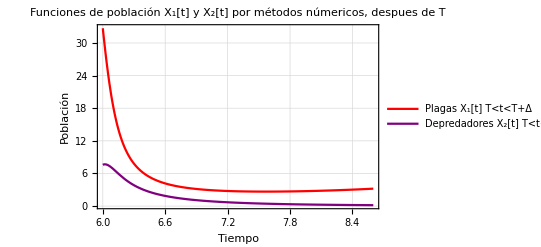

```mathematica
plot1Caso1=Plot[{x11c1Sol[t],x21c1Sol[t]},{t,6,8.6},PlotTheme->"Scientific",PlotLegends->{"Plagas X_1[t] T<t<T+Δ","Depredadores X_2[t] T<t<T+Δ"},Frame->True,FrameLabel->{{"Población",None},{"Tiempo",None}},PlotLabel->"Funciones de población X_1[t] y X_2[t] por métodos númericos, despues de T",PlotStyle->{Red,Purple},GridLines->Automatic,PlotRange->All]
```

#### Exportar e importar funciones piecewise del feedback y señales de control

```mathematica
pwx1feedback=InterpolationToPiecewise[x11c1Sol,t]
pwx2feedback=InterpolationToPiecewise[x21c1Sol,t]

Export["dir\\fpw1feedback.txt",ToString[pwx1feedback,InputForm]]
Export["dir\\fpw2feedback.txt",ToString[pwx2feedback,InputForm]]

pw1fbFromText=ToExpression[Import["dir\\fpw1feedback_1.txt"] ]
pw2fbFromText=ToExpression[Import["dir\\fpw2feedback_1.txt"]]
```

Piecewise[{{32.7081+(-181.376+(-0.0000788932-2.10584×10^7 (-6.+t)) (-6.00002+t)) (-6.00002+t), t<6.00002}, {32.7046+(-181.368+(-0.000068993-2.10787×10^7 (-6.00002+t)) (-6.00004+t)) (-6.00004+t), t<6.00004}, {32.6976+(-181.352+(203.884+4.01386 (-6.00004+t)) (-6.00008+t)) (-6.00008+t), t<6.00008}, {32.6906+(-181.336+(204.276-1.53573 (-6.00008+t)) (-6.00012+t)) (-6.00012+t), t<6.00012}, {32.6836+(-181.32+(204.667-1.63297 (-6.00012+t)) (-6.00015+t)) (-6.00015+t), t<6.00015}, {32.6136+(-181.161+(207.498+3540.23 (-6.00015+t)) (-6.00054+t)) (-6.00054+t), t<6.00054}, {32.5436+(-180.998+(211.339+3345.65 (-6.00054+t)) (-6.00093+t)) (-6.00093+t), t<6.00093}, {32.4737+(-180.832+(215.179+3316.56 (-6.00093+t)) (-6.00131+t)) (-6.00131+t), t<6.00131}, {32.4038+(-180.663+(218.985+3287.4 (-6.00131+t)) (-6.0017+t)) (-6.0017+t), t<6.0017}, {31.8658+(-179.261+(239.225+3150.65 (-6.0017+t)) (-6.00469+t)) (-6.00469+t), t<6.00469}, {31.3322+(-177.696+(266.057+2911.94 (-6.00469+t)) (-6.00768+t)) (-6.00768+t), t<6.00768}, {30.8036+(-175.981+(290.888+2692.27 (-6.00768+t)) (-6.01067+t)) (-6.01067+t), t<6.01067}, {30.2802+(-174.128+(313.698+2468.38 (-6.01067+t)) (-6.01366+t)) (-6.01366+t), t<6.01366}, {29.7626+(-172.148+(334.524+2248.17 (-6.01366+t)) (-6.01665+t)) (-6.01665+t), t<6.01665}, {28.9607+(-168.805+(360.045+1972.27 (-6.01665+t)) (-6.02135+t)) (-6.02135+t), t<6.02135}, {28.1751+(-165.221+(384.848+1651.05 (-6.02135+t)) (-6.02605+t)) (-6.02605+t), t<6.02605}, {27.4068+(-161.438+(405.255+1345.52 (-6.02605+t)) (-6.03076+t)) (-6.03076+t), t<6.03076}, {26.6567+(-157.496+(421.551+1060.96 (-6.03076+t)) (-6.03546+t)) (-6.03546+t), t<6.03546}, {25.9254+(-153.431+(434.037+798.433 (-6.03546+t)) (-6.04016+t)) (-6.04016+t), t<6.04016}, {25.2135+(-149.276+(443.029+558.619 (-6.04016+t)) (-6.04487+t)) (-6.04487+t), t<6.04487}, {24.3272+(-143.85+(449.575+312.941 (-6.04487+t)) (-6.05092+t)) (-6.05092+t), t<6.05092}, {23.4739+(-138.383+(452.285+71.7109 (-6.05092+t)) (-6.05696+t)) (-6.05696+t), t<6.05696}, {22.6536+(-132.923+(451.043-134.506 (-6.05696+t)) (-6.06301+t)) (-6.06301+t), t<6.06301}, {21.8662+(-127.513+(446.474-307.028 (-6.06301+t)) (-6.06906+t)) (-6.06906+t), t<6.06906}, {21.1114+(-122.185+(439.154-448.644 (-6.06906+t)) (-6.0751+t)) (-6.0751+t), t<6.0751}, {20.3884+(-116.969+(429.607-562.443 (-6.0751+t)) (-6.08115+t)) (-6.08115+t), t<6.08115}, {19.6965+(-111.887+(418.298-651.48 (-6.08115+t)) (-6.0872+t)) (-6.0872+t), t<6.0872}, {18.8448+(-105.525+(402.998-726.821 (-6.0872+t)) (-6.09503+t)) (-6.09503+t), t<6.09503}, {18.0418+(-99.4433+(384.979-783.497 (-6.09503+t)) (-6.10287+t)) (-6.10287+t), t<6.10287}, {17.2853+(-93.6562+(366.03-815.106 (-6.10287+t)) (-6.11071+t)) (-6.11071+t), t<6.11071}, {16.5731+(-88.172+(346.658-826.818 (-6.11071+t)) (-6.11854+t)) (-6.11854+t), t<6.11854}, {15.9026+(-82.9921+(327.26-823.07 (-6.11854+t)) (-6.12638+t)) (-6.12638+t), t<6.12638}, {15.2715+(-78.1128+(308.138-807.607 (-6.12638+t)) (-6.13422+t)) (-6.13422+t), t<6.13422}, {14.6775+(-73.5269+(289.519-783.541 (-6.13422+t)) (-6.14205+t)) (-6.14205+t), t<6.14205}, {14.0506+(-68.7046+(270.105-751.31 (-6.14205+t)) (-6.15087+t)) (-6.15087+t), t<6.15087}, {13.4647+(-64.2239+(250.91-712.297 (-6.15087+t)) (-6.15969+t)) (-6.15969+t), t<6.15969}, {12.9169+(-60.066+(232.794-670.696 (-6.15969+t)) (-6.16851+t)) (-6.16851+t), t<6.16851}, {12.4045+(-56.2111+(215.801-628.015 (-6.16851+t)) (-6.17733+t)) (-6.17733+t), t<6.17733}, {11.9247+(-52.6393+(199.938-585.415 (-6.17733+t)) (-6.18615+t)) (-6.18615+t), t<6.18615}, {11.4753+(-49.3308+(185.187-543.769 (-6.18615+t)) (-6.19496+t)) (-6.19496+t), t<6.19496}, {11.054+(-46.2667+(171.511-503.694 (-6.19496+t)) (-6.20378+t)) (-6.20378+t), t<6.20378}, {10.6586+(-43.4287+(158.862-465.57 (-6.20378+t)) (-6.2126+t)) (-6.2126+t), t<6.2126}, {10.1558+(-39.8766+(144.467-423.253 (-6.2126+t)) (-6.22468+t)) (-6.22468+t), t<6.22468}, {9.6938+(-36.6752+(130.223-378.336 (-6.22468+t)) (-6.23676+t)) (-6.23676+t), t<6.23676}, {9.2685+(-33.787+(117.503-337.737 (-6.23676+t)) (-6.24884+t)) (-6.24884+t), t<6.24884}, {8.87637+(-31.1784+(106.153-301.295 (-6.24884+t)) (-6.26092+t)) (-6.26092+t), t<6.26092}, {8.51422+(-28.8191+(96.0287-268.743 (-6.26092+t)) (-6.273+t)) (-6.273+t), t<6.273}, {8.17921+(-26.6822+(86.9974-239.771 (-6.273+t)) (-6.28508+t)) (-6.28508+t), t<6.28508}, {7.86878+(-24.7439+(78.9368-214.045 (-6.28508+t)) (-6.29716+t)) (-6.29716+t), t<6.29716}, {7.58068+(-22.9828+(71.7374-191.239 (-6.29716+t)) (-6.30924+t)) (-6.30924+t), t<6.30924}, {7.24442+(-20.976+(64.2372-168.546 (-6.30924+t)) (-6.32455+t)) (-6.32455+t), t<6.32455}, {6.93716+(-19.1906+(57.1771-146.59 (-6.32455+t)) (-6.33987+t)) (-6.33987+t), t<6.33987}, {6.65573+(-17.5979+(51.0285-127.765 (-6.33987+t)) (-6.35518+t)) (-6.35518+t), t<6.35518}, {6.39737+(-16.1733+(45.6614-111.614 (-6.35518+t)) (-6.37049+t)) (-6.37049+t), t<6.37049}, {6.15967+(-14.8958+(40.9655-97.7385 (-6.37049+t)) (-6.3858+t)) (-6.3858+t), t<6.3858}, {5.94052+(-13.7473+(36.8468-85.7978 (-6.3858+t)) (-6.40112+t)) (-6.40112+t), t<6.40112}, {5.73808+(-12.7121+(33.2254-75.5035 (-6.40112+t)) (-6.41643+t)) (-6.41643+t), t<6.41643}, {5.55071+(-11.7767+(30.0333-66.6099 (-6.41643+t)) (-6.43174+t)) (-6.43174+t), t<6.43174}, {5.33308+(-10.7186+(26.7547-57.987 (-6.43174+t)) (-6.45111+t)) (-6.45111+t), t<6.45111}, {5.13474+(-9.78161+(23.707-49.836 (-6.45111+t)) (-6.47048+t)) (-6.47048+t), t<6.47048}, {4.95352+(-8.94891+(21.0811-42.9957 (-6.47048+t)) (-6.48984+t)) (-6.48984+t), t<6.48984}, {4.78753+(-8.20634+(18.81-37.233 (-6.48984+t)) (-6.50921+t)) (-6.50921+t), t<6.50921}, {4.63514+(-7.54196+(16.8387-32.3603 (-6.50921+t)) (-6.52858+t)) (-6.52858+t), t<6.52858}, {4.49495+(-6.94565+(15.1213-28.2243 (-6.52858+t)) (-6.54795+t)) (-6.54795+t), t<6.54795}, {4.36572+(-6.40881+(13.6201-24.701 (-6.54795+t)) (-6.56731+t)) (-6.56731+t), t<6.56731}, {4.24637+(-5.9241+(12.3035-21.6886 (-6.56731+t)) (-6.58668+t)) (-6.58668+t), t<6.58668}, {4.11075+(-5.38637+(10.9752-18.826 (-6.58668+t)) (-6.61069+t)) (-6.61069+t), t<6.61069}, {3.9873+(-4.90899+(9.74993-16.1608 (-6.61069+t)) (-6.63469+t)) (-6.63469+t), t<6.63469}, {3.87467+(-4.48355+(8.69501-13.9352 (-6.63469+t)) (-6.65869+t)) (-6.65869+t), t<6.65869}, {3.77171+(-4.10297+(7.78284-12.0669 (-6.65869+t)) (-6.6827+t)) (-6.6827+t), t<6.6827}, {3.67739+(-3.76131+(6.99085-10.4915 (-6.6827+t)) (-6.7067+t)) (-6.7067+t), t<6.7067}, {3.59087+(-3.45357+(6.30052-9.15678 (-6.7067+t)) (-6.7307+t)) (-6.7307+t), t<6.7307}, {3.51136+(-3.17548+(5.69655-8.02125 (-6.7307+t)) (-6.75471+t)) (-6.75471+t), t<6.75471}, {3.43821+(-2.9234+(5.16626-7.05108 (-6.75471+t)) (-6.77871+t)) (-6.77871+t), t<6.77871}, {3.35374+(-2.63653+(4.62268-6.11925 (-6.77871+t)) (-6.80912+t)) (-6.80912+t), t<6.80912}, {3.27751+(-2.38113+(4.11853-5.24511 (-6.80912+t)) (-6.83954+t)) (-6.83954+t), t<6.83954}, {3.20862+(-2.15278+(3.68503-4.51747 (-6.83954+t)) (-6.86996+t)) (-6.86996+t), t<6.86996}, {3.14631+(-1.94778+(3.31056-3.90815 (-6.86996+t)) (-6.90037+t)) (-6.90037+t), t<6.90037}, {3.08993+(-1.76301+(2.98569-3.39537 (-6.90037+t)) (-6.93079+t)) (-6.93079+t), t<6.93079}, {3.03889+(-1.59585+(2.70271-2.96162 (-6.93079+t)) (-6.96121+t)) (-6.96121+t), t<6.96121}, {2.99269+(-1.44409+(2.45526-2.59298 (-6.96121+t)) (-6.99162+t)) (-6.99162+t), t<6.99162}, {2.9509+(-1.30584+(2.2381-2.27827 (-6.99162+t)) (-7.02204+t)) (-7.02204+t), t<7.02204}, {2.90303+(-1.14533+(2.01348-1.97393 (-7.02204+t)) (-7.06115+t)) (-7.06115+t), t<7.06115}, {2.8611+(-1.00159+(1.80478-1.68712 (-7.06115+t)) (-7.10025+t)) (-7.10025+t), t<7.10025}, {2.8245+(-0.87221+(1.62583-1.44892 (-7.10025+t)) (-7.13936+t)) (-7.13936+t), t<7.13936}, {2.79272+(-0.755189+(1.4717-1.24981 (-7.13936+t)) (-7.17847+t)) (-7.17847+t), t<7.17847}, {2.7653+(-0.648851+(1.33839-1.08247 (-7.17847+t)) (-7.21758+t)) (-7.21758+t), t<7.21758}, {2.74185+(-0.551781+(1.22265-0.94103 (-7.21758+t)) (-7.25669+t)) (-7.25669+t), t<7.25669}, {2.72203+(-0.462784+(1.1218-0.820874 (-7.25669+t)) (-7.29579+t)) (-7.29579+t), t<7.29579}, {2.70556+(-0.380838+(1.03365-0.718292 (-7.29579+t)) (-7.3349+t)) (-7.3349+t), t<7.3349}, {2.68873+(-0.283539+(0.942316-0.618551 (-7.3349+t)) (-7.38568+t)) (-7.38568+t), t<7.38568}, {2.67661+(-0.195061+(0.857867-0.524146 (-7.38568+t)) (-7.43646+t)) (-7.43646+t), t<7.43646}, {2.66879+(-0.11407+(0.786135-0.445728 (-7.43646+t)) (-7.48724+t)) (-7.48724+t), t<7.48724}, {2.66492+(-0.0394546+(0.72502-0.3801 (-7.48724+t)) (-7.53803+t)) (-7.53803+t), t<7.53803}, {2.66469+(0.029717+(0.672828-0.32482 (-7.53803+t)) (-7.58881+t)) (-7.58881+t), t<7.58881}, {2.66786+(0.0942338+(0.628185-0.277947 (-7.58881+t)) (-7.63959+t)) (-7.63959+t), t<7.63959}, {2.6742+(0.154766+(0.58997-0.237946 (-7.63959+t)) (-7.69037+t)) (-7.69037+t), t<7.69037}, {2.68352+(0.211888+(0.557263-0.203594 (-7.69037+t)) (-7.74115+t)) (-7.74115+t), t<7.74115}, {2.69998+(0.282357+(0.524146-0.169772 (-7.74115+t)) (-7.80766+t)) (-7.80766+t), t<7.80766}, {2.72099+(0.348763+(0.494675-0.137299 (-7.80766+t)) (-7.87416+t)) (-7.87416+t), t<7.87416}, {2.7463+(0.411896+(0.470986-0.109933 (-7.87416+t)) (-7.94067+t)) (-7.94067+t), t<7.94067}, {2.77572+(0.472429+(0.452207-0.0865994 (-7.94067+t)) (-8.00718+t)) (-8.00718+t), t<8.00718}, {2.80909+(0.530935+(0.437645-0.0664784 (-8.00718+t)) (-8.07368+t)) (-8.07368+t), t<8.07368}, {2.8463+(0.587915+(0.426749-0.0489166 (-8.07368+t)) (-8.14019+t)) (-8.14019+t), t<8.14019}, {2.88727+(0.643806+(0.41908-0.0333939 (-8.14019+t)) (-8.2067+t)) (-8.2067+t), t<8.2067}, {2.93192+(0.698997+(0.414286-0.0194939 (-8.2067+t)) (-8.2732+t)) (-8.2732+t), t<8.2732}, {2.99654+(0.771451+(0.411984-0.00497793 (-8.2732+t)) (-8.36109+t)) (-8.36109+t), t<8.36109}, {3.06753+(0.844028+(0.413337+0.0100291 (-8.36109+t)) (-8.44898+t)) (-8.44898+t), t<8.44898}, {3.13363+(0.906991+(0.417775+0.022925 (-8.44898+t)) (-8.52449+t)) (-8.52449+t), t<8.52449}, {3.20453+(0.970933+(0.424679+0.0342005 (-8.52449+t)) (-8.6+t)) (-8.6+t), True}}]

Piecewise[{{7.59727+(8.59192+(2.72015×10^-6+2.40688×10^7 (-6.+t)) (-6.00002+t)) (-6.00002+t), t<6.00002}, {7.59744+(8.58293+(2.25242×10^-6+2.40662×10^7 (-6.00002+t)) (-6.00004+t)) (-6.00004+t), t<6.00004}, {7.59777+(8.56496+(-232.499-0.182763 (-6.00004+t)) (-6.00008+t)) (-6.00008+t), t<6.00008}, {7.5981+(8.54699+(-232.448+0.0583131 (-6.00008+t)) (-6.00012+t)) (-6.00012+t), t<6.00012}, {7.59843+(8.52903+(-232.396+0.104773 (-6.00012+t)) (-6.00015+t)) (-6.00015+t), t<6.00015}, {7.60169+(8.34962+(-232.02+468.346 (-6.00015+t)) (-6.00054+t)) (-6.00054+t), t<6.00054}, {7.60488+(8.17062+(-231.497+453.547 (-6.00054+t)) (-6.00093+t)) (-6.00093+t), t<6.00093}, {7.60801+(7.99204+(-230.96+461.858 (-6.00093+t)) (-6.00131+t)) (-6.00131+t), t<6.00131}, {7.61106+(7.81387+(-230.414+470.077 (-6.00131+t)) (-6.0017+t)) (-6.0017+t), t<6.0017}, {7.63238+(6.45076+(-227.234+507.826 (-6.0017+t)) (-6.00469+t)) (-6.00469+t), t<6.00469}, {7.64966+(5.11646+(-222.326+568.747 (-6.00469+t)) (-6.00768+t)) (-6.00768+t), t<6.00768}, {7.663+(3.81382+(-216.956+617.358 (-6.00768+t)) (-6.01067+t)) (-6.01067+t), t<6.01067}, {7.67249+(2.54539+(-211.167+661.87 (-6.01067+t)) (-6.01366+t)) (-6.01366+t), t<6.01366}, {7.67825+(1.31341+(-205.014+700.46 (-6.01366+t)) (-6.01665+t)) (-6.01665+t), t<6.01665}, {7.68002+(-0.546701+(-195.995+741.119 (-6.01665+t)) (-6.02135+t)) (-6.02135+t), t<6.02135}, {7.67327+(-2.30598+(-185.195+775.586 (-6.02135+t)) (-6.02605+t)) (-6.02605+t), t<6.02605}, {7.65849+(-3.96021+(-173.962+803.056 (-6.02605+t)) (-6.03076+t)) (-6.03076+t), t<6.03076}, {7.63618+(-5.50676+(-162.483+817.215 (-6.03076+t)) (-6.03546+t)) (-6.03546+t), t<6.03546}, {7.60686+(-6.94447+(-150.904+820.954 (-6.03546+t)) (-6.04016+t)) (-6.04016+t), t<6.04016}, {7.57103+(-8.27345+(-139.357+815.661 (-6.04016+t)) (-6.04487+t)) (-6.04487+t), t<6.04487}, {7.51622+(-9.82433+(-125.82+800.065 (-6.04487+t)) (-6.05092+t)) (-6.05092+t), t<6.05092}, {7.45256+(-11.2025+(-111.617+773.491 (-6.05092+t)) (-6.05696+t)) (-6.05696+t), t<6.05696}, {7.38108+(-12.4148+(-98.011+737.996 (-6.05696+t)) (-6.06301+t)) (-6.06301+t), t<6.06301}, {7.30274+(-13.4696+(-85.1179+696.764 (-6.06301+t)) (-6.06906+t)) (-6.06906+t), t<6.06906}, {7.21848+(-14.3766+(-73.0204+651.703 (-6.06906+t)) (-6.0751+t)) (-6.0751+t), t<6.0751}, {7.12915+(-15.1457+(-61.7695+604.387 (-6.0751+t)) (-6.08115+t)) (-6.08115+t), t<6.08115}, {7.03557+(-15.7875+(-51.3891+556.179 (-6.08115+t)) (-6.0872+t)) (-6.0872+t), t<6.0872}, {6.90914+(-16.4472+(-40.1234+501.273 (-6.0872+t)) (-6.09503+t)) (-6.09503+t), t<6.09503}, {6.77823+(-16.9333+(-29.2889+441.072 (-6.09503+t)) (-6.10287+t)) (-6.10287+t), t<6.10287}, {6.64413+(-17.2675+(-19.8192+384.175 (-6.10287+t)) (-6.11071+t)) (-6.11071+t), t<6.11071}, {6.50793+(-17.4701+(-11.6236+331.37 (-6.11071+t)) (-6.11854+t)) (-6.11854+t), t<6.11854}, {6.3706+(-17.5595+(-4.59805+283.123 (-6.11854+t)) (-6.12638+t)) (-6.12638+t), t<6.12638}, {6.23296+(-17.5528+(1.36746+239.596 (-6.12638+t)) (-6.13422+t)) (-6.13422+t), t<6.13422}, {6.09569+(-17.4651+(6.38351+200.749 (-6.13422+t)) (-6.14205+t)) (-6.14205+t), t<6.14205}, {5.94241+(-17.2863+(10.8655+164.411 (-6.14205+t)) (-6.15087+t)) (-6.15087+t), t<6.15087}, {5.79102+(-17.0386+(14.6177+131.027 (-6.15087+t)) (-6.15969+t)) (-6.15969+t), t<6.15969}, {5.64206+(-16.7366+(17.5747+102.552 (-6.15969+t)) (-6.16851+t)) (-6.16851+t), t<6.16851}, {5.49596+(-16.3925+(19.8556+78.4214 (-6.16851+t)) (-6.17733+t)) (-6.17733+t), t<6.17733}, {5.35304+(-16.0167+(21.5659+58.1116 (-6.17733+t)) (-6.18615+t)) (-6.18615+t), t<6.18615}, {5.21354+(-15.6178+(22.7986+41.1424 (-6.18615+t)) (-6.19496+t)) (-6.19496+t), t<6.19496}, {5.07764+(-15.2031+(23.6341+27.0665 (-6.19496+t)) (-6.20378+t)) (-6.20378+t), t<6.20378}, {4.94543+(-14.7785+(24.1417+15.478 (-6.20378+t)) (-6.2126+t)) (-6.2126+t), t<6.2126}, {4.77046+(-14.1897+(24.3993+4.50128 (-6.2126+t)) (-6.22468+t)) (-6.22468+t), t<6.22468}, {4.60261+(-13.6013+(24.3208-5.21204 (-6.22468+t)) (-6.23676+t)) (-6.23676+t), t<6.23676}, {4.44182+(-13.0208+(23.9542-12.334 (-6.23676+t)) (-6.24884+t)) (-6.24884+t), t<6.24884}, {4.28797+(-12.4534+(23.3799-17.4237 (-6.24884+t)) (-6.26092+t)) (-6.26092+t), t<6.26092}, {4.14088+(-11.9028+(22.6602-20.9333 (-6.26092+t)) (-6.273+t)) (-6.273+t), t<6.273}, {4.00032+(-11.3717+(21.8436-23.225 (-6.273+t)) (-6.28508+t)) (-6.28508+t), t<6.28508}, {3.86605+(-10.8616+(20.967-24.585 (-6.28508+t)) (-6.29716+t)) (-6.29716+t), t<6.29716}, {3.73781+(-10.3733+(20.0587-25.2404 (-6.29716+t)) (-6.30924+t)) (-6.30924+t), t<6.30924}, {3.58351+(-9.78617+(18.9761-25.3436 (-6.30924+t)) (-6.32455+t)) (-6.32455+t), t<6.32455}, {3.43793+(-9.23449+(17.8233-24.9131 (-6.32455+t)) (-6.33987+t)) (-6.33987+t), t<6.33987}, {3.30053+(-8.71731+(16.7031-24.0854 (-6.33987+t)) (-6.35518+t)) (-6.35518+t), t<6.35518}, {3.1708+(-8.23328+(15.6289-23.0111 (-6.35518+t)) (-6.37049+t)) (-6.37049+t), t<6.37049}, {3.04823+(-7.78078+(14.6087-21.7947 (-6.37049+t)) (-6.3858+t)) (-6.3858+t), t<6.3858}, {2.93236+(-7.35804+(13.6466-20.5106 (-6.3858+t)) (-6.40112+t)) (-6.40112+t), t<6.40112}, {2.82275+(-6.96325+(12.7442-19.2105 (-6.40112+t)) (-6.41643+t)) (-6.41643+t), t<6.41643}, {2.71898+(-6.59457+(11.901-17.9294 (-6.41643+t)) (-6.43174+t)) (-6.43174+t), t<6.43174}, {2.5955+(-6.16293+(10.9835-16.5293 (-6.43174+t)) (-6.45111+t)) (-6.45111+t), t<6.45111}, {2.48003+(-5.76682+(10.0805-15.0556 (-6.45111+t)) (-6.47048+t)) (-6.47048+t), t<6.47048}, {2.37191+(-5.40303+(9.25906-13.6875 (-6.47048+t)) (-6.48984+t)) (-6.48984+t), t<6.48984}, {2.27055+(-5.06863+(8.51283-12.4312 (-6.48984+t)) (-6.50921+t)) (-6.50921+t), t<6.50921}, {2.1754+(-4.7609+(7.83533-11.2851 (-6.50921+t)) (-6.52858+t)) (-6.52858+t), t<6.52858}, {2.08598+(-4.47737+(7.22031-10.2448 (-6.52858+t)) (-6.54795+t)) (-6.54795+t), t<6.54795}, {2.00183+(-4.21584+(6.66188-9.30362 (-6.54795+t)) (-6.56731+t)) (-6.56731+t), t<6.56731}, {1.92255+(-3.97427+(6.15456-8.45405 (-6.56731+t)) (-6.58668+t)) (-6.58668+t), t<6.58668}, {1.8305+(-3.69989+(5.62429-7.6026 (-6.58668+t)) (-6.61069+t)) (-6.61069+t), t<6.61069}, {1.74473+(-3.45032+(5.11736-6.76879 (-6.61069+t)) (-6.63469+t)) (-6.63469+t), t<6.63469}, {1.66469+(-3.22286+(4.66554-6.03642 (-6.63469+t)) (-6.65869+t)) (-6.65869+t), t<6.65869}, {1.58986+(-3.01515+(4.26214-5.39314 (-6.65869+t)) (-6.6827+t)) (-6.6827+t), t<6.6827}, {1.5198+(-2.82508+(3.90127-4.82757 (-6.6827+t)) (-6.7067+t)) (-6.7067+t), t<6.7067}, {1.45411+(-2.65082+(3.57784-4.32975 (-6.7067+t)) (-6.7307+t)) (-6.7307+t), t<6.7307}, {1.39243+(-2.49076+(3.28739-3.89096 (-6.7307+t)) (-6.75471+t)) (-6.75471+t), t<6.75471}, {1.33443+(-2.34347+(3.02603-3.50358 (-6.75471+t)) (-6.77871+t)) (-6.77871+t), t<6.77871}, {1.26579+(-2.17322+(2.75125-3.11893 (-6.77871+t)) (-6.80912+t)) (-6.80912+t), t<6.80912}, {1.20206+(-2.01923+(2.48968-2.74621 (-6.80912+t)) (-6.83954+t)) (-6.83954+t), t<6.83954}, {1.14281+(-1.87957+(2.25889-2.42546 (-6.83954+t)) (-6.86996+t)) (-6.86996+t), t<6.86996}, {1.0876+(-1.75259+(2.05467-2.14857 (-6.86996+t)) (-6.90037+t)) (-6.90037+t), t<6.90037}, {1.03608+(-1.63686+(1.87341-1.90884 (-6.90037+t)) (-6.93079+t)) (-6.93079+t), t<6.93079}, {0.987921+(-1.53114+(1.71207-1.70062 (-6.93079+t)) (-6.96121+t)) (-6.96121+t), t<6.96121}, {0.942843+(-1.43434+(1.56808-1.51925 (-6.96121+t)) (-6.99162+t)) (-6.99162+t), t<6.99162}, {0.900585+(-1.34553+(1.43922-1.36079 (-6.99162+t)) (-7.02204+t)) (-7.02204+t), t<7.02204}, {0.85003+(-1.24176+(1.30315-1.20387 (-7.02204+t)) (-7.06115+t)) (-7.06115+t), t<7.06115}, {0.803326+(-1.14833+(1.17395-1.05249 (-7.06115+t)) (-7.10025+t)) (-7.10025+t), t<7.10025}, {0.760095+(-1.06396+(1.06071-0.923683 (-7.10025+t)) (-7.13936+t)) (-7.13936+t), t<7.13936}, {0.720004+(-0.987539+(0.961089-0.813594 (-7.13936+t)) (-7.17847+t)) (-7.17847+t), t<7.17847}, {0.682762+(-0.918146+(0.87314-0.719119 (-7.17847+t)) (-7.21758+t)) (-7.21758+t), t<7.21758}, {0.64811+(-0.854972+(0.795234-0.637718 (-7.21758+t)) (-7.25669+t)) (-7.25669+t), t<7.25669}, {0.615819+(-0.797319+(0.726002-0.567313 (-7.25669+t)) (-7.29579+t)) (-7.29579+t), t<7.29579}, {0.585683+(-0.744587+(0.664292-0.506195 (-7.29579+t)) (-7.3349+t)) (-7.3349+t), t<7.3349}, {0.549475+(-0.682606+(0.59896-0.44575 (-7.3349+t)) (-7.38568+t)) (-7.38568+t), t<7.38568}, {0.516248+(-0.627061+(0.537065-0.387596 (-7.38568+t)) (-7.43646+t)) (-7.43646+t), t<7.43646}, {0.485695+(-0.577124+(0.483092-0.338482 (-7.43646+t)) (-7.48724+t)) (-7.48724+t), t<7.48724}, {0.45755+(-0.532095+(0.435832-0.29678 (-7.48724+t)) (-7.53803+t)) (-7.53803+t), t<7.53803}, {0.431581+(-0.491376+(0.394292-0.261203 (-7.53803+t)) (-7.58881+t)) (-7.58881+t), t<7.58881}, {0.407581+(-0.454458+(0.357644-0.230711 (-7.58881+t)) (-7.63959+t)) (-7.63959+t), t<7.63959}, {0.385368+(-0.420902+(0.325203-0.204463 (-7.63959+t)) (-7.69037+t)) (-7.69037+t), t<7.69037}, {0.364782+(-0.390331+(0.296393-0.181773 (-7.69037+t)) (-7.74115+t)) (-7.74115+t), t<7.74115}, {0.340046+(-0.354266+(0.265838-0.159327 (-7.74115+t)) (-7.80766+t)) (-7.80766+t), t<7.80766}, {0.317573+(-0.322137+(0.236972-0.137755 (-7.80766+t)) (-7.87416+t)) (-7.87416+t), t<7.87416}, {0.297122+(-0.293416+(0.211942-0.119629 (-7.87416+t)) (-7.94067+t)) (-7.94067+t), t<7.94067}, {0.278479+(-0.267663+(0.190147-0.104304 (-7.94067+t)) (-8.00718+t)) (-8.00718+t), t<8.00718}, {0.261462+(-0.244501+(0.171098-0.0912797 (-8.00718+t)) (-8.07368+t)) (-8.07368+t), t<8.07368}, {0.245907+(-0.223611+(0.15439-0.0801512 (-8.07368+t)) (-8.14019+t)) (-8.14019+t), t<8.14019}, {0.231674+(-0.204718+(0.139689-0.0705947 (-8.14019+t)) (-8.2067+t)) (-8.2067+t), t<8.2067}, {0.218638+(-0.187587+(0.126717-0.0623489 (-8.2067+t)) (-8.2732+t)) (-8.2732+t), t<8.2732}, {0.203061+(-0.167309+(0.112984-0.0541646 (-8.2732+t)) (-8.36109+t)) (-8.36109+t), t<8.36109}, {0.189162+(-0.149354+(0.100115-0.0462771 (-8.36109+t)) (-8.44898+t)) (-8.44898+t), t<8.44898}, {0.178414+(-0.135526+(0.0900519-0.0400688 (-8.44898+t)) (-8.52449+t)) (-8.52449+t), t<8.52449}, {0.168662+(-0.122982+(0.0817292-0.0351438 (-8.52449+t)) (-8.6+t)) (-8.6+t), True}}]

Piecewise[{{32.7079+(-214.914+(-0.000250847-1.59852×10^8 (-6.+t)) (-6.00002+t)) (-6.00002+t), t<6.00002}, {32.7041+(-214.865+(0.000360991-1.59803×10^8 (-6.00002+t)) (-6.00003+t)) (-6.00003+t), t<6.00003}, {32.6297+(-213.898+(1392.38+0.00320898 (-6.00003+t)) (-6.00038+t)) (-6.00038+t), t<6.00038}, {32.5556+(-212.937+(1383.87-0.00621451 (-6.00038+t)) (-6.00073+t)) (-6.00073+t), t<6.00073}, {32.4818+(-211.982+(1375.42+0.00289402 (-6.00073+t)) (-6.00108+t)) (-6.00108+t), t<6.00108}, {32.2622+(-209.148+(1353.82-9395.78 (-6.00108+t)) (-6.00212+t)) (-6.00212+t), t<6.00212}, {32.0456+(-206.366+(1329.98-7872.89 (-6.00212+t)) (-6.00316+t)) (-6.00316+t), t<6.00316}, {31.8318+(-203.634+(1305.98-7701.54 (-6.00316+t)) (-6.00421+t)) (-6.00421+t), t<6.00421}, {31.6209+(-200.951+(1282.5-7533.4 (-6.00421+t)) (-6.00525+t)) (-6.00525+t), t<6.00525}, {31.2072+(-195.728+(1244.58-7204.6 (-6.00525+t)) (-6.00733+t)) (-6.00733+t), t<6.00733}, {30.8043+(-190.689+(1200.8-6867.55 (-6.00733+t)) (-6.00942+t)) (-6.00942+t), t<6.00942}, {30.4117+(-185.827+(1158.82-6601.9 (-6.00942+t)) (-6.0115+t)) (-6.0115+t), t<6.0115}, {30.0291+(-181.133+(1118.66-6322.1 (-6.0115+t)) (-6.01359+t)) (-6.01359+t), t<6.01359}, {29.656+(-176.601+(1080.19-6055.71 (-6.01359+t)) (-6.01568+t)) (-6.01568+t), t<6.01568}, {28.9121+(-167.693+(1018.08-5670.14 (-6.01568+t)) (-6.02+t)) (-6.02+t), t<6.02}, {28.2054+(-159.395+(948.607-5207.55 (-6.02+t)) (-6.02432+t)) (-6.02432+t), t<6.02432}, {27.5333+(-151.655+(884.953-4770.59 (-6.02432+t)) (-6.02864+t)) (-6.02864+t), t<6.02864}, {26.8935+(-144.428+(826.52-4379.61 (-6.02864+t)) (-6.03297+t)) (-6.03297+t), t<6.03297}, {26.284+(-137.671+(772.825-4025.88 (-6.03297+t)) (-6.03729+t)) (-6.03729+t), t<6.03729}, {25.7027+(-131.347+(723.429-3705.09 (-6.03729+t)) (-6.04161+t)) (-6.04161+t), t<6.04161}, {24.9676+(-123.521+(668.344-3368.34 (-6.04161+t)) (-6.04738+t)) (-6.04738+t), t<6.04738}, {24.2758+(-116.334+(614.054-3023.69 (-6.04738+t)) (-6.05315+t)) (-6.05315+t), t<6.05315}, {23.6238+(-109.72+(565.213-2722.29 (-6.05315+t)) (-6.05892+t)) (-6.05892+t), t<6.05892}, {23.0085+(-103.622+(521.192-2455.66 (-6.05892+t)) (-6.0647+t)) (-6.0647+t), t<6.0647}, {22.427+(-97.9919+(481.438-2219.26 (-6.0647+t)) (-6.07047+t)) (-6.07047+t), t<6.07047}, {21.8767+(-92.7836+(445.465-2009.44 (-6.07047+t)) (-6.07624+t)) (-6.07624+t), t<6.07624}, {21.3554+(-87.9579+(412.853-1822.92 (-6.07624+t)) (-6.08201+t)) (-6.08201+t), t<6.08201}, {20.6818+(-81.8823+(376.317-1627.81 (-6.08201+t)) (-6.08994+t)) (-6.08994+t), t<6.08994}, {20.0542+(-76.3843+(340.709-1432.15 (-6.08994+t)) (-6.09788+t)) (-6.09788+t), t<6.09788}, {19.4681+(-71.3951+(309.314-1264.11 (-6.09788+t)) (-6.10582+t)) (-6.10582+t), t<6.10582}, {18.9198+(-66.8558+(281.545-1119.31 (-6.10582+t)) (-6.11375+t)) (-6.11375+t), t<6.11375}, {18.4059+(-62.7155+(256.908-994.094 (-6.11375+t)) (-6.12169+t)) (-6.12169+t), t<6.12169}, {17.9234+(-58.9299+(234.986-885.452 (-6.12169+t)) (-6.12962+t)) (-6.12962+t), t<6.12962}, {17.4697+(-55.4608+(215.424-790.885 (-6.12962+t)) (-6.13756+t)) (-6.13756+t), t<6.13756}, {16.9622+(-51.6857+(195.811-700.958 (-6.13756+t)) (-6.14704+t)) (-6.14704+t), t<6.14704}, {16.4887+(-48.2654+(177.497-616.884 (-6.14704+t)) (-6.15652+t)) (-6.15652+t), t<6.15652}, {16.0462+(-45.1577+(161.349-544.624 (-6.15652+t)) (-6.166+t)) (-6.166+t), t<6.166}, {15.6318+(-42.3264+(147.06-482.399 (-6.166+t)) (-6.17548+t)) (-6.17548+t), t<6.17548}, {15.243+(-39.7404+(134.377-428.66 (-6.17548+t)) (-6.18496+t)) (-6.18496+t), t<6.18496}, {14.8777+(-37.3728+(123.083-382.081 (-6.18496+t)) (-6.19443+t)) (-6.19443+t), t<6.19443}, {14.5339+(-35.1999+(112.997-341.549 (-6.19443+t)) (-6.20391+t)) (-6.20391+t), t<6.20391}, {14.2098+(-33.2015+(103.965-306.163 (-6.20391+t)) (-6.21339+t)) (-6.21339+t), t<6.21339}, {13.7753+(-30.5979+(93.6651-269.021 (-6.21339+t)) (-6.22702+t)) (-6.22702+t), t<6.22702}, {13.3744+(-28.273+(83.694-231.933 (-6.22702+t)) (-6.24066+t)) (-6.24066+t), t<6.24066}, {13.0034+(-26.1889+(75.0699-200.932 (-6.24066+t)) (-6.25429+t)) (-6.25429+t), t<6.25429}, {12.6594+(-24.3141+(67.576-174.872 (-6.25429+t)) (-6.26792+t)) (-6.26792+t), t<6.26792}, {12.3397+(-22.6216+(61.0353-152.851 (-6.26792+t)) (-6.28155+t)) (-6.28155+t), t<6.28155}, {12.0419+(-21.089+(55.3028-134.148 (-6.28155+t)) (-6.29518+t)) (-6.29518+t), t<6.29518}, {11.7641+(-19.6968+(50.2589-118.187 (-6.29518+t)) (-6.30881+t)) (-6.30881+t), t<6.30881}, {11.5044+(-18.4285+(45.8045-104.505 (-6.30881+t)) (-6.32245+t)) (-6.32245+t), t<6.32245}, {11.2018+(-16.9915+(41.2393-91.3775 (-6.32245+t)) (-6.33955+t)) (-6.33955+t), t<6.33955}, {10.9224+(-15.7037+(36.9816-79.0453 (-6.33955+t)) (-6.35664+t)) (-6.35664+t), t<6.35664}, {10.664+(-14.5453+(33.2868-68.7081 (-6.35664+t)) (-6.37374+t)) (-6.37374+t), t<6.37374}, {10.4244+(-13.4995+(30.0656-59.9897 (-6.37374+t)) (-6.39084+t)) (-6.39084+t), t<6.39084}, {10.2018+(-12.5524+(27.2453-52.5996 (-6.39084+t)) (-6.40794+t)) (-6.40794+t), t<6.40794}, {9.9946+(-11.6919+(24.766-46.3034 (-6.40794+t)) (-6.42504+t)) (-6.42504+t), t<6.42504}, {9.80149+(-10.9078+(22.578-40.9138 (-6.42504+t)) (-6.44214+t)) (-6.44214+t), t<6.44214}, {9.62119+(-10.1914+(20.6401-36.2797 (-6.44214+t)) (-6.45924+t)) (-6.45924+t), t<6.45924}, {9.40622+(-9.35659+(18.6135-31.7611 (-6.45924+t)) (-6.48125+t)) (-6.48125+t), t<6.48125}, {9.20866+(-8.60772+(16.7089-27.4665 (-6.48125+t)) (-6.50326+t)) (-6.50326+t), t<6.50326}, {9.02675+(-7.93333+(15.0565-23.8695 (-6.50326+t)) (-6.52527+t)) (-6.52527+t), t<6.52527}, {8.85894+(-7.32383+(13.6161-20.838 (-6.52527+t)) (-6.54728+t)) (-6.54728+t), t<6.54728}, {8.70392+(-6.77108+(12.3551-18.2698 (-6.54728+t)) (-6.56929+t)) (-6.56929+t), t<6.56929}, {8.5605+(-6.26819+(11.2465-16.0827 (-6.56929+t)) (-6.59131+t)) (-6.59131+t), t<6.59131}, {8.42766+(-5.80927+(10.2682-14.2112 (-6.59131+t)) (-6.61332+t)) (-6.61332+t), t<6.61332}, {8.30448+(-5.38928+(9.40174-12.6025 (-6.61332+t)) (-6.63533+t)) (-6.63533+t), t<6.63533}, {8.15777+(-4.8954+(8.49079-11.0281 (-6.63533+t)) (-6.66388+t)) (-6.66388+t), t<6.66388}, {8.02443+(-4.4517+(7.6334-9.52825 (-6.66388+t)) (-6.69244+t)) (-6.69244+t), t<6.69244}, {7.90313+(-4.05146+(6.89016-8.27381 (-6.69244+t)) (-6.72099+t)) (-6.72099+t), t<6.72099}, {7.7927+(-3.68906+(6.24278-7.21791 (-6.72099+t)) (-6.74954+t)) (-6.74954+t), t<6.74954}, {7.69214+(-3.35974+(5.67638-6.32439 (-6.74954+t)) (-6.7781+t)) (-6.7781+t), t<6.7781}, {7.60056+(-3.05945+(5.17875-5.56429 (-6.7781+t)) (-6.80665+t)) (-6.80665+t), t<6.80665}, {7.51717+(-2.78476+(4.7398-4.91448 (-6.80665+t)) (-6.83521+t)) (-6.83521+t), t<6.83521}, {7.44131+(-2.53272+(4.35118-4.35641 (-6.83521+t)) (-6.86376+t)) (-6.86376+t), t<6.86376}, {7.35238+(-2.23298+(3.94045-3.80838 (-6.86376+t)) (-6.90112+t)) (-6.90112+t), t<6.90112}, {7.27409+(-1.96288+(3.55345-3.28538 (-6.90112+t)) (-6.93848+t)) (-6.93848+t), t<6.93848}, {7.2054+(-1.71842+(3.21844-2.84905 (-6.93848+t)) (-6.97584+t)) (-6.97584+t), t<6.97584}, {7.14541+(-1.49625+(2.92699-2.48265 (-6.97584+t)) (-7.0132+t)) (-7.0132+t), t<7.0132}, {7.09335+(-1.29354+(2.67225-2.17334 (-7.0132+t)) (-7.05056+t)) (-7.05056+t), t<7.05056}, {7.04855+(-1.10791+(2.44861-1.91083 (-7.05056+t)) (-7.08792+t)) (-7.08792+t), t<7.08792}, {7.01038+(-0.937331+(2.25144-1.68695 (-7.08792+t)) (-7.12528+t)) (-7.12528+t), t<7.12528}, {6.97834+(-0.780056+(2.07692-1.49517 (-7.12528+t)) (-7.16264+t)) (-7.16264+t), t<7.16264}, {6.94464+(-0.590364+(1.89139-1.30655 (-7.16264+t)) (-7.21195+t)) (-7.21195+t), t<7.21195}, {6.91983+(-0.418383+(1.71623-1.12669 (-7.21195+t)) (-7.26125+t)) (-7.26125+t), t<7.26125}, {6.90313+(-0.261721+(1.56457-0.97751 (-7.26125+t)) (-7.31056+t)) (-7.31056+t), t<7.31056}, {6.89381+(-0.118386+(1.43248-0.853035 (-7.31056+t)) (-7.35987+t)) (-7.35987+t), t<7.35987}, {6.89126+(0.0132852+(1.31678-0.748703 (-7.35987+t)) (-7.40917+t)) (-7.40917+t), t<7.40917}, {6.89495+(0.134691+(1.21485-0.660882 (-7.40917+t)) (-7.45848+t)) (-7.45848+t), t<7.45848}, {6.90439+(0.247011+(1.12453-0.586693 (-7.45848+t)) (-7.50779+t)) (-7.50779+t), t<7.50779}, {6.91917+(0.351241+(1.04405-0.523843 (-7.50779+t)) (-7.55709+t)) (-7.55709+t), t<7.55709}, {6.94651+(0.478976+(0.957083-0.462642 (-7.55709+t)) (-7.62278+t)) (-7.62278+t), t<7.62278}, {6.98185+(0.5955+(0.873624-0.405268 (-7.62278+t)) (-7.68847+t)) (-7.68847+t), t<7.68847}, {7.02453+(0.702147+(0.799972-0.35905 (-7.68847+t)) (-7.75416+t)) (-7.75416+t), t<7.75416}, {7.07391+(0.799995+(0.734213-0.321882 (-7.75416+t)) (-7.81985+t)) (-7.81985+t), t<7.81985}, {7.12945+(0.889907+(0.674778-0.292166 (-7.81985+t)) (-7.88554+t)) (-7.88554+t), t<7.88554}, {7.19066+(0.972569+(0.620371-0.268632 (-7.88554+t)) (-7.95123+t)) (-7.95123+t), t<7.95123}, {7.25708+(1.04852+(0.569909-0.250279 (-7.95123+t)) (-8.01691+t)) (-8.01691+t), t<8.01691}, {7.32828+(1.11818+(0.522478-0.236306 (-8.01691+t)) (-8.0826+t)) (-8.0826+t), t<8.0826}, {7.43097+(1.20256+(0.467156-0.224717 (-8.0826+t)) (-8.17103+t)) (-8.17103+t), t<8.17103}, {7.54066+(1.27661+(0.409084-0.216538 (-8.17103+t)) (-8.25946+t)) (-8.25946+t), t<8.25946}, {7.65645+(1.34059+(0.352347-0.212981 (-8.25946+t)) (-8.34789+t)) (-8.34789+t), t<8.34789}, {7.77746+(1.39458+(0.295875-0.213172 (-8.34789+t)) (-8.43632+t)) (-8.43632+t), t<8.43632}, {7.89333+(1.43559+(0.241673-0.216181 (-8.43632+t)) (-8.51816+t)) (-8.51816+t), t<8.51816}, {8.01219+(1.46781+(0.187816-0.221128 (-8.51816+t)) (-8.6+t)) (-8.6+t), True}}]

Piecewise[{{7.59631+(-45.7074+(-0.0000570223-2.51009×10^7 (-6.+t)) (-6.00002+t)) (-6.00002+t), t<6.00002}, {7.59551+(-45.6998+(0.0000759204-2.50964×10^7 (-6.00002+t)) (-6.00003+t)) (-6.00003+t), t<6.00003}, {7.57967+(-45.5477+(218.951+0.000625376 (-6.00003+t)) (-6.00038+t)) (-6.00038+t), t<6.00038}, {7.56388+(-45.3962+(218.168-0.00128865 (-6.00038+t)) (-6.00073+t)) (-6.00073+t), t<6.00073}, {7.54814+(-45.2452+(217.384+0.000609875 (-6.00073+t)) (-6.00108+t)) (-6.00108+t), t<6.00108}, {7.50119+(-44.7951+(215.362-876.392 (-6.00108+t)) (-6.00212+t)) (-6.00212+t), t<6.00212}, {7.45471+(-44.3499+(213.083-749.572 (-6.00212+t)) (-6.00316+t)) (-6.00316+t), t<6.00316}, {7.4087+(-43.9095+(210.746-747.277 (-6.00316+t)) (-6.00421+t)) (-6.00421+t), t<6.00421}, {7.36313+(-43.4741+(208.419-744.509 (-6.00421+t)) (-6.00525+t)) (-6.00525+t), t<6.00525}, {7.27336+(-42.6176+(204.564-738.273 (-6.00525+t)) (-6.00733+t)) (-6.00733+t), t<6.00733}, {7.18535+(-41.7802+(199.981-729.724 (-6.00733+t)) (-6.00942+t)) (-6.00942+t), t<6.00942}, {7.09907+(-40.9618+(195.453-720.774 (-6.00942+t)) (-6.0115+t)) (-6.0115+t), t<6.0115}, {7.01448+(-40.162+(190.988-710.457 (-6.0115+t)) (-6.01359+t)) (-6.01359+t), t<6.01359}, {6.93153+(-39.3807+(186.591-699.271 (-6.01359+t)) (-6.01568+t)) (-6.01568+t), t<6.01568}, {6.7647+(-37.8185+(179.227-680.812 (-6.01568+t)) (-6.02+t)) (-6.02+t), t<6.02}, {6.60447+(-36.3311+(170.632-653.25 (-6.02+t)) (-6.02432+t)) (-6.02432+t), t<6.02432}, {6.4505+(-34.9155+(162.389-625.971 (-6.02432+t)) (-6.02864+t)) (-6.02864+t), t<6.02864}, {6.30251+(-33.5685+(154.514-597.669 (-6.02864+t)) (-6.03297+t)) (-6.03297+t), t<6.03297}, {6.1602+(-32.2869+(147.007-569.28 (-6.03297+t)) (-6.03729+t)) (-6.03729+t), t<6.03729}, {6.02329+(-31.0676+(139.866-541.269 (-6.03729+t)) (-6.04161+t)) (-6.04161+t), t<6.04161}, {5.84848+(-29.5315+(131.624-509.343 (-6.04161+t)) (-6.04738+t)) (-6.04738+t), t<6.04738}, {5.68226+(-28.0936+(123.211-474.498 (-6.04738+t)) (-6.05315+t)) (-6.05315+t), t<6.05315}, {5.52406+(-26.7472+(115.387-441.092 (-6.05315+t)) (-6.05892+t)) (-6.05892+t), t<6.05892}, {5.37339+(-25.4857+(108.116-409.698 (-6.05892+t)) (-6.0647+t)) (-6.0647+t), t<6.0647}, {5.22977+(-24.3031+(101.364-380.355 (-6.0647+t)) (-6.07047+t)) (-6.07047+t), t<6.07047}, {5.09275+(-23.1938+(95.0978-352.995 (-6.07047+t)) (-6.07624+t)) (-6.07624+t), t<6.07624}, {4.96194+(-22.1524+(89.2821-327.594 (-6.07624+t)) (-6.08201+t)) (-6.08201+t), t<6.08201}, {4.79149+(-20.8224+(82.6055-299.89 (-6.08201+t)) (-6.08994+t)) (-6.08994+t), t<6.08994}, {4.63116+(-19.6001+(75.9326-270.796 (-6.08994+t)) (-6.09788+t)) (-6.09788+t), t<6.09788}, {4.48013+(-18.4751+(69.9038-244.732 (-6.09788+t)) (-6.10582+t)) (-6.10582+t), t<6.10582}, {4.33768+(-17.4382+(64.4515-221.405 (-6.10582+t)) (-6.11375+t)) (-6.11375+t), t<6.11375}, {4.20313+(-16.4809+(59.515-200.538 (-6.11375+t)) (-6.12169+t)) (-6.12169+t), t<6.12169}, {4.0759+(-15.5958+(55.04-181.875 (-6.12169+t)) (-6.12962+t)) (-6.12962+t), t<6.12962}, {3.95542+(-14.7763+(50.9777-165.175 (-6.12962+t)) (-6.13756+t)) (-6.13756+t), t<6.13756}, {3.81969+(-13.875+(46.8354-148.871 (-6.13756+t)) (-6.14704+t)) (-6.14704+t), t<6.14704}, {3.69214+(-13.0497+(42.9029-133.204 (-6.14704+t)) (-6.15652+t)) (-6.15652+t), t<6.15652}, {3.57208+(-12.2925+(39.3796-119.432 (-6.15652+t)) (-6.166+t)) (-6.166+t), t<6.166}, {3.45891+(-11.5963+(36.2162-107.308 (-6.166+t)) (-6.17548+t)) (-6.17548+t), t<6.17548}, {3.35207+(-10.955+(33.37-96.6169 (-6.17548+t)) (-6.18496+t)) (-6.18496+t), t<6.18496}, {3.25108+(-10.3632+(30.8038-87.173 (-6.18496+t)) (-6.19443+t)) (-6.19443+t), t<6.19443}, {3.15547+(-9.81606+(28.4853-78.8114 (-6.19443+t)) (-6.20391+t)) (-6.20391+t), t<6.20391}, {3.06486+(-9.30942+(26.3865-71.3945 (-6.20391+t)) (-6.21339+t)) (-6.21339+t), t<6.21339}, {2.94257+(-8.64425+(23.9653-63.4775 (-6.21339+t)) (-6.22702+t)) (-6.22702+t), t<6.22702}, {2.82889+(-8.04526+(21.5923-55.4366 (-6.22702+t)) (-6.24066+t)) (-6.24066+t), t<6.24066}, {2.72296+(-7.50419+(19.5148-48.5963 (-6.24066+t)) (-6.25429+t)) (-6.25429+t), t<6.25429}, {2.62406+(-7.01397+(17.6892-42.7538 (-6.25429+t)) (-6.26792+t)) (-6.26792+t), t<6.26792}, {2.53153+(-6.56857+(16.0795-37.7441 (-6.26792+t)) (-6.28155+t)) (-6.28155+t), t<6.28155}, {2.4448+(-6.1628+(14.6553-33.4319 (-6.28155+t)) (-6.29518+t)) (-6.29518+t), t<6.29518}, {2.36335+(-5.79219+(13.3912-29.7063 (-6.29518+t)) (-6.30881+t)) (-6.30881+t), t<6.30881}, {2.28674+(-5.45287+(12.2657-26.476 (-6.30881+t)) (-6.32245+t)) (-6.32245+t), t<6.32245}, {2.19687+(-5.06635+(11.1026-23.3412 (-6.32245+t)) (-6.33955+t)) (-6.33955+t), t<6.33955}, {2.11326+(-4.71811+(10.0089-20.3639 (-6.33955+t)) (-6.35664+t)) (-6.35664+t), t<6.35664}, {2.03533+(-4.40333+(9.05205-17.8399 (-6.35664+t)) (-6.37374+t)) (-6.37374+t), t<6.37374}, {1.96251+(-4.11792+(8.21165-15.6896 (-6.37374+t)) (-6.39084+t)) (-6.39084+t), t<6.39084}, {1.89435+(-3.85839+(7.47074-13.8495 (-6.39084+t)) (-6.40794+t)) (-6.40794+t), t<6.40794}, {1.83043+(-3.62173+(6.81521-12.2681 (-6.40794+t)) (-6.42504+t)) (-6.42504+t), t<6.42504}, {1.77038+(-3.40538+(6.23326-10.9034 (-6.42504+t)) (-6.44214+t)) (-6.44214+t), t<6.44214}, {1.71387+(-3.20709+(5.71497-9.72114 (-6.44214+t)) (-6.45924+t)) (-6.45924+t), t<6.45924}, {1.64588+(-2.97536+(5.16983-8.55945 (-6.45924+t)) (-6.48125+t)) (-6.48125+t), t<6.48125}, {1.58272+(-2.76685+(4.65448-7.44706 (-6.48125+t)) (-6.50326+t)) (-6.50326+t), t<6.50326}, {1.52392+(-2.5786+(4.20478-6.5081 (-6.50326+t)) (-6.52527+t)) (-6.52527+t), t<6.52527}, {1.46907+(-2.40807+(3.8107-5.71113 (-6.52527+t)) (-6.54728+t)) (-6.54728+t), t<6.54728}, {1.4178+(-2.25314+(3.46398-5.03149 (-6.54728+t)) (-6.56929+t)) (-6.56929+t), t<6.56929}, {1.36978+(-2.11198+(3.15777-4.44915 (-6.56929+t)) (-6.59131+t)) (-6.59131+t), t<6.59131}, {1.32474+(-1.983+(2.88638-3.94799 (-6.59131+t)) (-6.61332+t)) (-6.61332+t), t<6.61332}, {1.28241+(-1.86485+(2.64503-3.51488 (-6.61332+t)) (-6.63533+t)) (-6.63533+t), t<6.63533}, {1.23118+(-1.72583+(2.39024-3.08866 (-6.63533+t)) (-6.66388+t)) (-6.66388+t), t<6.66388}, {1.18372+(-1.6009+(2.14941-2.68042 (-6.66388+t)) (-6.69244+t)) (-6.69244+t), t<6.69244}, {1.13964+(-1.48822+(1.93976-2.33704 (-6.69244+t)) (-6.72099+t)) (-6.72099+t), t<6.72099}, {1.09862+(-1.38624+(1.75644-2.04649 (-6.72099+t)) (-6.74954+t)) (-6.74954+t), t<6.74954}, {1.06038+(-1.29366+(1.59548-1.79942 (-6.74954+t)) (-6.7781+t)) (-6.7781+t), t<6.7781}, {1.02467+(-1.20935+(1.45358-1.58826 (-6.7781+t)) (-6.80665+t)) (-6.80665+t), t<6.80665}, {0.99125+(-1.13236+(1.32805-1.40696 (-6.80665+t)) (-6.83521+t)) (-6.83521+t), t<6.83521}, {0.959937+(-1.06187+(1.21658-1.25061 (-6.83521+t)) (-6.86376+t)) (-6.86376+t), t<6.86376}, {0.921856+(-0.97826+(1.09845-1.0964 (-6.86376+t)) (-6.90112+t)) (-6.90112+t), t<6.90112}, {0.886735+(-0.903201+(0.986818-0.948581 (-6.90112+t)) (-6.93848+t)) (-6.93848+t), t<6.93848}, {0.854277+(-0.835554+(0.889928-0.824671 (-6.93848+t)) (-6.97584+t)) (-6.97584+t), t<6.97584}, {0.824222+(-0.774366+(0.805447-0.720147 (-6.97584+t)) (-7.0132+t)) (-7.0132+t), t<7.0132}, {0.796345+(-0.718829+(0.731467-0.631508 (-7.0132+t)) (-7.05056+t)) (-7.05056+t), t<7.05056}, {0.770449+(-0.668257+(0.666426-0.555944 (-7.05056+t)) (-7.08792+t)) (-7.08792+t), t<7.08792}, {0.746359+(-0.622065+(0.609029-0.491209 (-7.08792+t)) (-7.12528+t)) (-7.12528+t), t<7.12528}, {0.72392+(-0.579748+(0.558201-0.435497 (-7.12528+t)) (-7.16264+t)) (-7.16264+t), t<7.16264}, {0.696606+(-0.529106+(0.504171-0.380414 (-7.16264+t)) (-7.21195+t)) (-7.21195+t), t<7.21195}, {0.671659+(-0.483617+(0.453214-0.327569 (-7.21195+t)) (-7.26125+t)) (-7.26125+t), t<7.26125}, {0.648842+(-0.442576+(0.409196-0.283412 (-7.26125+t)) (-7.31056+t)) (-7.31056+t), t<7.31056}, {0.627952+(-0.405391+(0.371003-0.246268 (-7.31056+t)) (-7.35987+t)) (-7.35987+t), t<7.35987}, {0.60881+(-0.371565+(0.337727-0.214847 (-7.35987+t)) (-7.40917+t)) (-7.40917+t), t<7.40917}, {0.591263+(-0.340673+(0.308627-0.188116 (-7.40917+t)) (-7.45848+t)) (-7.45848+t), t<7.45848}, {0.575173+(-0.312355+(0.283091-0.165257 (-7.45848+t)) (-7.50779+t)) (-7.50779+t), t<7.50779}, {0.560423+(-0.286301+(0.260613-0.145613 (-7.50779+t)) (-7.55709+t)) (-7.55709+t), t<7.55709}, {0.542674+(-0.254654+(0.236744-0.126125 (-7.55709+t)) (-7.62278+t)) (-7.62278+t), t<7.62278}, {0.526901+(-0.226024+(0.214399-0.107395 (-7.62278+t)) (-7.68847+t)) (-7.68847+t), t<7.68847}, {0.512923+(-0.199966+(0.195324-0.0917866 (-7.68847+t)) (-7.75416+t)) (-7.75416+t), t<7.75416}, {0.500582+(-0.176112+(0.178988-0.0786909 (-7.75416+t)) (-7.81985+t)) (-7.81985+t), t<7.81985}, {0.489745+(-0.154148+(0.164958-0.0676434 (-7.81985+t)) (-7.88554+t)) (-7.88554+t), t<7.88554}, {0.480295+(-0.133812+(0.152879-0.0582759 (-7.88554+t)) (-7.95123+t)) (-7.95123+t), t<7.95123}, {0.472134+(-0.114878+(0.14246-0.0503008 (-7.95123+t)) (-8.01691+t)) (-8.01691+t), t<8.01691}, {0.465176+(-0.0971576+(0.133457-0.0434905 (-8.01691+t)) (-8.0826+t)) (-8.0826+t), t<8.0826}, {0.45758+(-0.0749322+(0.124041-0.0367691 (-8.0826+t)) (-8.17103+t)) (-8.17103+t), t<8.17103}, {0.451877+(-0.0542783+(0.115437-0.0304072 (-8.17103+t)) (-8.25946+t)) (-8.25946+t), t<8.25946}, {0.447942+(-0.0349271+(0.108298-0.0252855 (-8.25946+t)) (-8.34789+t)) (-8.34789+t), t<8.34789}, {0.445668+(-0.0166636+(0.102327-0.0212189 (-8.34789+t)) (-8.43632+t)) (-8.43632+t), t<8.43632}, {0.444967+(-0.000583194+(0.0975001-0.0181771 (-8.43632+t)) (-8.51816+t)) (-8.51816+t), t<8.51816}, {0.445554+(0.0148125+(0.093406-0.0159954 (-8.51816+t)) (-8.6+t)) (-8.6+t), True}}]

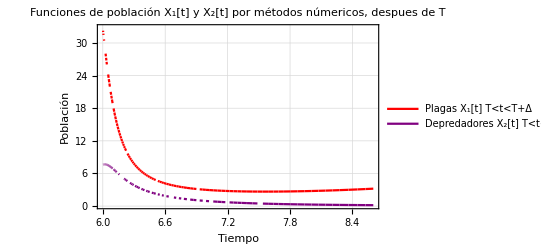

```mathematica
trueplot2=Plot[{pw1fbFromText,pw2fbFromText},{t,6,8.6},PlotTheme->"Scientific",PlotLegends->{"Plagas X_1[t] T<t<T+Δ","Depredadores X_2[t] T<t<T+Δ"},Frame->True,FrameLabel->{{"Población",None},{"Tiempo",None}},PlotLabel->"Funciones de población X_1[t] y X_2[t] por métodos númericos, despues de T",PlotStyle->{Red,Purple},GridLines->Automatic,PlotRange->All]
```

```mathematica
(*pwu1feedback=InterpolationToPiecewise[ux1,t]
pwu2feedback=InterpolationToPiecewise[ux2,t]

Export["dir\\fpwucontrol1feedback.txt",ToString[pwu1feedback,InputForm]]
Export["dir\\fpwucontrol2feedback.txt",ToString[pwu2feedback,InputForm]]

pwu1fbFromText=ToExpression[Import["dir\\fpwucontrol1feedback.txt"] ]
pwu2fbFromText=ToExpression[Import["dir\\fpwucontrol2feedback.txt"]]*)
```

```mathematica
ux1[t_]:=(Part[KnumCaso1,1][[1]])*pw1fbFromText
ux2[t_]:=(1/2)*(Part[KnumCaso1,1][[2]])*pw2fbFromText
```

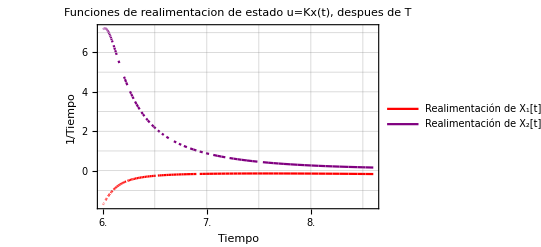

```mathematica
plot1varControl=Plot[{ux1[t],ux2[t]},{t,6,8.6},PlotTheme->"Scientific",PlotLegends->{"Realimentación de X_1[t] T<t<T+Δ","Realimentación de X_2[t] T<t<T+Δ"},Frame->True,FrameLabel->{{"1/Tiempo",None},{"Tiempo",None}},PlotLabel->"Funciones de realimentacion de estado u=Kx(t), despues de T",PlotStyle->{Red,Purple},GridLines->{{6.5,7,7.5,8,8.5},{-1,0,1,2,3,4,5,6,7}},PlotRange->All,FrameTicks->{{{-2,-1,0,1,2,3,4,5,6,7},None},{{6.0,6.5,7.0,7.5,8.0,8.5},None}}]
```

```mathematica
x1T6=pw1fbFromText/.t->8.6
x2T6=pw2fbFromText/.t->8.6
```

3.20453

0.168662

## Después de la aplicación de pesticida

```mathematica
af1x[t]=- γ *ax1[t]* ax2[t] + α ax1[t]
```

α ax1[t]-γ ax1[t] ax2[t]

```mathematica
ag1x[t]=ϵ*γ *ax1[t]* ax2[t]- β*ax2[t]
```

-β ax2[t]+γ ϵ ax1[t] ax2[t]

```mathematica
aftersolNum=NDSolve[{af1x[t]==D[ax1[t],t],ag1x[t]==D[ax2[t],t],ax1[8.6]==x1T6,ax2[8.6]==x2T6,α==1.5318,β==1,γ==0.3,ϵ==0.3},{ax1,ax2},{t,8.6,8.6+6}]
```

{{ax1→InterpolatingFunction[…],ax2→InterpolatingFunction[…]}}

```mathematica
afterx1Sol=ax1/. aftersolNum[[1]]
afterx2Sol=ax2/. aftersolNum[[1]]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

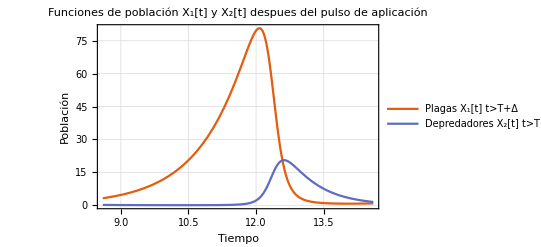

```mathematica
afterplotbasemetdnum=Plot[{afterx1Sol[t],afterx2Sol[t]},{t,8.6,8.6+6},PlotTheme->"Scientific",PlotLegends->{"Plagas X_1[t] t>T+Δ","Depredadores X_2[t] t>T+Δ"},Frame->True,FrameLabel->{{"Población",None},{"Tiempo",None}},PlotLabel->"Funciones de población X_1[t] y X_2[t] despues del pulso de aplicación",GridLines->Automatic,PlotRange->All]
```

```mathematica
pwx1after=InterpolationToPiecewise[afterx1Sol,t]
pwx2after=InterpolationToPiecewise[afterx2Sol,t]

Export["dir\\fpw1after.txt",ToString[pwx1after,InputForm]]
Export["dir\\fpw2after.txt",ToString[pwx2after,InputForm]]

pw1afterFromText=ToExpression[Import["C:\\Users\\Jennis\\Downloads\\fpw1after.txt"]]
pw2afterFromText=ToExpression[Import["C:\\Users\\Jennis\\Downloads\\fpw2after.txt"]]
```

Piecewise[{{3.20512+(3.04298+(4.12083×10^-8-16005.4 (-8.6+t)) (-8.60019+t)) (-8.60019+t), t<8.60019}, {3.2057+(3.04358+(-9.93869×10^-8-16008.5 (-8.60019+t)) (-8.60039+t)) (-8.60039+t), t<8.60039}, {3.21884+(3.05692+(1.54887+1.17683×10^-7 (-8.60039+t)) (-8.60469+t)) (-8.60469+t), t<8.60469}, {3.23204+(3.07032+(1.55541-1.17515×10^-8 (-8.60469+t)) (-8.609+t)) (-8.609+t), t<8.609}, {3.2453+(3.08378+(1.56198-2.11815×10^-8 (-8.609+t)) (-8.61331+t)) (-8.61331+t), t<8.61331}, {3.28635+(3.12545+(1.57936+0.59323 (-8.61331+t)) (-8.62653+t)) (-8.62653+t), t<8.62653}, {3.32797+(3.16767+(1.59938+0.517319 (-8.62653+t)) (-8.63976+t)) (-8.63976+t), t<8.63976}, {3.37015+(3.21043+(1.62022+0.524135 (-8.63976+t)) (-8.65299+t)) (-8.65299+t), t<8.65299}, {3.41289+(3.25375+(1.64134+0.531158 (-8.65299+t)) (-8.66621+t)) (-8.66621+t), t<8.66621}, {3.50012+(3.3421+(1.67722+0.545358 (-8.66621+t)) (-8.69266+t)) (-8.69266+t), t<8.69266}, {3.58972+(3.43277+(1.72129+0.561184 (-8.69266+t)) (-8.71911+t)) (-8.71911+t), t<8.71911}, {3.68174+(3.52582+(1.76652+0.575066 (-8.71911+t)) (-8.74556+t)) (-8.74556+t), t<8.74556}, {3.77626+(3.62132+(1.81298+0.590502 (-8.74556+t)) (-8.77202+t)) (-8.77202+t), t<8.77202}, {3.87334+(3.71933+(1.86068+0.606343 (-8.77202+t)) (-8.79847+t)) (-8.79847+t), t<8.79847}, {4.13422+(3.98238+(1.96227+0.635492 (-8.79847+t)) (-8.86624+t)) (-8.86624+t), t<8.86624}, {4.41353+(4.26356+(2.09754+0.68045 (-8.86624+t)) (-8.93401+t)) (-8.93401+t), t<8.93401}, {4.71254+(4.56413+(2.24223+0.727761 (-8.93401+t)) (-9.00178+t)) (-9.00178+t), t<9.00178}, {5.03262+(4.88545+(2.39702+0.778442 (-9.00178+t)) (-9.06955+t)) (-9.06955+t), t<9.06955}, {5.37522+(5.22896+(2.5626+0.83262 (-9.06955+t)) (-9.13732+t)) (-9.13732+t), t<9.13732}, {5.7419+(5.59621+(2.73968+0.890462 (-9.13732+t)) (-9.20509+t)) (-9.20509+t), t<9.20509}, {6.35875+(6.21324+(3.00128+0.969779 (-9.20509+t)) (-9.30965+t)) (-9.30965+t), t<9.30965}, {7.04357+(6.89732+(3.32735+1.07537 (-9.30965+t)) (-9.41421+t)) (-9.41421+t), t<9.41421}, {7.80374+(7.6557+(3.68878+1.19185 (-9.41421+t)) (-9.51878+t)) (-9.51878+t), t<9.51878}, {8.64743+(8.49643+(4.08928+1.32049 (-9.51878+t)) (-9.62334+t)) (-9.62334+t), t<9.62334}, {9.58372+(9.42838+(4.53291+1.46248 (-9.62334+t)) (-9.7279+t)) (-9.7279+t), t<9.7279}, {10.6227+(10.4613+(5.02407+1.61891 (-9.7279+t)) (-9.83246+t)) (-9.83246+t), t<9.83246}, {11.7753+(11.6061+(5.56754+1.79096 (-9.83246+t)) (-9.93702+t)) (-9.93702+t), t<9.93702}, {13.3167+(13.1347+(6.25103+1.99906 (-9.93702+t)) (-10.0618+t)) (-10.0618+t), t<10.0618}, {15.0609+(14.8615+(7.06106+2.24949 (-10.0618+t)) (-10.1865+t)) (-10.1865+t), t<10.1865}, {16.5739+(16.3568+(7.82834+2.49338 (-10.1865+t)) (-10.2835+t)) (-10.2835+t), t<10.2835}, {18.2389+(17.9992+(8.59826+2.72353 (-10.2835+t)) (-10.3805+t)) (-10.3805+t), t<10.3805}, {19.7344+(19.4714+(9.33452+2.94504 (-10.3805+t)) (-10.4604+t)) (-10.4604+t), t<10.4604}, {21.3521+(21.0602+(10.0733+3.15336 (-10.4604+t)) (-10.5403+t)) (-10.5403+t), t<10.5403}, {23.1015+(22.7737+(10.8626+3.3658 (-10.5403+t)) (-10.6201+t)) (-10.6201+t), t<10.6201}, {24.9931+(24.6201+(11.7028+3.57736 (-10.6201+t)) (-10.7+t)) (-10.7+t), t<10.7}, {26.6013+(26.184+(12.4662+3.75912 (-10.7+t)) (-10.7633+t)) (-10.7633+t), t<10.7633}, {28.3115+(27.8402+(13.1993+3.90714 (-10.7633+t)) (-10.8266+t)) (-10.8266+t), t<10.8266}, {30.1296+(29.5919+(13.9577+4.03212 (-10.8266+t)) (-10.89+t)) (-10.89+t), t<10.89}, {32.0617+(31.4417+(14.7355+4.12087 (-10.89+t)) (-10.9533+t)) (-10.9533+t), t<10.9533}, {33.6743+(32.975+(15.4131+4.15274 (-10.9533+t)) (-11.0034+t)) (-11.0034+t), t<11.0034}, {35.3652+(34.5706+(16.0351+4.12824 (-11.0034+t)) (-11.0535+t)) (-11.0535+t), t<11.0535}, {37.1376+(36.2277+(16.6462+4.03157 (-11.0535+t)) (-11.1035+t)) (-11.1035+t), t<11.1035}, {38.9945+(37.944+(17.2334+3.83708 (-11.1035+t)) (-11.1536+t)) (-11.1536+t), t<11.1536}, {40.5704+(39.3822+(17.7142+3.5447 (-11.1536+t)) (-11.1944+t)) (-11.1944+t), t<11.1944}, {42.2055+(40.8539+(18.1172+3.15838 (-11.1944+t)) (-11.2351+t)) (-11.2351+t), t<11.2351}, {43.9012+(42.3545+(18.4603+2.61444 (-11.2351+t)) (-11.2759+t)) (-11.2759+t), t<11.2759}, {45.6586+(43.8775+(18.7208+1.86718 (-11.2759+t)) (-11.3167+t)) (-11.3167+t), t<11.3167}, {47.4784+(45.4143+(18.8686+0.853417 (-11.3167+t)) (-11.3574+t)) (-11.3574+t), t<11.3574}, {48.9869+(46.6519+(18.8773-0.358661 (-11.3574+t)) (-11.3902+t)) (-11.3902+t), t<11.3902}, {50.536+(47.8829+(18.7535-1.73974 (-11.3902+t)) (-11.423+t)) (-11.423+t), t<11.423}, {52.1251+(49.0973+(18.4703-3.48636 (-11.423+t)) (-11.4557+t)) (-11.4557+t), t<11.4557}, {53.7536+(50.2822+(17.9865-5.68458 (-11.4557+t)) (-11.4885+t)) (-11.4885+t), t<11.4885}, {55.4202+(51.4219+(17.2501-8.45034 (-11.4885+t)) (-11.5213+t)) (-11.5213+t), t<11.5213}, {57.1231+(52.4962+(16.1961-11.9296 (-11.5213+t)) (-11.554+t)) (-11.554+t), t<11.554}, {58.5397+(53.3081+(14.9487-15.8596 (-11.554+t)) (-11.5808+t)) (-11.5808+t), t<11.5808}, {59.977+(54.0427+(13.4486-20.1609 (-11.5808+t)) (-11.6076+t)) (-11.6076+t), t<11.6076}, {61.4327+(54.6797+(11.5559-25.3551 (-11.6076+t)) (-11.6344+t)) (-11.6344+t), t<11.6344}, {62.9039+(55.1944+(9.18999-31.6141 (-11.6344+t)) (-11.6611+t)) (-11.6611+t), t<11.6611}, {64.387+(55.5574+(6.25395-39.1541 (-11.6611+t)) (-11.6879+t)) (-11.6879+t), t<11.6879}, {65.8773+(55.7329+(2.63144-48.2298 (-11.6879+t)) (-11.7147+t)) (-11.7147+t), t<11.7147}, {67.3693+(55.678+(-1.81643-59.1363 (-11.7147+t)) (-11.7415+t)) (-11.7415+t), t<11.7415}, {69.0484+(55.2739+(-7.78693-73.1656 (-11.7415+t)) (-11.7717+t)) (-11.7717+t), t<11.7717}, {70.7087+(54.4197+(-15.4988-91.2517 (-11.7717+t)) (-11.802+t)) (-11.802+t), t<11.802}, {72.335+(53.0059+(-25.0824-113.218 (-11.802+t)) (-11.8322+t)) (-11.8322+t), t<11.8322}, {73.9084+(50.8997+(-36.9276-139.681 (-11.8322+t)) (-11.8625+t)) (-11.8625+t), t<11.8625}, {74.2148+(50.3819+(-43.2743-157.725 (-11.8625+t)) (-11.8685+t)) (-11.8685+t), t<11.8685}, {74.5179+(49.8287+(-46.2174-164.395 (-11.8685+t)) (-11.8746+t)) (-11.8746+t), t<11.8746}, {74.8176+(49.2387+(-49.2804-171.003 (-11.8746+t)) (-11.8806+t)) (-11.8806+t), t<11.8806}, {75.1136+(48.6104+(-52.4684-177.985 (-11.8806+t)) (-11.8867+t)) (-11.8867+t), t<11.8867}, {75.4057+(47.9422+(-55.7848-185.131 (-11.8867+t)) (-11.8927+t)) (-11.8927+t), t<11.8927}, {75.6936+(47.2325+(-59.2337-192.501 (-11.8927+t)) (-11.8988+t)) (-11.8988+t), t<11.8988}, {75.9771+(46.4798+(-62.819-200.089 (-11.8988+t)) (-11.9048+t)) (-11.9048+t), t<11.9048}, {76.5297+(44.8382+(-69.1203-211.891 (-11.9048+t)) (-11.9169+t)) (-11.9169+t), t<11.9169}, {77.0613+(43.0033+(-77.2075-228.336 (-11.9169+t)) (-11.929+t)) (-11.929+t), t<11.929}, {77.5695+(40.9603+(-85.9109-245.578 (-11.929+t)) (-11.9411+t)) (-11.9411+t), t<11.9411}, {78.0516+(38.6937+(-95.258-263.549 (-11.9411+t)) (-11.9532+t)) (-11.9532+t), t<11.9532}, {78.5049+(36.1876+(-105.273-282.149 (-11.9532+t)) (-11.9653+t)) (-11.9653+t), t<11.9653}, {78.9263+(33.4252+(-115.975-301.242 (-11.9653+t)) (-11.9774+t)) (-11.9774+t), t<11.9774}, {79.3126+(30.3897+(-127.379-320.646 (-11.9774+t)) (-11.9895+t)) (-11.9895+t), t<11.9895}, {79.7904+(25.6219+(-142.919-344.09 (-11.9895+t)) (-12.0065+t)) (-12.0065+t), t<12.0065}, {80.1818+(20.2319+(-161.415-370.903 (-12.0065+t)) (-12.0236+t)) (-12.0236+t), t<12.0236}, {80.4757+(14.1743+(-181.23-396.104 (-12.0236+t)) (-12.0406+t)) (-12.0406+t), t<12.0406}, {80.6605+(7.40771+(-202.235-418.318 (-12.0406+t)) (-12.0576+t)) (-12.0576+t), t<12.0576}, {80.7238+(-0.102609+(-224.222-435.825 (-12.0576+t)) (-12.0746+t)) (-12.0746+t), t<12.0746}, {80.6526+(-8.38155+(-246.881-446.607 (-12.0746+t)) (-12.0917+t)) (-12.0917+t), t<12.0917}, {80.4339+(-17.4403+(-269.791-448.322 (-12.0917+t)) (-12.1087+t)) (-12.1087+t), t<12.1087}, {80.0542+(-27.272+(-292.401-438.384 (-12.1087+t)) (-12.1257+t)) (-12.1257+t), t<12.1257}, {79.3967+(-39.581+(-316.192-411.307 (-12.1257+t)) (-12.1455+t)) (-12.1455+t), t<12.1455}, {78.4874+(-52.7936+(-338.601-360.028 (-12.1455+t)) (-12.1652+t)) (-12.1652+t), t<12.1652}, {77.3099+(-66.7598+(-356.943-282.221 (-12.1652+t)) (-12.1849+t)) (-12.1849+t), t<12.1849}, {75.8512+(-81.265+(-369.559-175.772 (-12.1849+t)) (-12.2046+t)) (-12.2046+t), t<12.2046}, {74.1035+(-96.0271+(-374.746-40.7017 (-12.2046+t)) (-12.2243+t)) (-12.2243+t), t<12.2243}, {72.065+(-110.701+(-370.911+120.07 (-12.2243+t)) (-12.244+t)) (-12.244+t), t<12.244}, {69.7413+(-124.886+(-356.77+300.172 (-12.244+t)) (-12.2638+t)) (-12.2638+t), t<12.2638}, {67.1462+(-138.152+(-331.556+489.699 (-12.2638+t)) (-12.2835+t)) (-12.2835+t), t<12.2835}, {64.3022+(-150.056+(-295.207+675.734 (-12.2835+t)) (-12.3032+t)) (-12.3032+t), t<12.3032}, {61.7658+(-158.63+(-254.254+831.059 (-12.3032+t)) (-12.3196+t)) (-12.3196+t), t<12.3196}, {59.1001+(-165.762+(-209.345+949.088 (-12.3196+t)) (-12.336+t)) (-12.336+t), t<12.336}, {56.3304+(-171.282+(-159.559+1037.85 (-12.336+t)) (-12.3525+t)) (-12.3525+t), t<12.3525}, {53.484+(-175.076+(-106.543+1091.38 (-12.3525+t)) (-12.3689+t)) (-12.3689+t), t<12.3689}, {50.59+(-177.087+(-52.141+1106.64 (-12.3689+t)) (-12.3853+t)) (-12.3853+t), t<12.3853}, {47.6776+(-177.322+(1.73772+1083.26 (-12.3853+t)) (-12.4017+t)) (-12.4017+t), t<12.4017}, {44.7754+(-175.849+(53.2641+1023.79 (-12.4017+t)) (-12.4181+t)) (-12.4181+t), t<12.4181}, {41.9107+(-172.789+(100.818+933.249 (-12.4181+t)) (-12.4346+t)) (-12.4346+t), t<12.4346}, {39.1082+(-168.31+(143.09+818.529 (-12.4346+t)) (-12.451+t)) (-12.451+t), t<12.451}, {36.3895+(-162.612+(179.148+687.56 (-12.451+t)) (-12.4674+t)) (-12.4674+t), t<12.4674}, {33.7729+(-155.913+(208.461+548.468 (-12.4674+t)) (-12.4838+t)) (-12.4838+t), t<12.4838}, {31.2729+(-148.44+(230.88+408.832 (-12.4838+t)) (-12.5003+t)) (-12.5003+t), t<12.5003}, {28.9006+(-140.415+(246.597+275.113 (-12.5003+t)) (-12.5167+t)) (-12.5167+t), t<12.5167}, {26.6631+(-132.046+(256.073+152.317 (-12.5167+t)) (-12.5331+t)) (-12.5331+t), t<12.5331}, {24.5645+(-123.52+(259.963+43.8716 (-12.5331+t)) (-12.5495+t)) (-12.5495+t), t<12.5495}, {22.6062+(-114.999+(259.042-48.3057 (-12.5495+t)) (-12.5659+t)) (-12.5659+t), t<12.5659}, {20.7868+(-106.619+(254.135-123.613 (-12.5659+t)) (-12.5824+t)) (-12.5824+t), t<12.5824}, {19.103+(-98.4881+(246.06-182.494 (-12.5824+t)) (-12.5988+t)) (-12.5988+t), t<12.5988}, {17.5502+(-90.6894+(235.59-226.149 (-12.5988+t)) (-12.6152+t)) (-12.6152+t), t<12.6152}, {16.1223+(-83.2824+(223.421-256.254 (-12.6152+t)) (-12.6316+t)) (-12.6316+t), t<12.6316}, {14.3707+(-73.9159+(206.871-276.847 (-12.6316+t)) (-12.6539+t)) (-12.6539+t), t<12.6539}, {13.1459+(-67.2046+(190.742-284.556 (-12.6539+t)) (-12.6713+t)) (-12.6713+t), t<12.6713}, {12.264+(-62.2997+(178.046-284.097 (-12.6713+t)) (-12.6849+t)) (-12.6849+t), t<12.6849}, {11.602+(-58.5839+(168.068-278.632 (-12.6849+t)) (-12.6959+t)) (-12.6959+t), t<12.6959}, {11.0676+(-55.5651+(159.878-274.127 (-12.6959+t)) (-12.7053+t)) (-12.7053+t), t<12.7053}, {10.5607+(-52.6887+(152.308-267.094 (-12.7053+t)) (-12.7146+t)) (-12.7146+t), t<12.7146}, {10.0802+(-49.9511+(144.928-260.2 (-12.7146+t)) (-12.724+t)) (-12.724+t), t<12.724}, {9.62467+(-47.3484+(137.767-252.176 (-12.724+t)) (-12.7333+t)) (-12.7333+t), t<12.7333}, {9.19289+(-44.8762+(130.84-243.681 (-12.7333+t)) (-12.7427+t)) (-12.7427+t), t<12.7427}, {8.78368+(-42.5299+(124.16-234.784 (-12.7427+t)) (-12.7521+t)) (-12.7521+t), t<12.7521}, {8.39587+(-40.3048+(117.734-225.625 (-12.7521+t)) (-12.7614+t)) (-12.7614+t), t<12.7614}, {7.75506+(-36.6286+(108.482-212.685 (-12.7614+t)) (-12.7781+t)) (-12.7781+t), t<12.7781}, {7.17267+(-33.2931+(98.3997-196.066 (-12.7781+t)) (-12.7948+t)) (-12.7948+t), t<12.7948}, {6.64323+(-30.271+(89.1368-179.804 (-12.7948+t)) (-12.8115+t)) (-12.8115+t), t<12.8115}, {6.16174+(-27.5357+(80.666-164.201 (-12.8115+t)) (-12.8281+t)) (-12.8281+t), t<12.8281}, {5.72365+(-25.0619+(72.9495-149.409 (-12.8281+t)) (-12.8448+t)) (-12.8448+t), t<12.8448}, {5.32478+(-22.8255+(65.9421-135.552 (-12.8448+t)) (-12.8615+t)) (-12.8615+t), t<12.8615}, {4.96138+(-20.8043+(59.5946-122.689 (-12.8615+t)) (-12.8781+t)) (-12.8781+t), t<12.8781}, {4.63002+(-18.9777+(53.8569-110.836 (-12.8781+t)) (-12.8948+t)) (-12.8948+t), t<12.8948}, {4.25809+(-16.9497+(47.8955-98.7365 (-12.8948+t)) (-12.9155+t)) (-12.9155+t), t<12.9155}, {3.92567+(-15.1604+(42.2596-86.718 (-12.9155+t)) (-12.9363+t)) (-12.9363+t), t<12.9363}, {3.62812+(-13.5807+(37.3139-76.0705 (-12.9363+t)) (-12.957+t)) (-12.957+t), t<12.957}, {3.36137+(-12.1849+(32.9776-66.6844 (-12.957+t)) (-12.9777+t)) (-12.9777+t), t<12.9777}, {3.12185+(-10.9502+(29.1771-58.4382 (-12.9777+t)) (-12.9985+t)) (-12.9985+t), t<12.9985}, {2.90642+(-9.85661+(25.8465-51.2148 (-12.9985+t)) (-13.0192+t)) (-13.0192+t), t<13.0192}, {2.71236+(-8.88681+(22.927-44.8984 (-13.0192+t)) (-13.0399+t)) (-13.0399+t), t<13.0399}, {2.53724+(-8.02552+(20.3667-39.3822 (-13.0399+t)) (-13.0606+t)) (-13.0606+t), t<13.0606}, {2.37898+(-7.25945+(18.12-34.5689 (-13.0606+t)) (-13.0814+t)) (-13.0814+t), t<13.0814}, {2.1899+(-6.36117+(15.7369-29.7206 (-13.0814+t)) (-13.1092+t)) (-13.1092+t), t<13.1092}, {2.02399+(-5.58965+(13.5232-25.0283 (-13.1092+t)) (-13.137+t)) (-13.137+t), t<13.137}, {1.87801+(-4.92499+(11.6563-21.1214 (-13.137+t)) (-13.1648+t)) (-13.1648+t), t<13.1648}, {1.74923+(-4.3506+(10.0786-17.8652 (-13.1648+t)) (-13.1926+t)) (-13.1926+t), t<13.1926}, {1.63532+(-3.85266+(8.74195-15.1478 (-13.1926+t)) (-13.2204+t)) (-13.2204+t), t<13.2204}, {1.53434+(-3.41961+(7.60676-12.8761 (-13.2204+t)) (-13.2482+t)) (-13.2482+t), t<13.2482}, {1.44461+(-3.04179+(6.64019-10.9734 (-13.2482+t)) (-13.276+t)) (-13.276+t), t<13.276}, {1.36472+(-2.71111+(5.81504-9.37646 (-13.276+t)) (-13.3039+t)) (-13.3039+t), t<13.3039}, {1.29345+(-2.42075+(5.10876-8.03297 (-13.3039+t)) (-13.3317+t)) (-13.3317+t), t<13.3317}, {1.20845+(-2.08017+(4.37188-6.71858 (-13.3317+t)) (-13.3695+t)) (-13.3695+t), t<13.3695}, {1.13532+(-1.79191+(3.70415-5.48898 (-13.3695+t)) (-13.4074+t)) (-13.4074+t), t<13.4074}, {1.07227+(-1.54648+(3.15694-4.50555 (-13.4074+t)) (-13.4452+t)) (-13.4452+t), t<13.4452}, {1.01781+(-1.33628+(2.70644-3.71526 (-13.4452+t)) (-13.4831+t)) (-13.4831+t), t<13.4831}, {0.970744+(-1.1552+(2.3339-3.07705 (-13.4831+t)) (-13.5209+t)) (-13.5209+t), t<13.5209}, {0.930059+(-0.998277+(2.0245-2.55917 (-13.5209+t)) (-13.5588+t)) (-13.5588+t), t<13.5588}, {0.894921+(-0.861492+(1.76651-2.13692 (-13.5588+t)) (-13.5966+t)) (-13.5966+t), t<13.5966}, {0.864633+(-0.74155+(1.55056-1.79097 (-13.5966+t)) (-13.6345+t)) (-13.6345+t), t<13.6345}, {0.838608+(-0.635748+(1.36916-1.5062 (-13.6345+t)) (-13.6723+t)) (-13.6723+t), t<13.6723}, {0.813084+(-0.52766+(1.20153-1.25377 (-13.6723+t)) (-13.7163+t)) (-13.7163+t), t<13.7163}, {0.792012+(-0.432801+(1.05597-1.03292 (-13.7163+t)) (-13.7603+t)) (-13.7603+t), t<13.7603}, {0.774863+(-0.348855+(0.935801-0.853624 (-13.7603+t)) (-13.8042+t)) (-13.8042+t), t<13.8042}, {0.761201+(-0.273941+(0.836323-0.707234 (-13.8042+t)) (-13.8482+t)) (-13.8482+t), t<13.8482}, {0.750663+(-0.206516+(0.753811-0.586945 (-13.8482+t)) (-13.8922+t)) (-13.8922+t), t<13.8922}, {0.742949+(-0.145309+(0.685291-0.487521 (-13.8922+t)) (-13.9361+t)) (-13.9361+t), t<13.9361}, {0.737809+(-0.0892654+(0.628383-0.404834 (-13.9361+t)) (-13.9801+t)) (-13.9801+t), t<13.9801}, {0.735036+(-0.0375081+(0.58117-0.335649 (-13.9801+t)) (-14.0241+t)) (-14.0241+t), t<14.0241}, {0.734459+(0.0107011+(0.542103-0.277399 (-14.0241+t)) (-14.068+t)) (-14.068+t), t<14.068}, {0.736871+(0.0706453+(0.50367-0.220614 (-14.068+t)) (-14.1268+t)) (-14.1268+t), t<14.1268}, {0.742681+(0.126589+(0.471192-0.167151 (-14.1268+t)) (-14.1856+t)) (-14.1856+t), t<14.1856}, {0.751687+(0.179535+(0.446973-0.123351 (-14.1856+t)) (-14.2443+t)) (-14.2443+t), t<14.2443}, {0.763735+(0.230312+(0.429576-0.087013 (-14.2443+t)) (-14.3031+t)) (-14.3031+t), t<14.3031}, {0.77872+(0.27961+(0.417888-0.0564559 (-14.3031+t)) (-14.3618+t)) (-14.3618+t), t<14.3618}, {0.796573+(0.328014+(0.411045-0.0303982 (-14.3618+t)) (-14.4206+t)) (-14.4206+t), t<14.4206}, {0.817255+(0.376026+(0.408373-0.00784516 (-14.4206+t)) (-14.4793+t)) (-14.4793+t), t<14.4793}, {0.840758+(0.424084+(0.409347+0.0119778 (-14.4793+t)) (-14.5381+t)) (-14.5381+t), t<14.5381}, {0.854286+(0.449569+(0.411842+0.0256766 (-14.5381+t)) (-14.569+t)) (-14.569+t), t<14.569}, {0.868606+(0.475227+(0.414779+0.0345393 (-14.569+t)) (-14.6+t)) (-14.6+t), True}}]

Piecewise[{{0.168621+(-0.209653+(-3.09485×10^-9-1589.16 (-8.6+t)) (-8.60019+t)) (-8.60019+t), t<8.60019}, {0.168581+(-0.209594+(7.02525×10^-9-1588.71 (-8.60019+t)) (-8.60039+t)) (-8.60039+t), t<8.60039}, {0.167681+(-0.208277+(0.152899-7.91016×10^-9 (-8.60039+t)) (-8.60469+t)) (-8.60469+t), t<8.60469}, {0.166786+(-0.206968+(0.151938+1.06954×10^-9 (-8.60469+t)) (-8.609+t)) (-8.609+t), t<8.609}, {0.165898+(-0.205667+(0.150983+9.48381×10^-10 (-8.609+t)) (-8.61331+t)) (-8.61331+t), t<8.61331}, {0.163204+(-0.201724+(0.148494-0.0854432 (-8.61331+t)) (-8.62653+t)) (-8.62653+t), t<8.62653}, {0.160561+(-0.197857+(0.145728-0.0719586 (-8.62653+t)) (-8.63976+t)) (-8.63976+t), t<8.63976}, {0.15797+(-0.194064+(0.142938-0.0705417 (-8.63976+t)) (-8.65299+t)) (-8.65299+t), t<8.65299}, {0.155428+(-0.190343+(0.140205-0.0691403 (-8.65299+t)) (-8.66621+t)) (-8.66621+t), t<8.66621}, {0.150489+(-0.183114+(0.135778-0.0663834 (-8.66621+t)) (-8.69266+t)) (-8.69266+t), t<8.69266}, {0.145738+(-0.176158+(0.13065-0.0635239 (-8.69266+t)) (-8.71911+t)) (-8.71911+t), t<8.71911}, {0.141168+(-0.169464+(0.125719-0.0612399 (-8.71911+t)) (-8.74556+t)) (-8.74556+t), t<8.74556}, {0.136771+(-0.163022+(0.120985-0.0588135 (-8.74556+t)) (-8.77202+t)) (-8.77202+t), t<8.77202}, {0.132541+(-0.156823+(0.11644-0.0564817 (-8.77202+t)) (-8.79847+t)) (-8.79847+t), t<8.79847}, {0.122425+(-0.141978+(0.107741-0.0525289 (-8.79847+t)) (-8.86624+t)) (-8.86624+t), t<8.86624}, {0.113266+(-0.12851+(0.0977586-0.0474456 (-8.86624+t)) (-8.93401+t)) (-8.93401+t), t<8.93401}, {0.104978+(-0.116281+(0.0887758-0.0426661 (-8.93401+t)) (-9.00178+t)) (-9.00178+t), t<9.00178}, {0.0974803+(-0.105168+(0.0806923-0.0383701 (-9.00178+t)) (-9.06955+t)) (-9.06955+t), t<9.06955}, {0.090701+(-0.0950574+(0.0734266-0.0344734 (-9.06955+t)) (-9.13732+t)) (-9.13732+t), t<9.13732}, {0.0845758+(-0.085847+(0.0669053-0.0309242 (-9.13732+t)) (-9.20509+t)) (-9.20509+t), t<9.20509}, {0.0762767+(-0.0731884+(0.0591263-0.0268748 (-9.20509+t)) (-9.30965+t)) (-9.30965+t), t<9.30965}, {0.0692141+(-0.0621459+(0.0516291-0.0224684 (-9.30965+t)) (-9.41421+t)) (-9.41421+t), t<9.41421}, {0.0632336+(-0.0524499+(0.045391-0.018619 (-9.41421+t)) (-9.51878+t)) (-9.51878+t), t<9.51878}, {0.058207+(-0.0438608+(0.0402795-0.0151591 (-9.51878+t)) (-9.62334+t)) (-9.62334+t), t<9.62334}, {0.0540302+(-0.0361606+(0.0361956-0.0119702 (-9.62334+t)) (-9.7279+t)) (-9.7279+t), t<9.7279}, {0.0506211+(-0.0291457+(0.0330768-0.00893866 (-9.7279+t)) (-9.83246+t)) (-9.83246+t), t<9.83246}, {0.0479182+(-0.0226183+(0.030903-0.00592381 (-9.83246+t)) (-9.93702+t)) (-9.93702+t), t<9.93702}, {0.0455623+(-0.0151857+(0.0296358-0.00243651 (-9.93702+t)) (-10.0618+t)) (-10.0618+t), t<10.0618}, {0.0441278+(-0.00778046+(0.0297984+0.00192713 (-10.0618+t)) (-10.1865+t)) (-10.1865+t), t<10.1865}, {0.0436624+(-0.00175302+(0.0313974+0.00677164 (-10.1865+t)) (-10.2835+t)) (-10.2835+t), t<10.2835}, {0.0438049+(0.00480558+(0.0343988+0.0122049 (-10.2835+t)) (-10.3805+t)) (-10.3805+t), t<10.3805}, {0.0444253+(0.010853+(0.0386122+0.0187884 (-10.3805+t)) (-10.4604+t)) (-10.4604+t), t<10.4604}, {0.0455612+(0.0177636+(0.0443283+0.0265828 (-10.4604+t)) (-10.5403+t)) (-10.5403+t), t<10.5403}, {0.0472948+(0.0258861+(0.0523346+0.0370841 (-10.5403+t)) (-10.6201+t)) (-10.6201+t), t<10.6201}, {0.0497405+(0.0356926+(0.0634504+0.0514242 (-10.6201+t)) (-10.7+t)) (-10.7+t), t<10.7}, {0.0522897+(0.0450903+(0.076384+0.0690793 (-10.7+t)) (-10.7633+t)) (-10.7633+t), t<10.7633}, {0.0554918+(0.0563926+(0.0920797+0.0898988 (-10.7633+t)) (-10.8266+t)) (-10.8266+t), t<10.8266}, {0.0594849+(0.0701838+(0.112615+0.117852 (-10.8266+t)) (-10.89+t)) (-10.89+t), t<10.89}, {0.0644502+(0.0872494+(0.139662+0.155568 (-10.89+t)) (-10.9533+t)) (-10.9533+t), t<10.9533}, {0.06922+(0.103753+(0.169814+0.201012 (-10.9533+t)) (-11.0034+t)) (-11.0034+t), t<11.0034}, {0.0748981+(0.123662+(0.205134+0.253378 (-11.0034+t)) (-11.0535+t)) (-11.0535+t), t<11.0535}, {0.0816769+(0.147883+(0.249899+0.321812 (-11.0535+t)) (-11.1035+t)) (-11.1035+t), t<11.1035}, {0.0898006+(0.177599+(0.307008+0.411426 (-11.1035+t)) (-11.1536+t)) (-11.1536+t), t<11.1536}, {0.0976195+(0.206908+(0.37006+0.517412 (-11.1536+t)) (-11.1944+t)) (-11.1944+t), t<11.1944}, {0.106746+(0.24196+(0.442997+0.638591 (-11.1944+t)) (-11.2351+t)) (-11.2351+t), t<11.2351}, {0.117441+(0.284126+(0.533389+0.792733 (-11.2351+t)) (-11.2759+t)) (-11.2759+t), t<11.2759}, {0.130028+(0.335145+(0.645992+0.989156 (-11.2759+t)) (-11.3167+t)) (-11.3167+t), t<11.3167}, {0.144913+(0.397243+(0.787025+1.24096 (-11.3167+t)) (-11.3574+t)) (-11.3574+t), t<11.3574}, {0.158885+(0.457116+(0.938575+1.52988 (-11.3574+t)) (-11.3902+t)) (-11.3902+t), t<11.3902}, {0.174991+(0.52785+(1.10955+1.84988 (-11.3902+t)) (-11.423+t)) (-11.423+t), t<11.423}, {0.193625+(0.611749+(1.31688+2.24597 (-11.423+t)) (-11.4557+t)) (-11.4557+t), t<11.4557}, {0.215261+(0.711658+(1.56919+2.73614 (-11.4557+t)) (-11.4885+t)) (-11.4885+t), t<11.4885}, {0.240481+(0.831107+(1.87729+3.34488 (-11.4885+t)) (-11.5213+t)) (-11.5213+t), t<11.5213}, {0.269994+(0.974486+(2.25483+4.10286 (-11.5213+t)) (-11.554+t)) (-11.554+t), t<11.554}, {0.297895+(1.11316+(2.65607+4.95272 (-11.554+t)) (-11.5808+t)) (-11.5808+t), t<11.5808}, {0.32981+(1.27509+(3.10257+5.87792 (-11.5808+t)) (-11.6076+t)) (-11.6076+t), t<11.6076}, {0.36642+(1.46463+(3.63328+6.99071 (-11.6076+t)) (-11.6344+t)) (-11.6344+t), t<11.6344}, {0.408532+(1.68705+(4.26512+8.32708 (-11.6344+t)) (-11.6611+t)) (-11.6611+t), t<11.6611}, {0.457108+(1.94866+(5.01846+9.93243 (-11.6611+t)) (-11.6879+t)) (-11.6879+t), t<11.6879}, {0.513297+(2.25705+(5.91768+11.8596 (-11.6879+t)) (-11.7147+t)) (-11.7147+t), t<11.7147}, {0.578468+(2.62129+(6.99184+14.1694 (-11.7147+t)) (-11.7415+t)) (-11.7415+t), t<11.7415}, {0.664969+(3.11375+(8.39938+17.1311 (-11.7415+t)) (-11.7717+t)) (-11.7717+t), t<11.7717}, {0.76789+(3.71043+(10.1795+20.9335 (-11.7717+t)) (-11.802+t)) (-11.802+t), t<11.802}, {0.89072+(4.43432+(12.3517+25.5258 (-11.802+t)) (-11.8322+t)) (-11.8322+t), t<11.8322}, {1.03771+(5.31304+(14.9942+31.0151 (-11.8322+t)) (-11.8625+t)) (-11.8625+t), t<11.8625}, {1.07045+(5.51016+(16.3965+34.7211 (-11.8625+t)) (-11.8685+t)) (-11.8685+t), t<11.8685}, {1.1044+(5.71505+(17.0433+36.0983 (-11.8685+t)) (-11.8746+t)) (-11.8746+t), t<11.8746}, {1.13961+(5.92802+(17.7145+37.439 (-11.8746+t)) (-11.8806+t)) (-11.8806+t), t<11.8806}, {1.17614+(6.14936+(18.4112+38.8617 (-11.8806+t)) (-11.8867+t)) (-11.8867+t), t<11.8867}, {1.21403+(6.37939+(19.134+40.3096 (-11.8867+t)) (-11.8927+t)) (-11.8927+t), t<11.8927}, {1.25335+(6.61844+(19.8835+41.7977 (-11.8927+t)) (-11.8988+t)) (-11.8988+t), t<11.8988}, {1.29413+(6.86684+(20.6606+43.3235 (-11.8988+t)) (-11.9048+t)) (-11.9048+t), t<11.9048}, {1.38036+(7.39303+(22.0208+45.6825 (-11.9048+t)) (-11.9169+t)) (-11.9169+t), t<11.9169}, {1.4732+(7.96077+(23.7575+48.9408 (-11.9169+t)) (-11.929+t)) (-11.929+t), t<11.929}, {1.57318+(8.57297+(25.6154+52.3154 (-11.929+t)) (-11.9411+t)) (-11.9411+t), t<11.9411}, {1.68085+(9.23264+(27.598+55.7813 (-11.9411+t)) (-11.9532+t)) (-11.9532+t), t<11.9532}, {1.7968+(9.94285+(29.7078+59.3046 (-11.9532+t)) (-11.9653+t)) (-11.9653+t), t<11.9653}, {1.92167+(10.7067+(31.9461+62.8417 (-11.9653+t)) (-11.9774+t)) (-11.9774+t), t<11.9774}, {2.05612+(11.5273+(34.3118+66.3371 (-11.9774+t)) (-11.9895+t)) (-11.9895+t), t<11.9895}, {2.26295+(12.7842+(37.5023+70.389 (-11.9895+t)) (-12.0065+t)) (-12.0065+t), t<12.0065}, {2.49225+(14.1673+(41.2474+74.7129 (-12.0065+t)) (-12.0236+t)) (-12.0236+t), t<12.0236}, {2.74623+(15.6837+(45.1902+78.3154 (-12.0236+t)) (-12.0406+t)) (-12.0406+t), t<12.0406}, {3.02721+(17.3388+(49.2809+80.8186 (-12.0406+t)) (-12.0576+t)) (-12.0576+t), t<12.0576}, {3.33757+(19.1354+(53.4481+81.7622 (-12.0576+t)) (-12.0746+t)) (-12.0746+t), t<12.0746}, {3.67974+(21.0736+(57.5942+80.6161 (-12.0746+t)) (-12.0917+t)) (-12.0917+t), t<12.0917}, {4.05609+(23.1491+(61.5924+76.7808 (-12.0917+t)) (-12.1087+t)) (-12.1087+t), t<12.1087}, {4.4689+(25.3524+(65.2834+69.6116 (-12.1087+t)) (-12.1257+t)) (-12.1257+t), t<12.1257}, {4.99507+(28.0419+(68.7656+57.3427 (-12.1257+t)) (-12.1455+t)) (-12.1455+t), t<12.1455}, {5.57546+(30.8438+(71.4299+38.2062 (-12.1455+t)) (-12.1652+t)) (-12.1652+t), t<12.1652}, {6.21179+(33.7057+(72.6925+12.1719 (-12.1652+t)) (-12.1849+t)) (-12.1849+t), t<12.1849}, {6.90458+(36.5584+(72.1332-21.0158 (-12.1849+t)) (-12.2046+t)) (-12.2046+t), t<12.2046}, {7.65284+(39.3166+(69.3412-60.9687 (-12.2046+t)) (-12.2243+t)) (-12.2243+t), t<12.2243}, {8.45374+(41.8802+(63.9607-106.46 (-12.2243+t)) (-12.244+t)) (-12.244+t), t<12.244}, {9.30237+(44.1389+(55.7459-155.307 (-12.244+t)) (-12.2638+t)) (-12.2638+t), t<12.2638}, {10.1916+(45.9779+(44.6172-204.394 (-12.2638+t)) (-12.2835+t)) (-12.2835+t), t<12.2835}, {11.112+(47.286+(30.7095-249.878 (-12.2835+t)) (-12.3032+t)) (-12.3032+t), t<12.3032}, {11.8942+(47.8994+(16.3344-284.988 (-12.3032+t)) (-12.3196+t)) (-12.3196+t), t<12.3196}, {12.6826+(48.0315+(1.49109-308.508 (-12.3196+t)) (-12.336+t)) (-12.336+t), t<12.336}, {13.4689+(47.6522+(-14.1967-322.278 (-12.336+t)) (-12.3525+t)) (-12.3525+t), t<12.3525}, {14.2448+(46.7479+(-30.1996-324.911 (-12.3525+t)) (-12.3689+t)) (-12.3689+t), t<12.3689}, {15.0014+(45.3239+(-45.9523-315.975 (-12.3689+t)) (-12.3853+t)) (-12.3853+t), t<12.3853}, {15.7306+(43.4037+(-60.8934-295.834 (-12.3853+t)) (-12.4017+t)) (-12.4017+t), t<12.4017}, {16.4245+(41.0282+(-74.5082-265.705 (-12.4017+t)) (-12.4181+t)) (-12.4181+t), t<12.4181}, {17.076+(38.253+(-86.3653-227.493 (-12.4181+t)) (-12.4346+t)) (-12.4346+t), t<12.4346}, {17.679+(35.1448+(-96.1436-183.574 (-12.4346+t)) (-12.451+t)) (-12.451+t), t<12.451}, {18.2288+(31.7775+(-103.647-136.538 (-12.451+t)) (-12.4674+t)) (-12.4674+t), t<12.4674}, {18.7217+(28.2279+(-108.806-88.93 (-12.4674+t)) (-12.4838+t)) (-12.4838+t), t<12.4838}, {19.1554+(24.5718+(-111.669-43.0282 (-12.4838+t)) (-12.5003+t)) (-12.5003+t), t<12.5003}, {19.5286+(20.8809+(-112.383-0.690605 (-12.5003+t)) (-12.5167+t)) (-12.5167+t), t<12.5167}, {19.8413+(17.2198+(-111.17+36.7311 (-12.5167+t)) (-12.5331+t)) (-12.5331+t), t<12.5331}, {20.0946+(13.6444+(-108.3+68.4066 (-12.5331+t)) (-12.5495+t)) (-12.5495+t), t<12.5495}, {20.2902+(10.201+(-104.07+93.9866 (-12.5495+t)) (-12.5659+t)) (-12.5659+t), t<12.5659}, {20.4306+(6.92613+(-98.7787+113.526 (-12.5659+t)) (-12.5824+t)) (-12.5824+t), t<12.5824}, {20.5187+(3.84672+(-92.7133+127.388 (-12.5824+t)) (-12.5988+t)) (-12.5988+t), t<12.5988}, {20.5581+(0.981023+(-86.1347+136.147 (-12.5988+t)) (-12.6152+t)) (-12.6152+t), t<12.6152}, {20.5522+(-1.66045+(-79.2718+140.498 (-12.6152+t)) (-12.6316+t)) (-12.6316+t), t<12.6316}, {20.4784+(-4.8829+(-70.6626+140.936 (-12.6316+t)) (-12.6539+t)) (-12.6539+t), t<12.6539}, {20.374+(-7.10372+(-62.7429+137.325 (-12.6539+t)) (-12.6713+t)) (-12.6713+t), t<12.6713}, {20.2663+(-8.67483+(-56.7475+132.676 (-12.6713+t)) (-12.6849+t)) (-12.6849+t), t<12.6849}, {20.1649+(-9.83277+(-52.1502+127.512 (-12.6849+t)) (-12.6959+t)) (-12.6959+t), t<12.6959}, {20.0684+(-10.751+(-48.4434+123.399 (-12.6959+t)) (-12.7053+t)) (-12.7053+t), t<12.7053}, {19.9637+(-11.6055+(-45.0634+118.766 (-12.7053+t)) (-12.7146+t)) (-12.7146+t), t<12.7146}, {19.8512+(-12.3987+(-41.8088+114.296 (-12.7146+t)) (-12.724+t)) (-12.724+t), t<12.724}, {19.7316+(-13.133+(-38.6862+109.561 (-12.724+t)) (-12.7333+t)) (-12.7333+t), t<12.7333}, {19.6054+(-13.8108+(-35.6973+104.778 (-12.7333+t)) (-12.7427+t)) (-12.7427+t), t<12.7427}, {19.4731+(-14.4348+(-32.8435+99.9689 (-12.7427+t)) (-12.7521+t)) (-12.7521+t), t<12.7521}, {19.3352+(-15.0074+(-30.1245+95.1741 (-12.7521+t)) (-12.7614+t)) (-12.7614+t), t<12.7614}, {19.0773+(-15.9075+(-26.2552+88.6097 (-12.7614+t)) (-12.7781+t)) (-12.7781+t), t<12.7781}, {18.8056+(-16.6666+(-22.0969+80.4426 (-12.7781+t)) (-12.7948+t)) (-12.7948+t), t<12.7948}, {18.5223+(-17.2981+(-18.334+72.6693 (-12.7948+t)) (-12.8115+t)) (-12.8115+t), t<12.8115}, {18.2294+(-17.8146+(-14.9443+65.3677 (-12.8115+t)) (-12.8281+t)) (-12.8281+t), t<12.8281}, {17.9288+(-18.2277+(-11.9034+58.565 (-12.8281+t)) (-12.8448+t)) (-12.8448+t), t<12.8448}, {17.6222+(-18.5485+(-9.18546+52.2815 (-12.8448+t)) (-12.8615+t)) (-12.8615+t), t<12.8615}, {17.3108+(-18.787+(-6.76451+46.5168 (-12.8615+t)) (-12.8781+t)) (-12.8781+t), t<12.8781}, {16.9961+(-18.9524+(-4.61496+41.2577 (-12.8781+t)) (-12.8948+t)) (-12.8948+t), t<12.8948}, {16.6019+(-19.0685+(-2.42855+35.9386 (-12.8948+t)) (-12.9155+t)) (-12.9155+t), t<12.9155}, {16.2062+(-19.0988+(-0.413535+30.7013 (-12.9155+t)) (-12.9363+t)) (-12.9363+t), t<12.9363}, {15.8106+(-19.0561+(1.3024+26.1013 (-12.9363+t)) (-12.957+t)) (-12.957+t), t<12.957}, {15.4166+(-18.9513+(2.75647+22.0788 (-12.957+t)) (-12.9777+t)) (-12.9777+t), t<12.9777}, {15.0253+(-18.7942+(3.98207+18.5723 (-12.9777+t)) (-12.9985+t)) (-12.9985+t), t<12.9985}, {14.6377+(-18.5932+(5.00888+15.5246 (-12.9985+t)) (-13.0192+t)) (-13.0192+t), t<13.0192}, {14.2547+(-18.3556+(5.86315+12.8813 (-13.0192+t)) (-13.0399+t)) (-13.0399+t), t<13.0399}, {13.877+(-18.0879+(6.56795+10.5929 (-13.0399+t)) (-13.0606+t)) (-13.0606+t), t<13.0606}, {13.505+(-17.7954+(7.14349+8.61521 (-13.0606+t)) (-13.0814+t)) (-13.0814+t), t<13.0814}, {13.0159+(-17.3725+(7.69704+6.64611 (-13.0814+t)) (-13.1092+t)) (-13.1092+t), t<13.1092}, {12.539+(-16.9231+(8.145+4.76881 (-13.1092+t)) (-13.137+t)) (-13.137+t), t<13.137}, {12.0748+(-16.4553+(8.45584+3.23536 (-13.137+t)) (-13.1648+t)) (-13.1648+t), t<13.1648}, {11.6238+(-15.9755+(8.65484+1.98597 (-13.1648+t)) (-13.1926+t)) (-13.1926+t), t<13.1926}, {11.1863+(-15.4888+(8.7629+0.971139 (-13.1926+t)) (-13.2204+t)) (-13.2204+t), t<13.2204}, {10.7624+(-14.9996+(8.79726+0.149779 (-13.2204+t)) (-13.2482+t)) (-13.2482+t), t<13.2482}, {10.352+(-14.5113+(8.77215-0.512054 (-13.2482+t)) (-13.276+t)) (-13.276+t), t<13.276}, {9.95522+(-14.0267+(8.69927-1.04231 (-13.276+t)) (-13.3039+t)) (-13.3039+t), t<13.3039}, {9.57181+(-13.5478+(8.58831-1.46409 (-13.3039+t)) (-13.3317+t)) (-13.3317+t), t<13.3317}, {9.07118+(-12.9086+(8.409-1.84667 (-13.3317+t)) (-13.3695+t)) (-13.3695+t), t<13.3695}, {8.59442+(-12.2868+(8.17415-2.16766 (-13.3695+t)) (-13.4074+t)) (-13.4074+t), t<13.4074}, {8.14084+(-11.6845+(7.91076-2.38678 (-13.4074+t)) (-13.4452+t)) (-13.4452+t), t<13.4452}, {7.70965+(-11.1034+(7.62858-2.52758 (-13.4452+t)) (-13.4831+t)) (-13.4831+t), t<13.4831}, {7.30004+(-10.5444+(7.33507-2.60834 (-13.4831+t)) (-13.5209+t)) (-13.5209+t), t<13.5209}, {6.91116+(-10.008+(7.03597-2.64318 (-13.5209+t)) (-13.5588+t)) (-13.5588+t), t<13.5588}, {6.54215+(-9.49434+(6.73562-2.64304 (-13.5588+t)) (-13.5966+t)) (-13.5966+t), t<13.5966}, {6.19216+(-9.00329+(6.43735-2.61649 (-13.5966+t)) (-13.6345+t)) (-13.6345+t), t<13.6345}, {5.86033+(-8.53454+(6.14363-2.57015 (-13.6345+t)) (-13.6723+t)) (-13.6723+t), t<13.6723}, {5.49654+(-8.01737+(5.82586-2.50373 (-13.6723+t)) (-13.7163+t)) (-13.7163+t), t<13.7163}, {5.15486+(-7.52877+(5.50293-2.41916 (-13.7163+t)) (-13.7603+t)) (-13.7603+t), t<13.7603}, {4.83405+(-7.06768+(5.19199-2.32553 (-13.7603+t)) (-13.8042+t)) (-13.8042+t), t<13.8042}, {4.53293+(-6.63301+(4.89391-2.22639 (-13.8042+t)) (-13.8482+t)) (-13.8482+t), t<13.8482}, {4.25037+(-6.22356+(4.60918-2.12445 (-13.8482+t)) (-13.8922+t)) (-13.8922+t), t<13.8922}, {3.98528+(-5.83817+(4.33798-2.02172 (-13.8922+t)) (-13.9361+t)) (-13.9361+t), t<13.9361}, {3.73662+(-5.47564+(4.08028-1.91967 (-13.9361+t)) (-13.9801+t)) (-13.9801+t), t<13.9801}, {3.50343+(-5.13479+(3.83589-1.81939 (-13.9801+t)) (-14.0241+t)) (-14.0241+t), t<14.0241}, {3.28477+(-4.81448+(3.60452-1.72166 (-14.0241+t)) (-14.068+t)) (-14.068+t), t<14.068}, {3.01376+(-4.41661+(3.33869-1.61154 (-14.068+t)) (-14.1268+t)) (-14.1268+t), t<14.1268}, {2.76517+(-4.05086+(3.06884-1.49141 (-14.1268+t)) (-14.1856+t)) (-14.1856+t), t<14.1856}, {2.53719+(-3.71482+(2.81938-1.37803 (-14.1856+t)) (-14.2443+t)) (-14.2443+t), t<14.2443}, {2.32813+(-3.40621+(2.58908-1.2716 (-14.2443+t)) (-14.3031+t)) (-14.3031+t), t<14.3031}, {2.13645+(-3.12289+(2.37673-1.17211 (-14.3031+t)) (-14.3618+t)) (-14.3618+t), t<14.3618}, {1.96073+(-2.86287+(2.18111-1.07943 (-14.3618+t)) (-14.4206+t)) (-14.4206+t), t<14.4206}, {1.79964+(-2.62432+(2.00105-0.993305 (-14.4206+t)) (-14.4793+t)) (-14.4793+t), t<14.4793}, {1.65198+(-2.40549+(1.83543-0.913457 (-14.4793+t)) (-14.5381+t)) (-14.5381+t), t<14.5381}, {1.57916+(-2.29755+(1.72954-0.856403 (-14.5381+t)) (-14.569+t)) (-14.569+t), t<14.569}, {1.50962+(-2.19442+(1.6523-0.819052 (-14.569+t)) (-14.6+t)) (-14.6+t), True}}]

Piecewise[{{3.20512+(3.04298+(4.12083×10^-8-16005.4 (-8.6+t)) (-8.60019+t)) (-8.60019+t), t<8.60019}, {3.2057+(3.04358+(-9.93869×10^-8-16008.5 (-8.60019+t)) (-8.60039+t)) (-8.60039+t), t<8.60039}, {3.21884+(3.05692+(1.54887+1.17683×10^-7 (-8.60039+t)) (-8.60469+t)) (-8.60469+t), t<8.60469}, {3.23204+(3.07032+(1.55541-1.17515×10^-8 (-8.60469+t)) (-8.609+t)) (-8.609+t), t<8.609}, {3.2453+(3.08378+(1.56198-2.11815×10^-8 (-8.609+t)) (-8.61331+t)) (-8.61331+t), t<8.61331}, {3.28635+(3.12545+(1.57936+0.59323 (-8.61331+t)) (-8.62653+t)) (-8.62653+t), t<8.62653}, {3.32797+(3.16767+(1.59938+0.517319 (-8.62653+t)) (-8.63976+t)) (-8.63976+t), t<8.63976}, {3.37015+(3.21043+(1.62022+0.524135 (-8.63976+t)) (-8.65299+t)) (-8.65299+t), t<8.65299}, {3.41289+(3.25375+(1.64134+0.531158 (-8.65299+t)) (-8.66621+t)) (-8.66621+t), t<8.66621}, {3.50012+(3.3421+(1.67722+0.545358 (-8.66621+t)) (-8.69266+t)) (-8.69266+t), t<8.69266}, {3.58972+(3.43277+(1.72129+0.561184 (-8.69266+t)) (-8.71911+t)) (-8.71911+t), t<8.71911}, {3.68174+(3.52582+(1.76652+0.575066 (-8.71911+t)) (-8.74556+t)) (-8.74556+t), t<8.74556}, {3.77626+(3.62132+(1.81298+0.590502 (-8.74556+t)) (-8.77202+t)) (-8.77202+t), t<8.77202}, {3.87334+(3.71933+(1.86068+0.606343 (-8.77202+t)) (-8.79847+t)) (-8.79847+t), t<8.79847}, {4.13422+(3.98238+(1.96227+0.635492 (-8.79847+t)) (-8.86624+t)) (-8.86624+t), t<8.86624}, {4.41353+(4.26356+(2.09754+0.68045 (-8.86624+t)) (-8.93401+t)) (-8.93401+t), t<8.93401}, {4.71254+(4.56413+(2.24223+0.727761 (-8.93401+t)) (-9.00178+t)) (-9.00178+t), t<9.00178}, {5.03262+(4.88545+(2.39702+0.778442 (-9.00178+t)) (-9.06955+t)) (-9.06955+t), t<9.06955}, {5.37522+(5.22896+(2.5626+0.83262 (-9.06955+t)) (-9.13732+t)) (-9.13732+t), t<9.13732}, {5.7419+(5.59621+(2.73968+0.890462 (-9.13732+t)) (-9.20509+t)) (-9.20509+t), t<9.20509}, {6.35875+(6.21324+(3.00128+0.969779 (-9.20509+t)) (-9.30965+t)) (-9.30965+t), t<9.30965}, {7.04357+(6.89732+(3.32735+1.07537 (-9.30965+t)) (-9.41421+t)) (-9.41421+t), t<9.41421}, {7.80374+(7.6557+(3.68878+1.19185 (-9.41421+t)) (-9.51878+t)) (-9.51878+t), t<9.51878}, {8.64743+(8.49643+(4.08928+1.32049 (-9.51878+t)) (-9.62334+t)) (-9.62334+t), t<9.62334}, {9.58372+(9.42838+(4.53291+1.46248 (-9.62334+t)) (-9.7279+t)) (-9.7279+t), t<9.7279}, {10.6227+(10.4613+(5.02407+1.61891 (-9.7279+t)) (-9.83246+t)) (-9.83246+t), t<9.83246}, {11.7753+(11.6061+(5.56754+1.79096 (-9.83246+t)) (-9.93702+t)) (-9.93702+t), t<9.93702}, {13.3167+(13.1347+(6.25103+1.99906 (-9.93702+t)) (-10.0618+t)) (-10.0618+t), t<10.0618}, {15.0609+(14.8615+(7.06106+2.24949 (-10.0618+t)) (-10.1865+t)) (-10.1865+t), t<10.1865}, {16.5739+(16.3568+(7.82834+2.49338 (-10.1865+t)) (-10.2835+t)) (-10.2835+t), t<10.2835}, {18.2389+(17.9992+(8.59826+2.72353 (-10.2835+t)) (-10.3805+t)) (-10.3805+t), t<10.3805}, {19.7344+(19.4714+(9.33452+2.94504 (-10.3805+t)) (-10.4604+t)) (-10.4604+t), t<10.4604}, {21.3521+(21.0602+(10.0733+3.15336 (-10.4604+t)) (-10.5403+t)) (-10.5403+t), t<10.5403}, {23.1015+(22.7737+(10.8626+3.3658 (-10.5403+t)) (-10.6201+t)) (-10.6201+t), t<10.6201}, {24.9931+(24.6201+(11.7028+3.57736 (-10.6201+t)) (-10.7+t)) (-10.7+t), t<10.7}, {26.6013+(26.184+(12.4662+3.75912 (-10.7+t)) (-10.7633+t)) (-10.7633+t), t<10.7633}, {28.3115+(27.8402+(13.1993+3.90714 (-10.7633+t)) (-10.8266+t)) (-10.8266+t), t<10.8266}, {30.1296+(29.5919+(13.9577+4.03212 (-10.8266+t)) (-10.89+t)) (-10.89+t), t<10.89}, {32.0617+(31.4417+(14.7355+4.12087 (-10.89+t)) (-10.9533+t)) (-10.9533+t), t<10.9533}, {33.6743+(32.975+(15.4131+4.15274 (-10.9533+t)) (-11.0034+t)) (-11.0034+t), t<11.0034}, {35.3652+(34.5706+(16.0351+4.12824 (-11.0034+t)) (-11.0535+t)) (-11.0535+t), t<11.0535}, {37.1376+(36.2277+(16.6462+4.03157 (-11.0535+t)) (-11.1035+t)) (-11.1035+t), t<11.1035}, {38.9945+(37.944+(17.2334+3.83708 (-11.1035+t)) (-11.1536+t)) (-11.1536+t), t<11.1536}, {40.5704+(39.3822+(17.7142+3.5447 (-11.1536+t)) (-11.1944+t)) (-11.1944+t), t<11.1944}, {42.2055+(40.8539+(18.1172+3.15838 (-11.1944+t)) (-11.2351+t)) (-11.2351+t), t<11.2351}, {43.9012+(42.3545+(18.4603+2.61444 (-11.2351+t)) (-11.2759+t)) (-11.2759+t), t<11.2759}, {45.6586+(43.8775+(18.7208+1.86718 (-11.2759+t)) (-11.3167+t)) (-11.3167+t), t<11.3167}, {47.4784+(45.4143+(18.8686+0.853417 (-11.3167+t)) (-11.3574+t)) (-11.3574+t), t<11.3574}, {48.9869+(46.6519+(18.8773-0.358661 (-11.3574+t)) (-11.3902+t)) (-11.3902+t), t<11.3902}, {50.536+(47.8829+(18.7535-1.73974 (-11.3902+t)) (-11.423+t)) (-11.423+t), t<11.423}, {52.1251+(49.0973+(18.4703-3.48636 (-11.423+t)) (-11.4557+t)) (-11.4557+t), t<11.4557}, {53.7536+(50.2822+(17.9865-5.68458 (-11.4557+t)) (-11.4885+t)) (-11.4885+t), t<11.4885}, {55.4202+(51.4219+(17.2501-8.45034 (-11.4885+t)) (-11.5213+t)) (-11.5213+t), t<11.5213}, {57.1231+(52.4962+(16.1961-11.9296 (-11.5213+t)) (-11.554+t)) (-11.554+t), t<11.554}, {58.5397+(53.3081+(14.9487-15.8596 (-11.554+t)) (-11.5808+t)) (-11.5808+t), t<11.5808}, {59.977+(54.0427+(13.4486-20.1609 (-11.5808+t)) (-11.6076+t)) (-11.6076+t), t<11.6076}, {61.4327+(54.6797+(11.5559-25.3551 (-11.6076+t)) (-11.6344+t)) (-11.6344+t), t<11.6344}, {62.9039+(55.1944+(9.18999-31.6141 (-11.6344+t)) (-11.6611+t)) (-11.6611+t), t<11.6611}, {64.387+(55.5574+(6.25395-39.1541 (-11.6611+t)) (-11.6879+t)) (-11.6879+t), t<11.6879}, {65.8773+(55.7329+(2.63144-48.2298 (-11.6879+t)) (-11.7147+t)) (-11.7147+t), t<11.7147}, {67.3693+(55.678+(-1.81643-59.1363 (-11.7147+t)) (-11.7415+t)) (-11.7415+t), t<11.7415}, {69.0484+(55.2739+(-7.78693-73.1656 (-11.7415+t)) (-11.7717+t)) (-11.7717+t), t<11.7717}, {70.7087+(54.4197+(-15.4988-91.2517 (-11.7717+t)) (-11.802+t)) (-11.802+t), t<11.802}, {72.335+(53.0059+(-25.0824-113.218 (-11.802+t)) (-11.8322+t)) (-11.8322+t), t<11.8322}, {73.9084+(50.8997+(-36.9276-139.681 (-11.8322+t)) (-11.8625+t)) (-11.8625+t), t<11.8625}, {74.2148+(50.3819+(-43.2743-157.725 (-11.8625+t)) (-11.8685+t)) (-11.8685+t), t<11.8685}, {74.5179+(49.8287+(-46.2174-164.395 (-11.8685+t)) (-11.8746+t)) (-11.8746+t), t<11.8746}, {74.8176+(49.2387+(-49.2804-171.003 (-11.8746+t)) (-11.8806+t)) (-11.8806+t), t<11.8806}, {75.1136+(48.6104+(-52.4684-177.985 (-11.8806+t)) (-11.8867+t)) (-11.8867+t), t<11.8867}, {75.4057+(47.9422+(-55.7848-185.131 (-11.8867+t)) (-11.8927+t)) (-11.8927+t), t<11.8927}, {75.6936+(47.2325+(-59.2337-192.501 (-11.8927+t)) (-11.8988+t)) (-11.8988+t), t<11.8988}, {75.9771+(46.4798+(-62.819-200.089 (-11.8988+t)) (-11.9048+t)) (-11.9048+t), t<11.9048}, {76.5297+(44.8382+(-69.1203-211.891 (-11.9048+t)) (-11.9169+t)) (-11.9169+t), t<11.9169}, {77.0613+(43.0033+(-77.2075-228.336 (-11.9169+t)) (-11.929+t)) (-11.929+t), t<11.929}, {77.5695+(40.9603+(-85.9109-245.578 (-11.929+t)) (-11.9411+t)) (-11.9411+t), t<11.9411}, {78.0516+(38.6937+(-95.258-263.549 (-11.9411+t)) (-11.9532+t)) (-11.9532+t), t<11.9532}, {78.5049+(36.1876+(-105.273-282.149 (-11.9532+t)) (-11.9653+t)) (-11.9653+t), t<11.9653}, {78.9263+(33.4252+(-115.975-301.242 (-11.9653+t)) (-11.9774+t)) (-11.9774+t), t<11.9774}, {79.3126+(30.3897+(-127.379-320.646 (-11.9774+t)) (-11.9895+t)) (-11.9895+t), t<11.9895}, {79.7904+(25.6219+(-142.919-344.09 (-11.9895+t)) (-12.0065+t)) (-12.0065+t), t<12.0065}, {80.1818+(20.2319+(-161.415-370.903 (-12.0065+t)) (-12.0236+t)) (-12.0236+t), t<12.0236}, {80.4757+(14.1743+(-181.23-396.104 (-12.0236+t)) (-12.0406+t)) (-12.0406+t), t<12.0406}, {80.6605+(7.40771+(-202.235-418.318 (-12.0406+t)) (-12.0576+t)) (-12.0576+t), t<12.0576}, {80.7238+(-0.102609+(-224.222-435.825 (-12.0576+t)) (-12.0746+t)) (-12.0746+t), t<12.0746}, {80.6526+(-8.38155+(-246.881-446.607 (-12.0746+t)) (-12.0917+t)) (-12.0917+t), t<12.0917}, {80.4339+(-17.4403+(-269.791-448.322 (-12.0917+t)) (-12.1087+t)) (-12.1087+t), t<12.1087}, {80.0542+(-27.272+(-292.401-438.384 (-12.1087+t)) (-12.1257+t)) (-12.1257+t), t<12.1257}, {79.3967+(-39.581+(-316.192-411.307 (-12.1257+t)) (-12.1455+t)) (-12.1455+t), t<12.1455}, {78.4874+(-52.7936+(-338.601-360.028 (-12.1455+t)) (-12.1652+t)) (-12.1652+t), t<12.1652}, {77.3099+(-66.7598+(-356.943-282.221 (-12.1652+t)) (-12.1849+t)) (-12.1849+t), t<12.1849}, {75.8512+(-81.265+(-369.559-175.772 (-12.1849+t)) (-12.2046+t)) (-12.2046+t), t<12.2046}, {74.1035+(-96.0271+(-374.746-40.7017 (-12.2046+t)) (-12.2243+t)) (-12.2243+t), t<12.2243}, {72.065+(-110.701+(-370.911+120.07 (-12.2243+t)) (-12.244+t)) (-12.244+t), t<12.244}, {69.7413+(-124.886+(-356.77+300.172 (-12.244+t)) (-12.2638+t)) (-12.2638+t), t<12.2638}, {67.1462+(-138.152+(-331.556+489.699 (-12.2638+t)) (-12.2835+t)) (-12.2835+t), t<12.2835}, {64.3022+(-150.056+(-295.207+675.734 (-12.2835+t)) (-12.3032+t)) (-12.3032+t), t<12.3032}, {61.7658+(-158.63+(-254.254+831.059 (-12.3032+t)) (-12.3196+t)) (-12.3196+t), t<12.3196}, {59.1001+(-165.762+(-209.345+949.088 (-12.3196+t)) (-12.336+t)) (-12.336+t), t<12.336}, {56.3304+(-171.282+(-159.559+1037.85 (-12.336+t)) (-12.3525+t)) (-12.3525+t), t<12.3525}, {53.484+(-175.076+(-106.543+1091.38 (-12.3525+t)) (-12.3689+t)) (-12.3689+t), t<12.3689}, {50.59+(-177.087+(-52.141+1106.64 (-12.3689+t)) (-12.3853+t)) (-12.3853+t), t<12.3853}, {47.6776+(-177.322+(1.73772+1083.26 (-12.3853+t)) (-12.4017+t)) (-12.4017+t), t<12.4017}, {44.7754+(-175.849+(53.2641+1023.79 (-12.4017+t)) (-12.4181+t)) (-12.4181+t), t<12.4181}, {41.9107+(-172.789+(100.818+933.249 (-12.4181+t)) (-12.4346+t)) (-12.4346+t), t<12.4346}, {39.1082+(-168.31+(143.09+818.529 (-12.4346+t)) (-12.451+t)) (-12.451+t), t<12.451}, {36.3895+(-162.612+(179.148+687.56 (-12.451+t)) (-12.4674+t)) (-12.4674+t), t<12.4674}, {33.7729+(-155.913+(208.461+548.468 (-12.4674+t)) (-12.4838+t)) (-12.4838+t), t<12.4838}, {31.2729+(-148.44+(230.88+408.832 (-12.4838+t)) (-12.5003+t)) (-12.5003+t), t<12.5003}, {28.9006+(-140.415+(246.597+275.113 (-12.5003+t)) (-12.5167+t)) (-12.5167+t), t<12.5167}, {26.6631+(-132.046+(256.073+152.317 (-12.5167+t)) (-12.5331+t)) (-12.5331+t), t<12.5331}, {24.5645+(-123.52+(259.963+43.8716 (-12.5331+t)) (-12.5495+t)) (-12.5495+t), t<12.5495}, {22.6062+(-114.999+(259.042-48.3057 (-12.5495+t)) (-12.5659+t)) (-12.5659+t), t<12.5659}, {20.7868+(-106.619+(254.135-123.613 (-12.5659+t)) (-12.5824+t)) (-12.5824+t), t<12.5824}, {19.103+(-98.4881+(246.06-182.494 (-12.5824+t)) (-12.5988+t)) (-12.5988+t), t<12.5988}, {17.5502+(-90.6894+(235.59-226.149 (-12.5988+t)) (-12.6152+t)) (-12.6152+t), t<12.6152}, {16.1223+(-83.2824+(223.421-256.254 (-12.6152+t)) (-12.6316+t)) (-12.6316+t), t<12.6316}, {14.3707+(-73.9159+(206.871-276.847 (-12.6316+t)) (-12.6539+t)) (-12.6539+t), t<12.6539}, {13.1459+(-67.2046+(190.742-284.556 (-12.6539+t)) (-12.6713+t)) (-12.6713+t), t<12.6713}, {12.264+(-62.2997+(178.046-284.097 (-12.6713+t)) (-12.6849+t)) (-12.6849+t), t<12.6849}, {11.602+(-58.5839+(168.068-278.632 (-12.6849+t)) (-12.6959+t)) (-12.6959+t), t<12.6959}, {11.0676+(-55.5651+(159.878-274.127 (-12.6959+t)) (-12.7053+t)) (-12.7053+t), t<12.7053}, {10.5607+(-52.6887+(152.308-267.094 (-12.7053+t)) (-12.7146+t)) (-12.7146+t), t<12.7146}, {10.0802+(-49.9511+(144.928-260.2 (-12.7146+t)) (-12.724+t)) (-12.724+t), t<12.724}, {9.62467+(-47.3484+(137.767-252.176 (-12.724+t)) (-12.7333+t)) (-12.7333+t), t<12.7333}, {9.19289+(-44.8762+(130.84-243.681 (-12.7333+t)) (-12.7427+t)) (-12.7427+t), t<12.7427}, {8.78368+(-42.5299+(124.16-234.784 (-12.7427+t)) (-12.7521+t)) (-12.7521+t), t<12.7521}, {8.39587+(-40.3048+(117.734-225.625 (-12.7521+t)) (-12.7614+t)) (-12.7614+t), t<12.7614}, {7.75506+(-36.6286+(108.482-212.685 (-12.7614+t)) (-12.7781+t)) (-12.7781+t), t<12.7781}, {7.17267+(-33.2931+(98.3997-196.066 (-12.7781+t)) (-12.7948+t)) (-12.7948+t), t<12.7948}, {6.64323+(-30.271+(89.1368-179.804 (-12.7948+t)) (-12.8115+t)) (-12.8115+t), t<12.8115}, {6.16174+(-27.5357+(80.666-164.201 (-12.8115+t)) (-12.8281+t)) (-12.8281+t), t<12.8281}, {5.72365+(-25.0619+(72.9495-149.409 (-12.8281+t)) (-12.8448+t)) (-12.8448+t), t<12.8448}, {5.32478+(-22.8255+(65.9421-135.552 (-12.8448+t)) (-12.8615+t)) (-12.8615+t), t<12.8615}, {4.96138+(-20.8043+(59.5946-122.689 (-12.8615+t)) (-12.8781+t)) (-12.8781+t), t<12.8781}, {4.63002+(-18.9777+(53.8569-110.836 (-12.8781+t)) (-12.8948+t)) (-12.8948+t), t<12.8948}, {4.25809+(-16.9497+(47.8955-98.7365 (-12.8948+t)) (-12.9155+t)) (-12.9155+t), t<12.9155}, {3.92567+(-15.1604+(42.2596-86.718 (-12.9155+t)) (-12.9363+t)) (-12.9363+t), t<12.9363}, {3.62812+(-13.5807+(37.3139-76.0705 (-12.9363+t)) (-12.957+t)) (-12.957+t), t<12.957}, {3.36137+(-12.1849+(32.9776-66.6844 (-12.957+t)) (-12.9777+t)) (-12.9777+t), t<12.9777}, {3.12185+(-10.9502+(29.1771-58.4382 (-12.9777+t)) (-12.9985+t)) (-12.9985+t), t<12.9985}, {2.90642+(-9.85661+(25.8465-51.2148 (-12.9985+t)) (-13.0192+t)) (-13.0192+t), t<13.0192}, {2.71236+(-8.88681+(22.927-44.8984 (-13.0192+t)) (-13.0399+t)) (-13.0399+t), t<13.0399}, {2.53724+(-8.02552+(20.3667-39.3822 (-13.0399+t)) (-13.0606+t)) (-13.0606+t), t<13.0606}, {2.37898+(-7.25945+(18.12-34.5689 (-13.0606+t)) (-13.0814+t)) (-13.0814+t), t<13.0814}, {2.1899+(-6.36117+(15.7369-29.7206 (-13.0814+t)) (-13.1092+t)) (-13.1092+t), t<13.1092}, {2.02399+(-5.58965+(13.5232-25.0283 (-13.1092+t)) (-13.137+t)) (-13.137+t), t<13.137}, {1.87801+(-4.92499+(11.6563-21.1214 (-13.137+t)) (-13.1648+t)) (-13.1648+t), t<13.1648}, {1.74923+(-4.3506+(10.0786-17.8652 (-13.1648+t)) (-13.1926+t)) (-13.1926+t), t<13.1926}, {1.63532+(-3.85266+(8.74195-15.1478 (-13.1926+t)) (-13.2204+t)) (-13.2204+t), t<13.2204}, {1.53434+(-3.41961+(7.60676-12.8761 (-13.2204+t)) (-13.2482+t)) (-13.2482+t), t<13.2482}, {1.44461+(-3.04179+(6.64019-10.9734 (-13.2482+t)) (-13.276+t)) (-13.276+t), t<13.276}, {1.36472+(-2.71111+(5.81504-9.37646 (-13.276+t)) (-13.3039+t)) (-13.3039+t), t<13.3039}, {1.29345+(-2.42075+(5.10876-8.03297 (-13.3039+t)) (-13.3317+t)) (-13.3317+t), t<13.3317}, {1.20845+(-2.08017+(4.37188-6.71858 (-13.3317+t)) (-13.3695+t)) (-13.3695+t), t<13.3695}, {1.13532+(-1.79191+(3.70415-5.48898 (-13.3695+t)) (-13.4074+t)) (-13.4074+t), t<13.4074}, {1.07227+(-1.54648+(3.15694-4.50555 (-13.4074+t)) (-13.4452+t)) (-13.4452+t), t<13.4452}, {1.01781+(-1.33628+(2.70644-3.71526 (-13.4452+t)) (-13.4831+t)) (-13.4831+t), t<13.4831}, {0.970744+(-1.1552+(2.3339-3.07705 (-13.4831+t)) (-13.5209+t)) (-13.5209+t), t<13.5209}, {0.930059+(-0.998277+(2.0245-2.55917 (-13.5209+t)) (-13.5588+t)) (-13.5588+t), t<13.5588}, {0.894921+(-0.861492+(1.76651-2.13692 (-13.5588+t)) (-13.5966+t)) (-13.5966+t), t<13.5966}, {0.864633+(-0.74155+(1.55056-1.79097 (-13.5966+t)) (-13.6345+t)) (-13.6345+t), t<13.6345}, {0.838608+(-0.635748+(1.36916-1.5062 (-13.6345+t)) (-13.6723+t)) (-13.6723+t), t<13.6723}, {0.813084+(-0.52766+(1.20153-1.25377 (-13.6723+t)) (-13.7163+t)) (-13.7163+t), t<13.7163}, {0.792012+(-0.432801+(1.05597-1.03292 (-13.7163+t)) (-13.7603+t)) (-13.7603+t), t<13.7603}, {0.774863+(-0.348855+(0.935801-0.853624 (-13.7603+t)) (-13.8042+t)) (-13.8042+t), t<13.8042}, {0.761201+(-0.273941+(0.836323-0.707234 (-13.8042+t)) (-13.8482+t)) (-13.8482+t), t<13.8482}, {0.750663+(-0.206516+(0.753811-0.586945 (-13.8482+t)) (-13.8922+t)) (-13.8922+t), t<13.8922}, {0.742949+(-0.145309+(0.685291-0.487521 (-13.8922+t)) (-13.9361+t)) (-13.9361+t), t<13.9361}, {0.737809+(-0.0892654+(0.628383-0.404834 (-13.9361+t)) (-13.9801+t)) (-13.9801+t), t<13.9801}, {0.735036+(-0.0375081+(0.58117-0.335649 (-13.9801+t)) (-14.0241+t)) (-14.0241+t), t<14.0241}, {0.734459+(0.0107011+(0.542103-0.277399 (-14.0241+t)) (-14.068+t)) (-14.068+t), t<14.068}, {0.736871+(0.0706453+(0.50367-0.220614 (-14.068+t)) (-14.1268+t)) (-14.1268+t), t<14.1268}, {0.742681+(0.126589+(0.471192-0.167151 (-14.1268+t)) (-14.1856+t)) (-14.1856+t), t<14.1856}, {0.751687+(0.179535+(0.446973-0.123351 (-14.1856+t)) (-14.2443+t)) (-14.2443+t), t<14.2443}, {0.763735+(0.230312+(0.429576-0.087013 (-14.2443+t)) (-14.3031+t)) (-14.3031+t), t<14.3031}, {0.77872+(0.27961+(0.417888-0.0564559 (-14.3031+t)) (-14.3618+t)) (-14.3618+t), t<14.3618}, {0.796573+(0.328014+(0.411045-0.0303982 (-14.3618+t)) (-14.4206+t)) (-14.4206+t), t<14.4206}, {0.817255+(0.376026+(0.408373-0.00784516 (-14.4206+t)) (-14.4793+t)) (-14.4793+t), t<14.4793}, {0.840758+(0.424084+(0.409347+0.0119778 (-14.4793+t)) (-14.5381+t)) (-14.5381+t), t<14.5381}, {0.854286+(0.449569+(0.411842+0.0256766 (-14.5381+t)) (-14.569+t)) (-14.569+t), t<14.569}, {0.868606+(0.475227+(0.414779+0.0345393 (-14.569+t)) (-14.6+t)) (-14.6+t), True}}]

Piecewise[{{0.168621+(-0.209653+(-3.09485×10^-9-1589.16 (-8.6+t)) (-8.60019+t)) (-8.60019+t), t<8.60019}, {0.168581+(-0.209594+(7.02525×10^-9-1588.71 (-8.60019+t)) (-8.60039+t)) (-8.60039+t), t<8.60039}, {0.167681+(-0.208277+(0.152899-7.91016×10^-9 (-8.60039+t)) (-8.60469+t)) (-8.60469+t), t<8.60469}, {0.166786+(-0.206968+(0.151938+1.06954×10^-9 (-8.60469+t)) (-8.609+t)) (-8.609+t), t<8.609}, {0.165898+(-0.205667+(0.150983+9.48381×10^-10 (-8.609+t)) (-8.61331+t)) (-8.61331+t), t<8.61331}, {0.163204+(-0.201724+(0.148494-0.0854432 (-8.61331+t)) (-8.62653+t)) (-8.62653+t), t<8.62653}, {0.160561+(-0.197857+(0.145728-0.0719586 (-8.62653+t)) (-8.63976+t)) (-8.63976+t), t<8.63976}, {0.15797+(-0.194064+(0.142938-0.0705417 (-8.63976+t)) (-8.65299+t)) (-8.65299+t), t<8.65299}, {0.155428+(-0.190343+(0.140205-0.0691403 (-8.65299+t)) (-8.66621+t)) (-8.66621+t), t<8.66621}, {0.150489+(-0.183114+(0.135778-0.0663834 (-8.66621+t)) (-8.69266+t)) (-8.69266+t), t<8.69266}, {0.145738+(-0.176158+(0.13065-0.0635239 (-8.69266+t)) (-8.71911+t)) (-8.71911+t), t<8.71911}, {0.141168+(-0.169464+(0.125719-0.0612399 (-8.71911+t)) (-8.74556+t)) (-8.74556+t), t<8.74556}, {0.136771+(-0.163022+(0.120985-0.0588135 (-8.74556+t)) (-8.77202+t)) (-8.77202+t), t<8.77202}, {0.132541+(-0.156823+(0.11644-0.0564817 (-8.77202+t)) (-8.79847+t)) (-8.79847+t), t<8.79847}, {0.122425+(-0.141978+(0.107741-0.0525289 (-8.79847+t)) (-8.86624+t)) (-8.86624+t), t<8.86624}, {0.113266+(-0.12851+(0.0977586-0.0474456 (-8.86624+t)) (-8.93401+t)) (-8.93401+t), t<8.93401}, {0.104978+(-0.116281+(0.0887758-0.0426661 (-8.93401+t)) (-9.00178+t)) (-9.00178+t), t<9.00178}, {0.0974803+(-0.105168+(0.0806923-0.0383701 (-9.00178+t)) (-9.06955+t)) (-9.06955+t), t<9.06955}, {0.090701+(-0.0950574+(0.0734266-0.0344734 (-9.06955+t)) (-9.13732+t)) (-9.13732+t), t<9.13732}, {0.0845758+(-0.085847+(0.0669053-0.0309242 (-9.13732+t)) (-9.20509+t)) (-9.20509+t), t<9.20509}, {0.0762767+(-0.0731884+(0.0591263-0.0268748 (-9.20509+t)) (-9.30965+t)) (-9.30965+t), t<9.30965}, {0.0692141+(-0.0621459+(0.0516291-0.0224684 (-9.30965+t)) (-9.41421+t)) (-9.41421+t), t<9.41421}, {0.0632336+(-0.0524499+(0.045391-0.018619 (-9.41421+t)) (-9.51878+t)) (-9.51878+t), t<9.51878}, {0.058207+(-0.0438608+(0.0402795-0.0151591 (-9.51878+t)) (-9.62334+t)) (-9.62334+t), t<9.62334}, {0.0540302+(-0.0361606+(0.0361956-0.0119702 (-9.62334+t)) (-9.7279+t)) (-9.7279+t), t<9.7279}, {0.0506211+(-0.0291457+(0.0330768-0.00893866 (-9.7279+t)) (-9.83246+t)) (-9.83246+t), t<9.83246}, {0.0479182+(-0.0226183+(0.030903-0.00592381 (-9.83246+t)) (-9.93702+t)) (-9.93702+t), t<9.93702}, {0.0455623+(-0.0151857+(0.0296358-0.00243651 (-9.93702+t)) (-10.0618+t)) (-10.0618+t), t<10.0618}, {0.0441278+(-0.00778046+(0.0297984+0.00192713 (-10.0618+t)) (-10.1865+t)) (-10.1865+t), t<10.1865}, {0.0436624+(-0.00175302+(0.0313974+0.00677164 (-10.1865+t)) (-10.2835+t)) (-10.2835+t), t<10.2835}, {0.0438049+(0.00480558+(0.0343988+0.0122049 (-10.2835+t)) (-10.3805+t)) (-10.3805+t), t<10.3805}, {0.0444253+(0.010853+(0.0386122+0.0187884 (-10.3805+t)) (-10.4604+t)) (-10.4604+t), t<10.4604}, {0.0455612+(0.0177636+(0.0443283+0.0265828 (-10.4604+t)) (-10.5403+t)) (-10.5403+t), t<10.5403}, {0.0472948+(0.0258861+(0.0523346+0.0370841 (-10.5403+t)) (-10.6201+t)) (-10.6201+t), t<10.6201}, {0.0497405+(0.0356926+(0.0634504+0.0514242 (-10.6201+t)) (-10.7+t)) (-10.7+t), t<10.7}, {0.0522897+(0.0450903+(0.076384+0.0690793 (-10.7+t)) (-10.7633+t)) (-10.7633+t), t<10.7633}, {0.0554918+(0.0563926+(0.0920797+0.0898988 (-10.7633+t)) (-10.8266+t)) (-10.8266+t), t<10.8266}, {0.0594849+(0.0701838+(0.112615+0.117852 (-10.8266+t)) (-10.89+t)) (-10.89+t), t<10.89}, {0.0644502+(0.0872494+(0.139662+0.155568 (-10.89+t)) (-10.9533+t)) (-10.9533+t), t<10.9533}, {0.06922+(0.103753+(0.169814+0.201012 (-10.9533+t)) (-11.0034+t)) (-11.0034+t), t<11.0034}, {0.0748981+(0.123662+(0.205134+0.253378 (-11.0034+t)) (-11.0535+t)) (-11.0535+t), t<11.0535}, {0.0816769+(0.147883+(0.249899+0.321812 (-11.0535+t)) (-11.1035+t)) (-11.1035+t), t<11.1035}, {0.0898006+(0.177599+(0.307008+0.411426 (-11.1035+t)) (-11.1536+t)) (-11.1536+t), t<11.1536}, {0.0976195+(0.206908+(0.37006+0.517412 (-11.1536+t)) (-11.1944+t)) (-11.1944+t), t<11.1944}, {0.106746+(0.24196+(0.442997+0.638591 (-11.1944+t)) (-11.2351+t)) (-11.2351+t), t<11.2351}, {0.117441+(0.284126+(0.533389+0.792733 (-11.2351+t)) (-11.2759+t)) (-11.2759+t), t<11.2759}, {0.130028+(0.335145+(0.645992+0.989156 (-11.2759+t)) (-11.3167+t)) (-11.3167+t), t<11.3167}, {0.144913+(0.397243+(0.787025+1.24096 (-11.3167+t)) (-11.3574+t)) (-11.3574+t), t<11.3574}, {0.158885+(0.457116+(0.938575+1.52988 (-11.3574+t)) (-11.3902+t)) (-11.3902+t), t<11.3902}, {0.174991+(0.52785+(1.10955+1.84988 (-11.3902+t)) (-11.423+t)) (-11.423+t), t<11.423}, {0.193625+(0.611749+(1.31688+2.24597 (-11.423+t)) (-11.4557+t)) (-11.4557+t), t<11.4557}, {0.215261+(0.711658+(1.56919+2.73614 (-11.4557+t)) (-11.4885+t)) (-11.4885+t), t<11.4885}, {0.240481+(0.831107+(1.87729+3.34488 (-11.4885+t)) (-11.5213+t)) (-11.5213+t), t<11.5213}, {0.269994+(0.974486+(2.25483+4.10286 (-11.5213+t)) (-11.554+t)) (-11.554+t), t<11.554}, {0.297895+(1.11316+(2.65607+4.95272 (-11.554+t)) (-11.5808+t)) (-11.5808+t), t<11.5808}, {0.32981+(1.27509+(3.10257+5.87792 (-11.5808+t)) (-11.6076+t)) (-11.6076+t), t<11.6076}, {0.36642+(1.46463+(3.63328+6.99071 (-11.6076+t)) (-11.6344+t)) (-11.6344+t), t<11.6344}, {0.408532+(1.68705+(4.26512+8.32708 (-11.6344+t)) (-11.6611+t)) (-11.6611+t), t<11.6611}, {0.457108+(1.94866+(5.01846+9.93243 (-11.6611+t)) (-11.6879+t)) (-11.6879+t), t<11.6879}, {0.513297+(2.25705+(5.91768+11.8596 (-11.6879+t)) (-11.7147+t)) (-11.7147+t), t<11.7147}, {0.578468+(2.62129+(6.99184+14.1694 (-11.7147+t)) (-11.7415+t)) (-11.7415+t), t<11.7415}, {0.664969+(3.11375+(8.39938+17.1311 (-11.7415+t)) (-11.7717+t)) (-11.7717+t), t<11.7717}, {0.76789+(3.71043+(10.1795+20.9335 (-11.7717+t)) (-11.802+t)) (-11.802+t), t<11.802}, {0.89072+(4.43432+(12.3517+25.5258 (-11.802+t)) (-11.8322+t)) (-11.8322+t), t<11.8322}, {1.03771+(5.31304+(14.9942+31.0151 (-11.8322+t)) (-11.8625+t)) (-11.8625+t), t<11.8625}, {1.07045+(5.51016+(16.3965+34.7211 (-11.8625+t)) (-11.8685+t)) (-11.8685+t), t<11.8685}, {1.1044+(5.71505+(17.0433+36.0983 (-11.8685+t)) (-11.8746+t)) (-11.8746+t), t<11.8746}, {1.13961+(5.92802+(17.7145+37.439 (-11.8746+t)) (-11.8806+t)) (-11.8806+t), t<11.8806}, {1.17614+(6.14936+(18.4112+38.8617 (-11.8806+t)) (-11.8867+t)) (-11.8867+t), t<11.8867}, {1.21403+(6.37939+(19.134+40.3096 (-11.8867+t)) (-11.8927+t)) (-11.8927+t), t<11.8927}, {1.25335+(6.61844+(19.8835+41.7977 (-11.8927+t)) (-11.8988+t)) (-11.8988+t), t<11.8988}, {1.29413+(6.86684+(20.6606+43.3235 (-11.8988+t)) (-11.9048+t)) (-11.9048+t), t<11.9048}, {1.38036+(7.39303+(22.0208+45.6825 (-11.9048+t)) (-11.9169+t)) (-11.9169+t), t<11.9169}, {1.4732+(7.96077+(23.7575+48.9408 (-11.9169+t)) (-11.929+t)) (-11.929+t), t<11.929}, {1.57318+(8.57297+(25.6154+52.3154 (-11.929+t)) (-11.9411+t)) (-11.9411+t), t<11.9411}, {1.68085+(9.23264+(27.598+55.7813 (-11.9411+t)) (-11.9532+t)) (-11.9532+t), t<11.9532}, {1.7968+(9.94285+(29.7078+59.3046 (-11.9532+t)) (-11.9653+t)) (-11.9653+t), t<11.9653}, {1.92167+(10.7067+(31.9461+62.8417 (-11.9653+t)) (-11.9774+t)) (-11.9774+t), t<11.9774}, {2.05612+(11.5273+(34.3118+66.3371 (-11.9774+t)) (-11.9895+t)) (-11.9895+t), t<11.9895}, {2.26295+(12.7842+(37.5023+70.389 (-11.9895+t)) (-12.0065+t)) (-12.0065+t), t<12.0065}, {2.49225+(14.1673+(41.2474+74.7129 (-12.0065+t)) (-12.0236+t)) (-12.0236+t), t<12.0236}, {2.74623+(15.6837+(45.1902+78.3154 (-12.0236+t)) (-12.0406+t)) (-12.0406+t), t<12.0406}, {3.02721+(17.3388+(49.2809+80.8186 (-12.0406+t)) (-12.0576+t)) (-12.0576+t), t<12.0576}, {3.33757+(19.1354+(53.4481+81.7622 (-12.0576+t)) (-12.0746+t)) (-12.0746+t), t<12.0746}, {3.67974+(21.0736+(57.5942+80.6161 (-12.0746+t)) (-12.0917+t)) (-12.0917+t), t<12.0917}, {4.05609+(23.1491+(61.5924+76.7808 (-12.0917+t)) (-12.1087+t)) (-12.1087+t), t<12.1087}, {4.4689+(25.3524+(65.2834+69.6116 (-12.1087+t)) (-12.1257+t)) (-12.1257+t), t<12.1257}, {4.99507+(28.0419+(68.7656+57.3427 (-12.1257+t)) (-12.1455+t)) (-12.1455+t), t<12.1455}, {5.57546+(30.8438+(71.4299+38.2062 (-12.1455+t)) (-12.1652+t)) (-12.1652+t), t<12.1652}, {6.21179+(33.7057+(72.6925+12.1719 (-12.1652+t)) (-12.1849+t)) (-12.1849+t), t<12.1849}, {6.90458+(36.5584+(72.1332-21.0158 (-12.1849+t)) (-12.2046+t)) (-12.2046+t), t<12.2046}, {7.65284+(39.3166+(69.3412-60.9687 (-12.2046+t)) (-12.2243+t)) (-12.2243+t), t<12.2243}, {8.45374+(41.8802+(63.9607-106.46 (-12.2243+t)) (-12.244+t)) (-12.244+t), t<12.244}, {9.30237+(44.1389+(55.7459-155.307 (-12.244+t)) (-12.2638+t)) (-12.2638+t), t<12.2638}, {10.1916+(45.9779+(44.6172-204.394 (-12.2638+t)) (-12.2835+t)) (-12.2835+t), t<12.2835}, {11.112+(47.286+(30.7095-249.878 (-12.2835+t)) (-12.3032+t)) (-12.3032+t), t<12.3032}, {11.8942+(47.8994+(16.3344-284.988 (-12.3032+t)) (-12.3196+t)) (-12.3196+t), t<12.3196}, {12.6826+(48.0315+(1.49109-308.508 (-12.3196+t)) (-12.336+t)) (-12.336+t), t<12.336}, {13.4689+(47.6522+(-14.1967-322.278 (-12.336+t)) (-12.3525+t)) (-12.3525+t), t<12.3525}, {14.2448+(46.7479+(-30.1996-324.911 (-12.3525+t)) (-12.3689+t)) (-12.3689+t), t<12.3689}, {15.0014+(45.3239+(-45.9523-315.975 (-12.3689+t)) (-12.3853+t)) (-12.3853+t), t<12.3853}, {15.7306+(43.4037+(-60.8934-295.834 (-12.3853+t)) (-12.4017+t)) (-12.4017+t), t<12.4017}, {16.4245+(41.0282+(-74.5082-265.705 (-12.4017+t)) (-12.4181+t)) (-12.4181+t), t<12.4181}, {17.076+(38.253+(-86.3653-227.493 (-12.4181+t)) (-12.4346+t)) (-12.4346+t), t<12.4346}, {17.679+(35.1448+(-96.1436-183.574 (-12.4346+t)) (-12.451+t)) (-12.451+t), t<12.451}, {18.2288+(31.7775+(-103.647-136.538 (-12.451+t)) (-12.4674+t)) (-12.4674+t), t<12.4674}, {18.7217+(28.2279+(-108.806-88.93 (-12.4674+t)) (-12.4838+t)) (-12.4838+t), t<12.4838}, {19.1554+(24.5718+(-111.669-43.0282 (-12.4838+t)) (-12.5003+t)) (-12.5003+t), t<12.5003}, {19.5286+(20.8809+(-112.383-0.690605 (-12.5003+t)) (-12.5167+t)) (-12.5167+t), t<12.5167}, {19.8413+(17.2198+(-111.17+36.7311 (-12.5167+t)) (-12.5331+t)) (-12.5331+t), t<12.5331}, {20.0946+(13.6444+(-108.3+68.4066 (-12.5331+t)) (-12.5495+t)) (-12.5495+t), t<12.5495}, {20.2902+(10.201+(-104.07+93.9866 (-12.5495+t)) (-12.5659+t)) (-12.5659+t), t<12.5659}, {20.4306+(6.92613+(-98.7787+113.526 (-12.5659+t)) (-12.5824+t)) (-12.5824+t), t<12.5824}, {20.5187+(3.84672+(-92.7133+127.388 (-12.5824+t)) (-12.5988+t)) (-12.5988+t), t<12.5988}, {20.5581+(0.981023+(-86.1347+136.147 (-12.5988+t)) (-12.6152+t)) (-12.6152+t), t<12.6152}, {20.5522+(-1.66045+(-79.2718+140.498 (-12.6152+t)) (-12.6316+t)) (-12.6316+t), t<12.6316}, {20.4784+(-4.8829+(-70.6626+140.936 (-12.6316+t)) (-12.6539+t)) (-12.6539+t), t<12.6539}, {20.374+(-7.10372+(-62.7429+137.325 (-12.6539+t)) (-12.6713+t)) (-12.6713+t), t<12.6713}, {20.2663+(-8.67483+(-56.7475+132.676 (-12.6713+t)) (-12.6849+t)) (-12.6849+t), t<12.6849}, {20.1649+(-9.83277+(-52.1502+127.512 (-12.6849+t)) (-12.6959+t)) (-12.6959+t), t<12.6959}, {20.0684+(-10.751+(-48.4434+123.399 (-12.6959+t)) (-12.7053+t)) (-12.7053+t), t<12.7053}, {19.9637+(-11.6055+(-45.0634+118.766 (-12.7053+t)) (-12.7146+t)) (-12.7146+t), t<12.7146}, {19.8512+(-12.3987+(-41.8088+114.296 (-12.7146+t)) (-12.724+t)) (-12.724+t), t<12.724}, {19.7316+(-13.133+(-38.6862+109.561 (-12.724+t)) (-12.7333+t)) (-12.7333+t), t<12.7333}, {19.6054+(-13.8108+(-35.6973+104.778 (-12.7333+t)) (-12.7427+t)) (-12.7427+t), t<12.7427}, {19.4731+(-14.4348+(-32.8435+99.9689 (-12.7427+t)) (-12.7521+t)) (-12.7521+t), t<12.7521}, {19.3352+(-15.0074+(-30.1245+95.1741 (-12.7521+t)) (-12.7614+t)) (-12.7614+t), t<12.7614}, {19.0773+(-15.9075+(-26.2552+88.6097 (-12.7614+t)) (-12.7781+t)) (-12.7781+t), t<12.7781}, {18.8056+(-16.6666+(-22.0969+80.4426 (-12.7781+t)) (-12.7948+t)) (-12.7948+t), t<12.7948}, {18.5223+(-17.2981+(-18.334+72.6693 (-12.7948+t)) (-12.8115+t)) (-12.8115+t), t<12.8115}, {18.2294+(-17.8146+(-14.9443+65.3677 (-12.8115+t)) (-12.8281+t)) (-12.8281+t), t<12.8281}, {17.9288+(-18.2277+(-11.9034+58.565 (-12.8281+t)) (-12.8448+t)) (-12.8448+t), t<12.8448}, {17.6222+(-18.5485+(-9.18546+52.2815 (-12.8448+t)) (-12.8615+t)) (-12.8615+t), t<12.8615}, {17.3108+(-18.787+(-6.76451+46.5168 (-12.8615+t)) (-12.8781+t)) (-12.8781+t), t<12.8781}, {16.9961+(-18.9524+(-4.61496+41.2577 (-12.8781+t)) (-12.8948+t)) (-12.8948+t), t<12.8948}, {16.6019+(-19.0685+(-2.42855+35.9386 (-12.8948+t)) (-12.9155+t)) (-12.9155+t), t<12.9155}, {16.2062+(-19.0988+(-0.413535+30.7013 (-12.9155+t)) (-12.9363+t)) (-12.9363+t), t<12.9363}, {15.8106+(-19.0561+(1.3024+26.1013 (-12.9363+t)) (-12.957+t)) (-12.957+t), t<12.957}, {15.4166+(-18.9513+(2.75647+22.0788 (-12.957+t)) (-12.9777+t)) (-12.9777+t), t<12.9777}, {15.0253+(-18.7942+(3.98207+18.5723 (-12.9777+t)) (-12.9985+t)) (-12.9985+t), t<12.9985}, {14.6377+(-18.5932+(5.00888+15.5246 (-12.9985+t)) (-13.0192+t)) (-13.0192+t), t<13.0192}, {14.2547+(-18.3556+(5.86315+12.8813 (-13.0192+t)) (-13.0399+t)) (-13.0399+t), t<13.0399}, {13.877+(-18.0879+(6.56795+10.5929 (-13.0399+t)) (-13.0606+t)) (-13.0606+t), t<13.0606}, {13.505+(-17.7954+(7.14349+8.61521 (-13.0606+t)) (-13.0814+t)) (-13.0814+t), t<13.0814}, {13.0159+(-17.3725+(7.69704+6.64611 (-13.0814+t)) (-13.1092+t)) (-13.1092+t), t<13.1092}, {12.539+(-16.9231+(8.145+4.76881 (-13.1092+t)) (-13.137+t)) (-13.137+t), t<13.137}, {12.0748+(-16.4553+(8.45584+3.23536 (-13.137+t)) (-13.1648+t)) (-13.1648+t), t<13.1648}, {11.6238+(-15.9755+(8.65484+1.98597 (-13.1648+t)) (-13.1926+t)) (-13.1926+t), t<13.1926}, {11.1863+(-15.4888+(8.7629+0.971139 (-13.1926+t)) (-13.2204+t)) (-13.2204+t), t<13.2204}, {10.7624+(-14.9996+(8.79726+0.149779 (-13.2204+t)) (-13.2482+t)) (-13.2482+t), t<13.2482}, {10.352+(-14.5113+(8.77215-0.512054 (-13.2482+t)) (-13.276+t)) (-13.276+t), t<13.276}, {9.95522+(-14.0267+(8.69927-1.04231 (-13.276+t)) (-13.3039+t)) (-13.3039+t), t<13.3039}, {9.57181+(-13.5478+(8.58831-1.46409 (-13.3039+t)) (-13.3317+t)) (-13.3317+t), t<13.3317}, {9.07118+(-12.9086+(8.409-1.84667 (-13.3317+t)) (-13.3695+t)) (-13.3695+t), t<13.3695}, {8.59442+(-12.2868+(8.17415-2.16766 (-13.3695+t)) (-13.4074+t)) (-13.4074+t), t<13.4074}, {8.14084+(-11.6845+(7.91076-2.38678 (-13.4074+t)) (-13.4452+t)) (-13.4452+t), t<13.4452}, {7.70965+(-11.1034+(7.62858-2.52758 (-13.4452+t)) (-13.4831+t)) (-13.4831+t), t<13.4831}, {7.30004+(-10.5444+(7.33507-2.60834 (-13.4831+t)) (-13.5209+t)) (-13.5209+t), t<13.5209}, {6.91116+(-10.008+(7.03597-2.64318 (-13.5209+t)) (-13.5588+t)) (-13.5588+t), t<13.5588}, {6.54215+(-9.49434+(6.73562-2.64304 (-13.5588+t)) (-13.5966+t)) (-13.5966+t), t<13.5966}, {6.19216+(-9.00329+(6.43735-2.61649 (-13.5966+t)) (-13.6345+t)) (-13.6345+t), t<13.6345}, {5.86033+(-8.53454+(6.14363-2.57015 (-13.6345+t)) (-13.6723+t)) (-13.6723+t), t<13.6723}, {5.49654+(-8.01737+(5.82586-2.50373 (-13.6723+t)) (-13.7163+t)) (-13.7163+t), t<13.7163}, {5.15486+(-7.52877+(5.50293-2.41916 (-13.7163+t)) (-13.7603+t)) (-13.7603+t), t<13.7603}, {4.83405+(-7.06768+(5.19199-2.32553 (-13.7603+t)) (-13.8042+t)) (-13.8042+t), t<13.8042}, {4.53293+(-6.63301+(4.89391-2.22639 (-13.8042+t)) (-13.8482+t)) (-13.8482+t), t<13.8482}, {4.25037+(-6.22356+(4.60918-2.12445 (-13.8482+t)) (-13.8922+t)) (-13.8922+t), t<13.8922}, {3.98528+(-5.83817+(4.33798-2.02172 (-13.8922+t)) (-13.9361+t)) (-13.9361+t), t<13.9361}, {3.73662+(-5.47564+(4.08028-1.91967 (-13.9361+t)) (-13.9801+t)) (-13.9801+t), t<13.9801}, {3.50343+(-5.13479+(3.83589-1.81939 (-13.9801+t)) (-14.0241+t)) (-14.0241+t), t<14.0241}, {3.28477+(-4.81448+(3.60452-1.72166 (-14.0241+t)) (-14.068+t)) (-14.068+t), t<14.068}, {3.01376+(-4.41661+(3.33869-1.61154 (-14.068+t)) (-14.1268+t)) (-14.1268+t), t<14.1268}, {2.76517+(-4.05086+(3.06884-1.49141 (-14.1268+t)) (-14.1856+t)) (-14.1856+t), t<14.1856}, {2.53719+(-3.71482+(2.81938-1.37803 (-14.1856+t)) (-14.2443+t)) (-14.2443+t), t<14.2443}, {2.32813+(-3.40621+(2.58908-1.2716 (-14.2443+t)) (-14.3031+t)) (-14.3031+t), t<14.3031}, {2.13645+(-3.12289+(2.37673-1.17211 (-14.3031+t)) (-14.3618+t)) (-14.3618+t), t<14.3618}, {1.96073+(-2.86287+(2.18111-1.07943 (-14.3618+t)) (-14.4206+t)) (-14.4206+t), t<14.4206}, {1.79964+(-2.62432+(2.00105-0.993305 (-14.4206+t)) (-14.4793+t)) (-14.4793+t), t<14.4793}, {1.65198+(-2.40549+(1.83543-0.913457 (-14.4793+t)) (-14.5381+t)) (-14.5381+t), t<14.5381}, {1.57916+(-2.29755+(1.72954-0.856403 (-14.5381+t)) (-14.569+t)) (-14.569+t), t<14.569}, {1.50962+(-2.19442+(1.6523-0.819052 (-14.569+t)) (-14.6+t)) (-14.6+t), True}}]

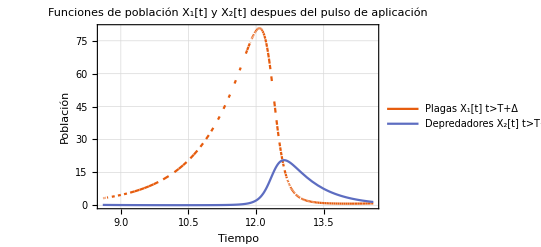

```mathematica
trueplot3=Plot[{pw1afterFromText,pw2afterFromText},{t,8.6,8.6+6},PlotTheme->"Scientific",PlotLegends->{"Plagas X_1[t] t>T+Δ","Depredadores X_2[t] t>T+Δ"},Frame->True,FrameLabel->{{"Población",None},{"Tiempo",None}},PlotLabel->"Funciones de población X_1[t] y X_2[t] despues del pulso de aplicación",GridLines->Automatic,PlotRange->All]
```

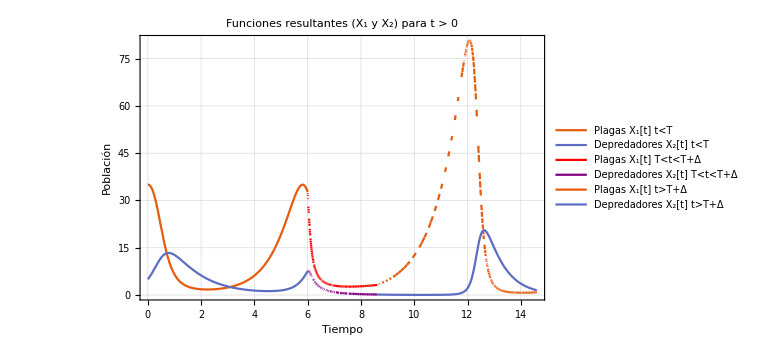

```mathematica
plotfinal=Show[trueplot1,trueplot2,trueplot3, PlotLabel->"Funciones resultantes (X_1 y X_2) para t > 0", ImageSize->Large,PlotRange->All,GridLines->Automatic]
```